### Functions

```mathematica
customActivation=ElementwiseLayer[-2.0+4/(1+Exp[-#])&];
(*customActivation1=ElementwiseLayer[0.5(#+Abs[#])+0.05&];*)
customActivation1=ElementwiseLayer[# Tanh[Log[1+Exp[#]]]&];
customActivation2=ElementwiseLayer[-2.0+4/(1+Exp[-#])&];
Plot[customActivation2[x],{x,-10,10},ImageSize->700,Axes->False,Frame->True,FrameLabel->{"x value","y value"},LabelStyle->{FontSize->19,FontFamily->"Times"}];
Plot[customActivation[x],{x,-10,10},ImageSize->700,Axes->False,Frame->True,FrameLabel->{"x value","y value"},LabelStyle->{FontSize->19,FontFamily->"Times"}];
disspnx[p_?VectorQ,t_?NumericQ,ene_?VectorQ,density_?VectorQ,number_?VectorQ,condition_?NumericQ]:=Module[{kBolt,lgp0,ep0,np0,e,np,s,es,nps,enp,e2,np2,σns,σes,σee,σnn,σen,βt,μt,avgΦ,Φ0p,iden,boper,deltaentropy},iden=Table[1,{i,Length[p]}];
boper=If[#==0,1,0]&/@p;
lgp0=-(Log[p+boper]-density);
ep0=MapThread[Times,{ene,p}];
np0=MapThread[Times,{number,p}];
e=Total[ep0];
np=Total[np0];
s=Total[MapThread[Times,{lgp0,p}]];
es=MapThread[Times,{p,lgp0}].ene;
nps=MapThread[Times,{p,lgp0}].number;
enp=MapThread[Times,{p,ene}].number;
e2=MapThread[Times,{p,ene}].ene;
np2=MapThread[Times,{p,number}].number;
σns=nps-np s;
σes=es-e s;
σee=e2-e^2;
σnn=np2-np^2;
σen=enp-e np;
(*βt=(σes)/(σee)*);
μt=(σns σee-σes σen)/(σen^2-σnn σee);
βt=(σns σen-σnn σes)/(σen^2-σnn σee);
βt=1/298;
avgΦ=βt e-s-μt np;
Φ0p=βt ene-lgp0-μt  number;
deltaentropy=Abs[(condition-s)];
Print["delta =",deltaentropy];
If[deltaentropy<=10^-30,
Table[0,{i,Length[p]}],
N[Re[(1/(τ)) MapThread[Times,{avgΦ iden-Φ0p,p}]/. values],decimals]
]
]
```

```mathematica
linf=0.05;
lsup=0.95;
monitor2[p_?VectorQ,g_?VectorQ]:=Module[{ent},
ent=-p.(Log[p]-g);
ent]
normalizeData[data_List,linf_,lsup_]:=Module[{min,max},min=Min[data];
max=Max[data];
((lsup-linf) (#-min)/(max-min)+linf)&/@data];
(*normalizeData[data_]:=With[{min=Min[data],max=Max[data]},linf+lsup*(data-min)/(max-min)];*)
generatePlot[trainedNet_,features_,classes_,index_]:=Module[{minFeature,maxFeature},minFeature=Min[features];
maxFeature=Max[features];
Show[ListPlot[Transpose[{features,classes}]],Plot[trainedNet[{index,t}],{t,minFeature,maxFeature},PlotStyle->Red]]];
processData[dataset_]:=Module[{features,classes,normalizedFeatures,normalizedClasses},
features=First@Transpose[dataset];
classes=Last@Transpose[dataset];
normalizedFeatures=normalizeData[features];
normalizedClasses=normalizeData[classes];
Transpose[{normalizedFeatures,normalizedClasses}]];
findMax[list_]:=Module[{maxval,position,point},
maxval=Max[Last[list]];
position=First[Position[Last[list],maxval]][[1]];
point=Transpose[list]⟦position⟧;
Return[point]
];
importAndProcessData[size_Integer]:=Module[{filePath,data},
filePath=baseDirectory<>fileBase<>ToString[size]<>".txt";
data=Transpose@Import[filePath,"Table"];
{First[data],Last[data]-Min[Last[data]]}];
energyRange[list_]:=Module[{},
min=Min[First[list]];
max=Max[First[list]];
Return[{min,max}];
]
rangeEnergy[t_]:={Min[First[dataenergy]]+pmin[t](Max[First[dataenergy]]-Min[First[dataenergy]]),Min[Last[dataenergy]]+pmin[t](Max[Last[dataenergy]]-Min[Last[dataenergy]])}
deDoS[latindex_,energy_]:=Module[{dedatay,dedatax},
dedatay=(trainedNet[{normalizedlattice[[latindex]],energy}]-linf)/lsup(maxDoS[normalizedlattice[[latindex]]]-0)+0;
dedatax=(energy-linf)/lsup(pmax[normalizedlattice[[latindex]]]-pmin[normalizedlattice[[latindex]]])+pmin[normalizedlattice[[latindex]]];
Return[{dedatax,dedatay}];
]
deDoS1[latindex_,energy_]:=Module[{dedatay,dedatax},
dedatay=(trainedNet[{normalizedlattice[[latindex]],energy}]-linf)/lsup(Last[maxpoints][[latindex]]-0)+0;
dedatax=(energy-linf)/lsup(Last[dataenergy][[latindex]]-First[dataenergy][[latindex]])+First[dataenergy][[latindex]];
Return[{dedatax,dedatay}];
]
dissp[p_?VectorQ,t_?NumericQ,ene_?VectorQ,density_?VectorQ,number_?VectorQ]:=Module[{kBolt,lgp0,ep0,e,s,es,e2,βt,fen,iden,floc},
iden=Table[1,{i,Length[p]}];
kBolt=1.380649 10^-23/1000; (*J/K*);
kBolt=1;
lgp0=-(Log[p]-density);
ep0=MapThread[Times,{ene,p}];
e=Total[ep0];
s=p.lgp0;
es=MapThread[Times,{p,lgp0}].ene;
e2=MapThread[Times,{ene,ene}].p;
βt=(es-e s)/(e2-e^2);
βt=1/200;
fen=βt e-s;
floc=βt ene -lgp0;
(1/(τ )) (MapThread[Times,{fen iden-floc,p}])/. values];
disspn[p_?VectorQ,t_?NumericQ,ene_?VectorQ,density_?VectorQ,number_?VectorQ]:=Module[{kBolt,lgp0,ep0,np0,e,np,s,es,nps,enp,e2,np2,σns,σes,σee,σnn,σen,βt,μt,avgΦ,Φ0p,iden,boper,deltaentropy},
iden=Table[1,{i,Length[p]}];
boper=If[#==0,1,0]&/@p;
lgp0=-(Log[p+boper]-density);
ep0=MapThread[Times,{ene,p}];
np0=MapThread[Times,{number,p}];
e=Total[ep0];
np=Total[np0];
s=Total[MapThread[Times,{lgp0,p}]];
es=MapThread[Times,{p,lgp0}].ene;
nps=MapThread[Times,{p,lgp0}].number;
enp=MapThread[Times,{p,ene}].number;
e2=MapThread[Times,{p,ene}].ene;
np2=MapThread[Times,{p,number}].number;
σns= nps- np s;
σes=es-e s;
σee=e2-e^2;
σnn=np2-np^2;
σen=enp- e np;
(*βt=(σes)/(σee)*);
μt=(σns σee-σes σen)/(σen^2-σnn σee);
(*βt=(σns σen- σnn σes)/(σen^2- σnn σee)*);
βt=βchoice;
avgΦ= βt e -s-μt np;
Φ0p=βt ene-lgp0-μt number;
N[Re[(1/(τ)) MapThread[Times,{avgΦ iden-Φ0p,p}]/.values],decimals]]
adsortion[ρt1_?VectorQ,ene_?VectorQ,density_?VectorQ,pdOS_?MatrixQ]:=Module[{ρt,lnρ,entropy,avgenergy,adsparticles,nadsparticles,,boper,avgN},
ρt=ρt1;
boper=If[#==0,1,0]&/@ρt;
lnρ=Log[ρt+boper];
entropy=-ρt.(lnρ-density);
avgenergy=ρt.ene;
adsparticles=Last[Transpose[pdOS]];
nadsparticles=Min[Length[density],Length[pdOS]];
avgN=ρt[[1;;nadsparticles]].adsparticles[[1;;nadsparticles]];
Return[{Re[entropy],Re[avgenergy],Re[avgN],Re[entropy-βchoice avgenergy ]}];
]
qcEAs[list_,Asnum0_,Asnum_]:=Module[{nAvogadro,nAs,nad,nHp,nOH,nCOO,nH2O,pMH2O,pMAs,pMGO,ρH2O,mGO,mH2O,VH2O,mAs,cAs,cGO,mHp,Cad, mads,cequil},
nAvogadro=6.02214199 10^23;
nAs=Count[Flatten@list[[1]],0];
nad=Asnum;
nHp=Count[Flatten@list[[1]],3];
nOH=Count[Flatten@list[[1]],1];
nCOO=Count[Flatten@list[[1]],2];
nH2O=Count[Flatten@list[[1]],4];
pMH2O=18; (*g/mol*)
pMAs=140.94; (*g/mol*)
pMGO= 2043;(*g/mol*)
ρH2O=1000 ;(*g/L*)
mGO=(nOH+nCOO)pMGO/nAvogadro;
mH2O=nH2O pMH2O/nAvogadro;
VH2O=mH2O/ρH2O ;(*mL*)
mAs=nAs pMAs/nAvogadro;
cAs=mAs/VH2O;
cGO=mGO/VH2O;
mHp=nHp(1/nAvogadro);
Cad=(nad pMAs/nAvogadro)/mGO;

{1000(Asnum0 -nad)pMAs/(nAvogadro VH2O),Cad 1000} ]
qcEAseval[list_,Asnum0_,Asnum_]:=Module[{nAvogadro,nAs,nad,nHp,nOH,nCOO,nH2O,pMH2O,pMAs,pMGO,ρH2O,mGO,mH2O,VH2O,mAs,cAs,cGO,mHp,Cad, mads,cequil},
nAvogadro=6.02214199 10^23;
nAs=Asnum0;
nad=Asnum;
nHp=list[[4]];
nOH=list[[2]];
nCOO=list[[3]];
nH2O=list[[5]];
pMH2O=18; (*g/mol*)
pMAs=140.94; (*g/mol*)
pMGO= 2043;(*g/mol*)
ρH2O=1000 ;(*g/L*)
mGO=(nOH+nCOO)pMGO/nAvogadro;
mH2O=nH2O pMH2O/nAvogadro;
VH2O=mH2O/ρH2O ;(*mL*)
mAs=nAs pMAs/nAvogadro;
cAs=mAs/VH2O;
cGO=mGO/VH2O;
mHp=nHp(1/nAvogadro);
Cad=(nad pMAs/nAvogadro)/mGO;

{1000(Asnum0 -nad)pMAs/(nAvogadro VH2O),Cad 1000} ]
```

### Concentrations

```mathematica
Do[
sizeLatice=i;
nAvogadro=6.023 10^23;
nAs=0.22;
nad=1.078;
nHp=1;
nOH=1;
nCOO=nOH;
nH2O=sizeLatice^2-nAs-2nOH-nHp;
pMH2O=18; (*g/mol*)
pMAs=140.94; (*g/mol*)
pMGO= 2043;(*g/mol*)
ρH2O=1000 ;(*g/L*)
mGO=(nOH+nCOO)pMGO/nAvogadro (*g*);
mH2O=nH2O pMH2O/nAvogadro (*g*);
VH2O=mH2O/ρH2O ;(*L*)
mAs=nAs pMAs/nAvogadro (*g*);
cAs=mAs/VH2O (*g/L*);
cGO=mGO/VH2O  (*g/L*);
mHp=nHp(1/nAvogadro) (*g*);
pHnum=-Log10[(nHp/nAvogadro)/VH2O];
mads=nad pMAs/nAvogadro;
Cad=(nad pMAs/nAvogadro)/mGO (*g As/ g Adsorbente*) ;
cequil=((nAs-nad )pMAs)/(nAvogadro VH2O);
Print["Lattice = ",i,", cAs = ",1000cAs," mg/L"," pH = ",pHnum," cGO = ",cGO, " g/L" ," Cad=",Cad,"g/g", " mGO=",mGO,"g", " VH2O=",VH2O ,"L"," mads=",mads ,"g"," cequil=",cequil*1000 ,"mg/L"];
,{i,80,80,10}]

datavalidation1={{27.81456954,0.0},{63.57615894,1.066666667},{119.205298,2.4},{248.3443709,4.8},{357.615894,6.666666667},{530.4635762,8},{709.2715232,9.6},{1211.92053,12.26666667}};
datavalidation={{0,0},{23.82978723 ,3.642857143},{51.63120567 ,5.357142857},{104.2553191 ,7.5},{161.3475177 ,10.07142857},{211.9858156 ,12.21428571},{271.0638298 ,13.5},{324.6808511 ,15.42857143}};
```

Lattice = 80, cAs = 269.292 mg/L pH = 2.06123 cGO = 35.4866 g/L Cad=0.0371839g/g mGO=6.78399×10^-21g VH2O=1.91171×10^-22L mads=2.52255×10^-22g cequil=-1050.24mg/L

## Potential (Fig 2)

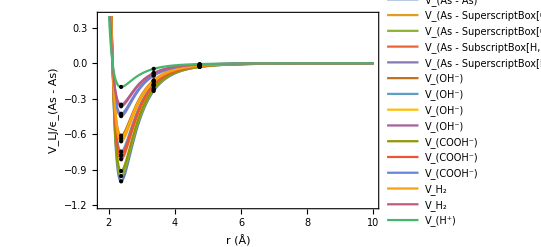

```mathematica
VLJ[ϵ12_,σ12_]:=4GeometricMean[ϵ12] ((Mean[σ12]/r)^12-(Mean[σ12]/r)^6);
convert=4184;
units=1;
ϵAs=0.23 convert;
ϵOhyd=0.141 convert;
ϵOcar=0.21 convert;
ϵH2O= 0.152 convert ;
ϵHp=0.046 convert;

σAs=4.0 units;
σOhyd=1.627 units;
σOcar=2.96 units; 
σH2O=1.768 units;
σHp=0.224 units;

normal=ϵAs;
media={σAs,σOhyd,σOcar,σH2O,σHp};
lattice=2^(1/6)Mean[media];


VAsAs=VLJ[{ϵAs,ϵAs},media];
VAsOhyd=VLJ[{ϵAs,ϵOhyd},media];
VAsOcar=VLJ[{ϵAs,ϵOcar},media];
VAsH2O=VLJ[{ϵAs,ϵH2O},media];
VAsHp=VLJ[{ϵAs,ϵHp},media];

VOhydOhyd=VLJ[{ϵOhyd,ϵOhyd},media];
VOhydOcar=VLJ[{ϵOhyd,ϵOcar},media];
VOhydH2O=VLJ[{ϵOhyd,ϵH2O},media];
VOhydHp=VLJ[{ϵOhyd,ϵHp},media];

VOcarOcar=VLJ[{ϵOcar,ϵOcar},media];
VOcarH2O=VLJ[{ϵOcar,ϵH2O},media];
VOcarHp=VLJ[{ϵOcar,ϵHp},media];

VH2OH2O=VLJ[{ϵH2O,ϵH2O},media];
VH2OHp=VLJ[{ϵH2O,ϵHp},media];

VHpHp=VLJ[{ϵHp,ϵHp},media];

assignments=Thread[r->{lattice units,lattice √2 units,2 lattice units}];
pointsVAsAs=({r,VAsAs/normal}/. #)&/@assignments;
pointsVAsOhyd=({r,VAsOhyd/normal}/. #)&/@assignments;
pointsVAsOcar=({r,VAsOcar/normal}/. #)&/@assignments;
pointsVAsH2O=({r,VAsH2O/normal}/. #)&/@assignments;
pointsVAsHp=({r,VAsHp/normal}/. #)&/@assignments;

pointsVOhydOhyd=({r,VOhydOhyd/normal}/. #)&/@assignments;
pointsVOhydOcar=({r,VOhydOcar/normal}/. #)&/@assignments;
pointsVOhydH2O=({r,VOhydH2O/normal}/. #)&/@assignments;
pointsVOhydHp=({r,VOhydHp/normal}/. #)&/@assignments;

pointsVOcarOcar=({r,VOcarOcar/normal}/. #)&/@assignments;
pointsVOcarH2O=({r,VOcarH2O/normal}/. #)&/@assignments;
pointsVOcarHp=({r,VOcarHp/normal}/. #)&/@assignments;

pointsVH2OH2O=({r,VH2OH2O/normal}/. #)&/@assignments;
pointsVH2OHp=({r,VH2OHp/normal}/. #)&/@assignments;

pointsVHpHp=({r,VHpHp/normal}/. #)&/@assignments;

Plot[{VAsAs/normal,VAsOhyd/normal,VAsOcar/normal,VAsH2O/normal,VAsHp/normal,VOhydOhyd/normal,VOhydOcar/normal,VOhydH2O/normal,VOhydHp/normal,VOcarOcar/normal,VOcarH2O/normal,VOcarHp/normal,VH2OH2O/normal,VH2OHp/normal,VHpHp/normal},{r,1.82 units,10 units},FrameLabel->{"r (Å)","V_LJ/ϵ_(As - As)"},PlotStyle->Automatic,LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},PlotRange->{-1.2,0.4},Axes->False,Frame->True,Epilog->{PointSize[Large],
Point[pointsVAsAs],Point[pointsVAsOhyd],Point[pointsVAsOcar],Point[pointsVAsH2O],Point[pointsVAsHp],
Point[pointsVOhydOhyd],Point[pointsVOhydOcar],Point[pointsVOhydH2O],Point[pointsVOhydHp],
Point[pointsVOcarOcar],Point[pointsVOcarH2O],Point[pointsVOcarHp],
Point[pointsVH2OH2O],Point[pointsVH2OHp],
Point[pointsVHpHp]},
PlotLegends->
Placed[{
"V_(As - As)","V_(As - SuperscriptBox[OH, -])","V_(As - SuperscriptBox[COOH, -])","V_(As - SubscriptBox[H, 2] O)","V_(As - SuperscriptBox[H, +])",
"V_(OH^-)","V_(OH^-)","V_(OH^-)","V_(OH^-)",
"V_(COOH^-)","V_(COOH^-)","V_(COOH^-)",
"V_H_2","V_H_2",
"V_(H^+)"},{0.75,0.35}]]
```

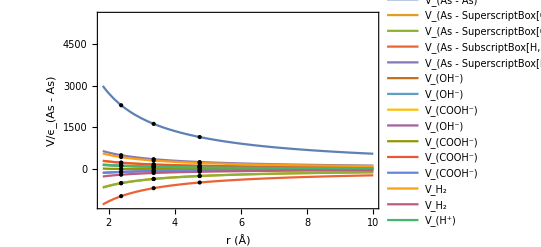

```mathematica
VCo[q1_,q2_]:=ke(q1 q2)/r;
ke=10^10/(4 π 8.854 10^-12) (6.02214076 10^23 )(1.60217662 10^-19)^2 ;
qAs=1.941;
qOhyd=-0.433;
qOcar=-0.440;
qHp=0.417;
qH2O=-0.834;

VAsAs=VCo[qAs,qAs];
VAsOcar=VCo[qAs,qOcar];
VAsOhyd=VCo[qAs,qOhyd];
VAsH2O=VCo[qAs,qH2O];
VAsHp=VCo[qAs,qHp];

VOhydOhyd=VCo[qOhyd,qOhyd];
VOhydOcar=VCo[qOhyd,qOcar];
VOhydH2O=VCo[qOhyd,qH2O];
VOhydHp=VCo[qOhyd,qHp];

VOcarOocar=VCo[qOcar,qOcar];
VOcarH2O=VCo[qOcar,qH2O];
VOcarHp=VCo[qOcar,qHp];

VH2OH2O=VCo[qH2O,qH2O];
VH2OHp=VCo[qH2O,qHp];

VHpHp=VCo[qHp,qHp];

assignments=Thread[r->{lattice units,lattice √2 units,2 lattice units}];

cpointsVAsAs=({r,VAsAs/normal}/. #)&/@assignments;
cpointsVAsOhyd=({r,VAsOhyd/normal}/. #)&/@assignments;
cpointsVAsOcar=({r,VAsOcar/normal}/. #)&/@assignments;
cpointsVAsH2O=({r,VAsH2O/normal}/. #)&/@assignments;
cpointsVAsHp=({r,VAsHp/normal}/. #)&/@assignments;

cpointsVOhydOhyd=({r,VOhydOhyd/normal}/. #)&/@assignments;
cpointsVOhydOcar=({r,VOhydOcar/normal}/. #)&/@assignments;
cpointsVOhydH2O=({r,VOhydH2O/normal}/. #)&/@assignments;
cpointsVOhydHp=({r,VOhydHp/normal}/. #)&/@assignments;

cpointsVOcarOcar=({r,VOcarOcar/normal}/. #)&/@assignments;
cpointsVOcarH2O=({r,VOcarH2O/normal}/. #)&/@assignments;
cpointsVOcarHp=({r,VOcarHp/normal}/. #)&/@assignments;

cpointsVH2OH2O=({r,VH2OH2O/normal}/. #)&/@assignments;
cpointsVH2OHp=({r,VH2OHp/normal}/. #)&/@assignments;

cpointsVHpHp=({r,VHpHp/normal}/. #)&/@assignments;

Plot[{VAsAs/normal,VAsOhyd/normal,VAsOcar/normal,VAsH2O/normal,VAsHp/normal,VOhydOhyd/normal,VOhydOcar/normal,VOhydH2O/normal,VOhydHp/normal,VOcarOcar/normal,VOcarH2O/normal,VOcarHp/normal,VH2OH2O/normal,VH2OHp/normal,VHpHp/normal},{r,1.82 units,10 units},FrameLabel->{"r (Å)","V/ϵ_(As - As)"},PlotStyle->Automatic,LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},PlotRange->{-1300,5500},Axes->False,Frame->True,Epilog->{PointSize[Large],
Point[cpointsVAsAs],Point[cpointsVAsOhyd],Point[cpointsVAsOcar],Point[cpointsVAsH2O],Point[cpointsVAsHp],
Point[cpointsVOhydOhyd],Point[cpointsVOhydOcar],Point[cpointsVOhydH2O],Point[cpointsVOhydHp],
Point[cpointsVOcarOcar],Point[cpointsVOcarH2O],Point[cpointsVOcarHp],
Point[cpointsVH2OH2O],Point[cpointsVH2OHp],
Point[cpointsVHpHp]},
PlotLegends->
Placed[{
"V_(As - As)","V_(As - SuperscriptBox[OH, -])","V_(As - SuperscriptBox[COOH, -])","V_(As - SubscriptBox[H, 2] O)","V_(As - SuperscriptBox[H, +])",
"V_(OH^-)","V_(OH^-)","V_(COOH^-)","V_(OH^-)",
"V_(COOH^-)","V_(COOH^-)","V_(COOH^-)",
"V_H_2","V_H_2",
"V_(H^+)"},{0.75,0.65}]]
```

```mathematica
scalingFactor=100;
ii=1;
lAs={Last[cpointsVAsAs⟦ii⟧+pointsVAsAs⟦ii⟧],Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧]};
lHyd={Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVOhydOhyd⟦ii⟧+pointsVOhydOhyd⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧]};
lCar={Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOcarOcar⟦ii⟧+pointsVOcarOcar⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧]};
lH2O={Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVH2OH2O⟦ii⟧+pointsVH2OH2O⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧]};
lHp={Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧],Last[cpointsVHpHp⟦ii⟧+pointsVHpHp⟦ii⟧]};
table1=Prepend[Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor],{"As","OH","Car","H_2O","H^+"}];
Print["Distance ",ii]
Print[TableForm[MapThread[Prepend,{table1,{"","As","OH","Car","H_2O","H^+"}}]]]
Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor]
```

Distance 1

| As | OH | Car | H_2O | H^+
As | 23 | -5 | -5 | -10 | 5
OH | -5 | 1 | 1 | 2 | -1
Car | -5 | 1 | 0 | 2 | -1
H_2O | -10 | 2 | 2 | 4 | -2
H^+ | 5 | -1 | -1 | -2 | 1

{{23,-5,-5,-10,5},{-5,1,1,2,-1},{-5,1,0,2,-1},{-10,2,2,4,-2},{5,-1,-1,-2,1}}

```mathematica
ii=2;
lAs={Last[cpointsVAsAs⟦ii⟧+pointsVAsAs⟦ii⟧],Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧]};
lHyd={Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVOhydOhyd⟦ii⟧+pointsVOhydOhyd⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧]};
lCar={Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOcarOcar⟦ii⟧+pointsVOcarOcar⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧]};
lH2O={Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVH2OH2O⟦ii⟧+pointsVH2OH2O⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧]};
lHp={Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧],Last[cpointsVHpHp⟦ii⟧+pointsVHpHp⟦ii⟧]};
table1=Prepend[Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor],{"As","OH","Car","H_2O","H^+"}];
Print["Distance ",ii]
Print[TableForm[MapThread[Prepend,{table1,{"","As","OH","Car","H_2O","H^+"}}]]]
Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor]
```

Distance 2

| As | OH | Car | H_2O | H^+
As | 16 | -4 | -4 | -7 | 3
OH | -4 | 1 | 1 | 2 | -1
Car | -4 | 1 | 0 | 2 | -1
H_2O | -7 | 2 | 2 | 3 | -1
H^+ | 3 | -1 | -1 | -1 | 1

{{16,-4,-4,-7,3},{-4,1,1,2,-1},{-4,1,0,2,-1},{-7,2,2,3,-1},{3,-1,-1,-1,1}}

```mathematica
ii=3;
lAs={Last[cpointsVAsAs⟦ii⟧+pointsVAsAs⟦ii⟧],Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧]};
lHyd={Last[cpointsVAsOhyd⟦ii⟧+pointsVAsOhyd⟦ii⟧],Last[cpointsVOhydOhyd⟦ii⟧+pointsVOhydOhyd⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧]};
lCar={Last[cpointsVAsOcar⟦ii⟧+pointsVAsOcar⟦ii⟧],Last[cpointsVOhydOcar⟦ii⟧+pointsVOhydOcar⟦ii⟧],Last[cpointsVOcarOcar⟦ii⟧+pointsVOcarOcar⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧]};
lH2O={Last[cpointsVAsH2O⟦ii⟧+pointsVAsH2O⟦ii⟧],Last[cpointsVOhydH2O⟦ii⟧+pointsVOhydH2O⟦ii⟧],Last[cpointsVOcarH2O⟦ii⟧+pointsVOcarH2O⟦ii⟧],Last[cpointsVH2OH2O⟦ii⟧+pointsVH2OH2O⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧]};
lHp={Last[cpointsVAsHp⟦ii⟧+pointsVAsHp⟦ii⟧],Last[cpointsVOhydHp⟦ii⟧+pointsVOhydHp⟦ii⟧],Last[cpointsVOcarHp⟦ii⟧+pointsVOcarHp⟦ii⟧],Last[cpointsVH2OHp⟦ii⟧+pointsVH2OHp⟦ii⟧],Last[cpointsVHpHp⟦ii⟧+pointsVHpHp⟦ii⟧]};
table1=Prepend[Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor],{"As","OH","Car","H_2O","H^+"}];
Print["Distance ",ii]
Print[TableForm[MapThread[Prepend,{table1,{"","As","OH","Car","H_2O","H^+"}}]]]
Round[{lAs,lHyd,lCar,lH2O,lHp}/scalingFactor]
```

Distance 3

| As | OH | Car | H_2O | H^+
As | 11 | -3 | -3 | -5 | 2
OH | -3 | 1 | 1 | 1 | -1
Car | -3 | 1 | 0 | 1 | -1
H_2O | -5 | 1 | 1 | 2 | -1
H^+ | 2 | -1 | -1 | -1 | 1

{{11,-3,-3,-5,2},{-3,1,1,1,-1},{-3,1,0,1,-1},{-5,1,1,2,-1},{2,-1,-1,-1,1}}

## Fig 5. Machine Learning

### From RWL

/Users/cesardamian/Desktop/Data/ML/

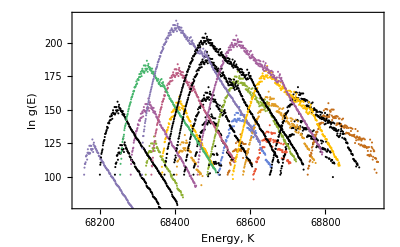

```mathematica
inDirectory=SetDirectory[NotebookDirectory[]];
baseDir=StringJoin[inDirectory,"/ML/"]
fileName[as_,go_]:=StringJoin[baseDir,"L70_As",IntegerString[as],"_GO",IntegerString[go],"_H1_DOS.txt"];
dosFiles=DeleteCases[Table[If[as==6&&go==6,Null,Import[fileName[as,go],"Table"]],{as,1,5},{go,1,5}],Null,{2}];
dataPlots=Flatten[dosFiles,1];
gl=ListPlot[dataPlots,Joined->False,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black,Thickness[.004],Dashed},LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->{Automatic,Automatic},ImageSize->{700},PlotRange->{79,220},Axes->False,Frame->True]
```

Tags for the particle number: {-0.5,0.1,0.7,1.3,1.9}

Range of variables = {-0.5,1.9}

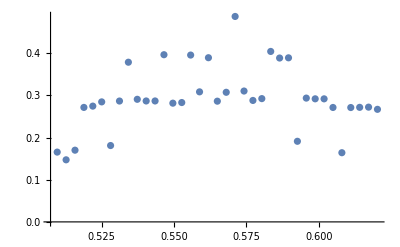

```mathematica
linf=-.5;
lsup=1.90;
labels=Flatten[Table[{i,j},{i,1,5},{j,1,5}],1];
taggedData=Flatten[Table[{Join[labels[[i]],#]}&/@dataPlots[[i]],{i,Length[dataPlots]}],2];
inputs=taggedData[[All,{1,2,3}]];
(*normalizedInputs=Transpose[{normalizeData[Transpose[inputs][[1]]],normalizeData[Transpose[inputs][[2]]],normalizeData[Transpose[inputs][[3]]]}];*)
normalizedInputs=Transpose[{normalizeData[Transpose[inputs][[1]],linf,lsup],normalizeData[Transpose[inputs][[2]],linf,lsup],normalizeData[Transpose[inputs][[3]],linf,lsup]}];
outputs=taggedData[[All,4]];
normalizedOutputs=normalizeData[outputs,linf,lsup];
Print["Tags for the particle number: ",DeleteDuplicates[Transpose[normalizedInputs[[All,1]]]]];
Print["Range of variables = ",{Min@normalizedOutputs,Max@normalizedOutputs}];
net1=NetChain[{100,customActivation,30,customActivation,30,customActivation,1},"Input"->3,"Output"->"Scalar"];
ann1=NetTrain[net1,Thread[normalizedInputs->normalizedOutputs],ValidationSet->Scaled[0.1],Method->{"ADAM"}];
Show[ListPlot[Transpose[{normalizedInputs[[All,3]][[1;;Length[dataPlots[[1]]]]],normalizedOutputs[[1;;Length[dataPlots[[1]]]]]}]],Plot[ann1[{-0.05,-0.05,x}],{x,-1.9,1.9}]]
```

As = 3. GO = 4.

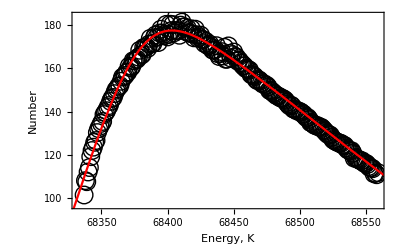

```mathematica
mins={Min@Transpose[inputs][[1]],Min@Transpose[inputs][[2]],Min@Transpose[inputs][[3]],Min@outputs};
maxs={Max@Transpose[inputs][[1]],Max@Transpose[inputs][[2]],Max@Transpose[inputs][[3]],Max@outputs};
normalizedAs=.7;
normalizedGO=1.3;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];
Print["As = ",denormalizedAs," GO = ",denormalizedGO]

Show[ListPlot[Import[StringJoin[baseDir,"L70_As3_GO4_H1_DOS.txt"],"Table"],Frame->True,PlotMarkers->{"○",18},ImageSize->{700},FrameLabel->{"Energy, K","Number"},PlotStyle->{Black,Thickness[.004],Dashed},LabelStyle->{FontSize->19,FontFamily->"Times"}],
ParametricPlot[
{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,-1.9,1.9},ImageSize->{700},AspectRatio->1/GoldenRatio,PlotStyle->Red]
]
```

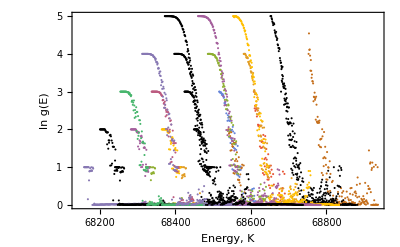

```mathematica
fileName[as_,go_]:=StringJoin[baseDir,"L70_As",IntegerString[as],"_GO",IntegerString[go],"_H1_Nt.txt"];
dosFiles=DeleteCases[Table[If[as==6&&go==6,Null,Import[fileName[as,go],"Table"]],{as,1,5},{go,1,5}],Null,{2}];
dataPlotsNt=Flatten[dosFiles,1];
gl=ListPlot[dataPlotsNt,Joined->False,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black,Thickness[.004],Dashed},LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->{Automatic,Automatic},ImageSize->{700},PlotRange->All,Axes->False,Frame->True]
```

```mathematica
linf1=-.5;
lsup1=1.9;
labels=Flatten[Table[{i,j},{i,1,5},{j,1,5}],1];
taggedDataNt=Flatten[Table[{Join[labels[[i]],#]}&/@dataPlotsNt[[i]],{i,Length[dataPlotsNt]}],2];
inputsNt=taggedDataNt[[All,{1,2,3}]];
normalizedInputsNt=Transpose[{normalizeData[Transpose[inputsNt][[1]],linf1,lsup1],normalizeData[Transpose[inputsNt][[2]],linf1,lsup1],normalizeData[Transpose[inputsNt][[3]],linf1,lsup1]}];
outputsNt=taggedDataNt[[All,4]];
normalizedOutputsNt=normalizeData[outputsNt,linf1,lsup1];
Print["Tags for the particle number: ",DeleteDuplicates[Transpose[normalizedInputsNt[[All,1]]]]];
Print["Range of variables = ",{Min@normalizedOutputsNt,Max@normalizedOutputsNt}];
netNt=NetChain[{30,customActivation1,30,customActivation2,1},"Input"->3,(*The input size*)"Output"->"Scalar"];
annNt=NetTrain[netNt,Thread[normalizedInputsNt->normalizedOutputsNt],ValidationSet->Scaled[0.1]];
(*annNt=Predict[Thread[normalizedInputsNt->normalizedOutputsNt],Method->"NearestNeighbors"];*)
```

Tags for the particle number: {-0.5,0.1,0.7,1.3,1.9}

Range of variables = {-0.5,1.9}

As = 3. GO = 4.

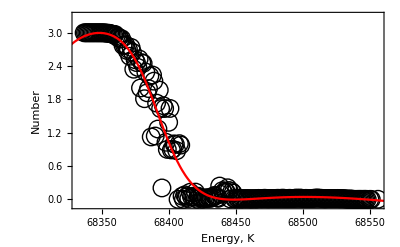

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(* Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.22 de As con un PM del GO 5 2043 *)
normalizedAs=.7;
normalizedGO=1.3;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
Print["As = ",denormalizedAs," GO = ",denormalizedGO]

Show[ListPlot[Import[StringJoin[baseDir,"L70_As3_GO4_H1_Nt.txt"],"Table"],PlotRange->{-.10,3.3},Frame->True,PlotMarkers->{"○",18},ImageSize->{700},FrameLabel->{"Energy, K","Number"},PlotStyle->{Black,Thickness[.004],Dashed},LabelStyle->{FontSize->19,FontFamily->"Times"}],
ParametricPlot[
{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]
},{x,linf1,lsup1},ImageSize->{700},AspectRatio->1/GoldenRatio,PlotStyle->Red]
]
```

### Validation points (point 1)

As = 0.22 GO = 0.0168333

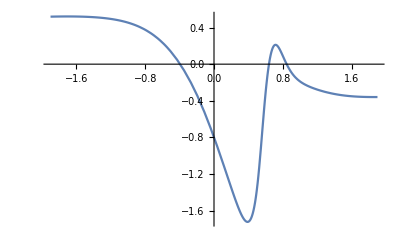

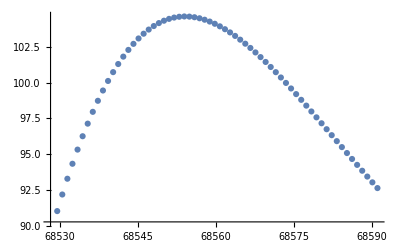

```mathematica
factor=10.0;
decimals=20;
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.16 de As*)
normalizedAs=-.968;
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];

datax=SetPrecision[Table[{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,0.64,.83,.003}],decimals];

Print["As = ",denormalizedAs," GO = ",denormalizedGO]
Plot[ann1[{normalizedAs,normalizedGO,x}]==0,{x,-1.9,1.9}]
ListPlot[datax]
```

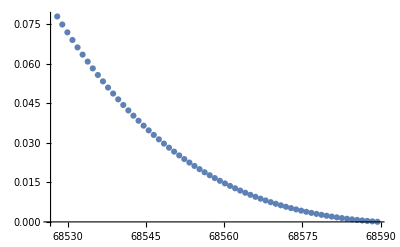

As = 0.22 GO = 0.0168333

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(* Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.22 de As con un PM del GO 5 2043 *)
normalizedAs=-.968; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
f1=((annNt[{normalizedAs,normalizedGO,0.64}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]);
f2=((annNt[{normalizedAs,normalizedGO,0.83}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]])(0.22/f1);
partialx=SetPrecision[Table[{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(((annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]))(0.22/f1)-f2
},{x,0.64,.83,.003}],decimals];

ListPlot[partialx]
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
```

```mathematica
decimals=20;
nparx=Length[partialx];
time=1.0;
values={τ->1.0};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(nparx-1),1/100,100],{i,1,nparx}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
βchoice=1/850000;
```

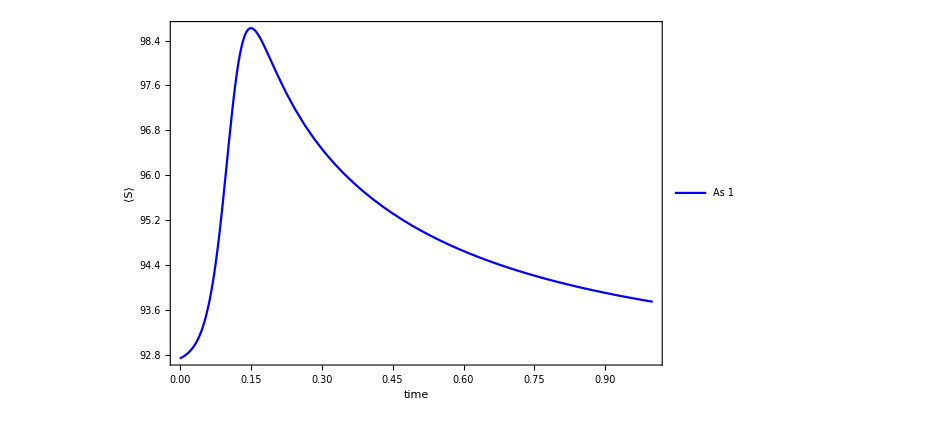

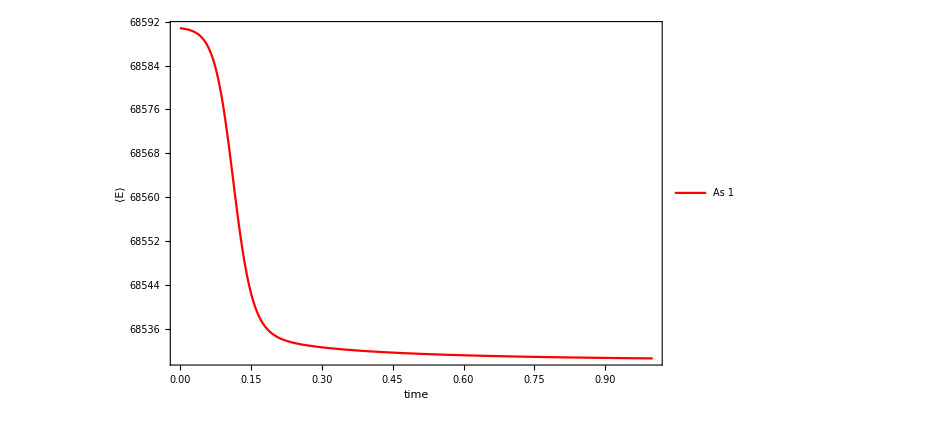

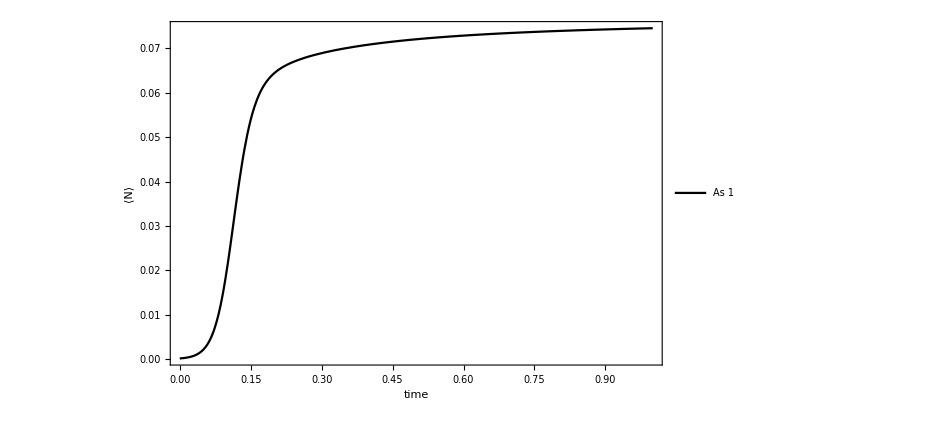

```mathematica
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[datax]][[1;;nparx]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQTx=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQTx[t1],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

```mathematica
cp1=Plot[disspn[ρttSEAQTx[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]][[2]],{t,0,time},PlotRange->All];
```

```mathematica
point1={qcEAseval[{denormalizedAs,denormalizedGO,denormalizedGO,1,70^2-denormalizedAs-1-2 denormalizedGO},
denormalizedAs,
1/factor SetPrecision[adsortion[ρttSEAQTx[time],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[3]],decimals]]}
```

{{339.729,15.2712}}

### Validation points (point 2)

As = 0.16 GO = 0.0168333

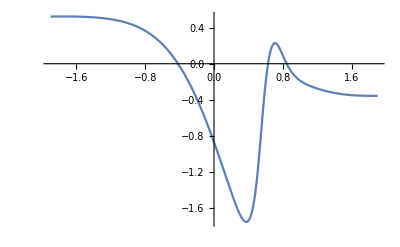

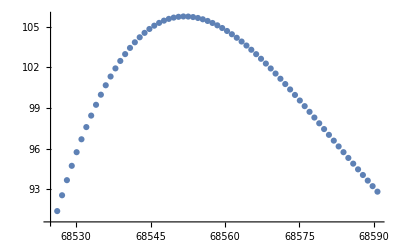

```mathematica
decimals=20;
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.16 de As*)
normalizedAs=-1.004; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];

datax=SetPrecision[Table[{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,0.63,.83,.003}],decimals];

Print["As = ",denormalizedAs," GO = ",denormalizedGO]
Plot[ann1[{normalizedAs,normalizedGO,x}]==0,{x,-1.9,1.9}]
ListPlot[datax]
```

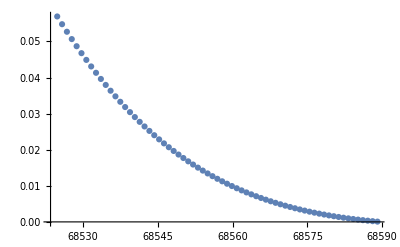

As = 0.16 GO = 0.0168333

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.16 de As*)
normalizedAs=-1.004; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
f1=((annNt[{normalizedAs,normalizedGO,0.64}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]);
f2=((annNt[{normalizedAs,normalizedGO,0.83}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]])(0.16/f1);
partialx=SetPrecision[Table[{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(((annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]))(0.16/f1)-f2
},{x,0.63,.83,.003}],decimals];
ListPlot[partialx]
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
```

```mathematica
decimals=20;
nparx=Length[partialx];
time=1.0;
values={τ->1.0};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(nparx-1),1/100,100],{i,1,nparx}]
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
βchoice=1/850000;
```

{1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100}

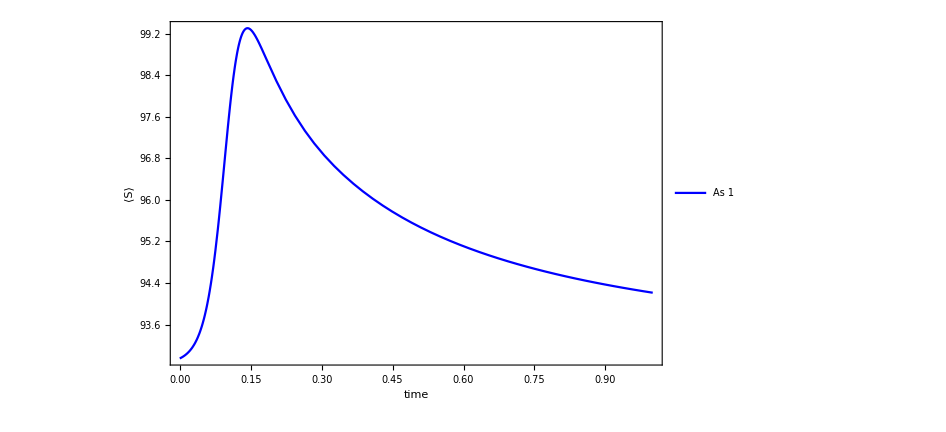

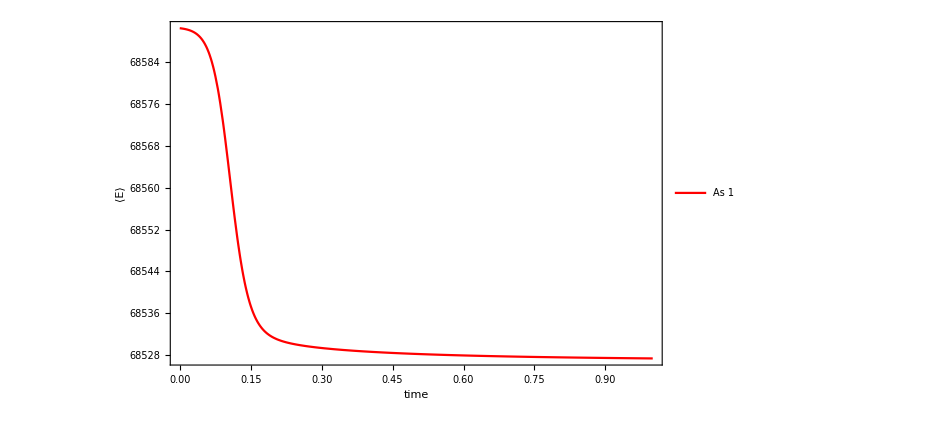

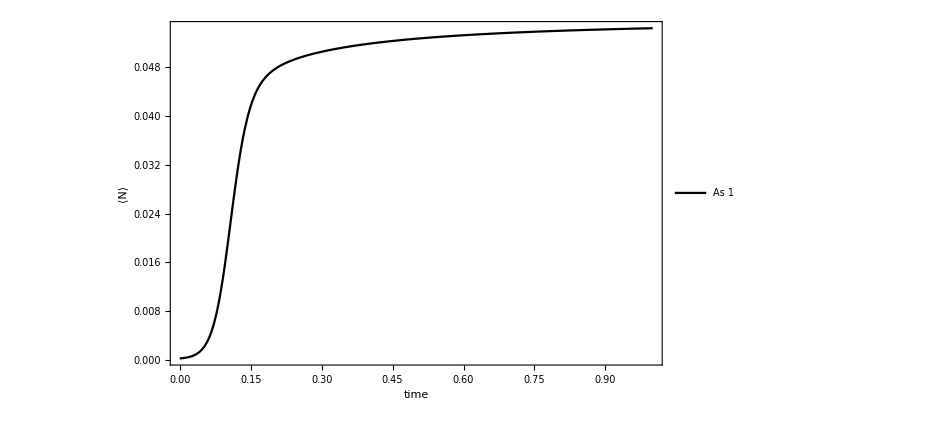

```mathematica
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[datax]][[1;;nparx]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQTx=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQTx[t1],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

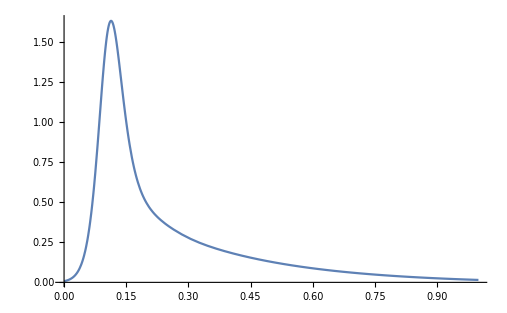

```mathematica
cp2=Plot[disspn[ρttSEAQTx[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]][[2]],{t,0,time},PlotRange->All]
```

```mathematica
point2={qcEAseval[{denormalizedAs,denormalizedGO,denormalizedGO,1,70^2-denormalizedAs-1-2 denormalizedGO},
denormalizedAs,
1/factor SetPrecision[adsortion[ρttSEAQTx[time],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[3]],decimals]]}
```

{{247.033,11.1577}}

### Validation points (point 3)

As = 0.095 GO = 0.0168333

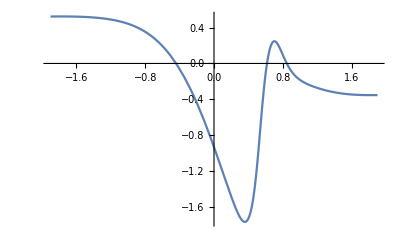

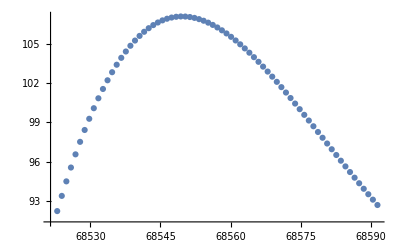

```mathematica
decimals=20;
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.094 de As*)
normalizedAs=-1.043; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];

datax=SetPrecision[Table[{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,0.62,.83,.003}],decimals];

Print["As = ",denormalizedAs," GO = ",denormalizedGO]
Plot[ann1[{normalizedAs,normalizedGO,x}]==0,{x,-1.9,1.9}]
ListPlot[datax]
```

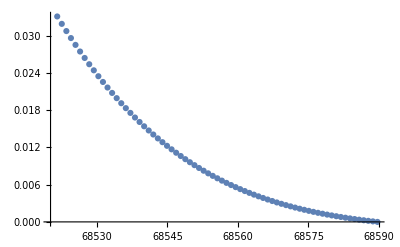

As = 0.095 GO = 0.0168333

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.094 de As*)
normalizedAs=-1.043; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
f1=((annNt[{normalizedAs,normalizedGO,0.64}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]);
f2=((annNt[{normalizedAs,normalizedGO,0.83}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]])(0.094/f1);
partialx=SetPrecision[Table[{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(((annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]))(0.094/f1)-f2
},{x,0.62,.83,.003}],decimals];
ListPlot[partialx]
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
```

```mathematica
decimals=20;
nparx=Length[partialx];
time=1.0;
values={τ->1.0};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(nparx-1),1/100,100],{i,1,nparx}]
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
βchoice=1/850000;
```

{1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100}

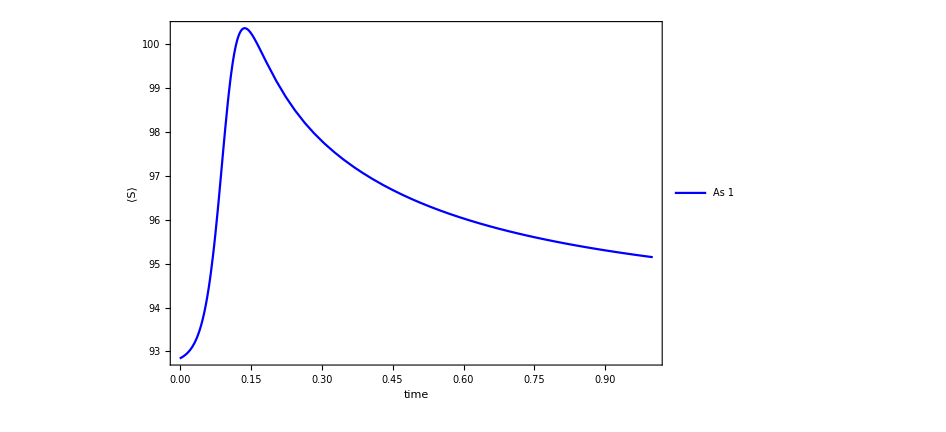

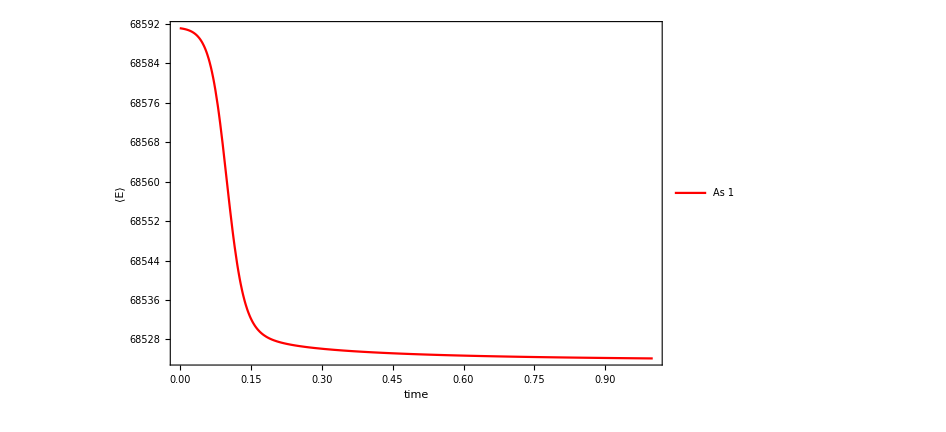

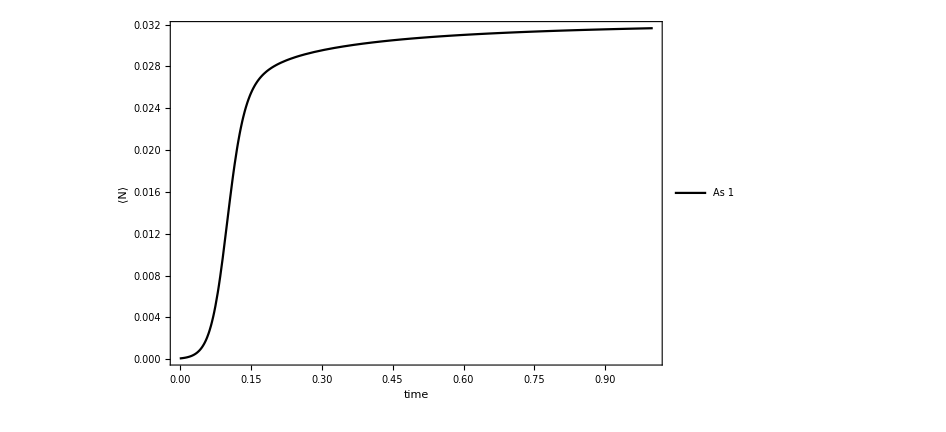

```mathematica
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[datax]][[1;;nparx]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQTx=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQTx[t1],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

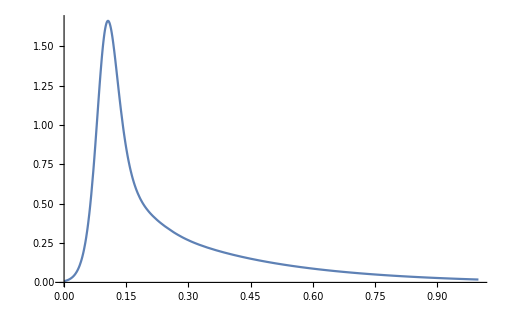

```mathematica
cp3=Plot[disspn[ρttSEAQTx[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]][[2]],{t,0,time},PlotRange->All]
```

```mathematica
point3={qcEAseval[{denormalizedAs,denormalizedGO,denormalizedGO,1,70^2-denormalizedAs-1-2 denormalizedGO},
denormalizedAs,
1/factor SetPrecision[adsortion[ρttSEAQTx[time],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[3]],decimals]]}
```

{{146.781,6.48659}}

### Validation points (point 4)

As = 0.05 GO = 0.0168333

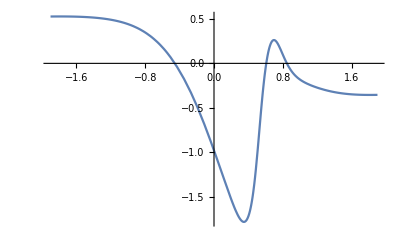

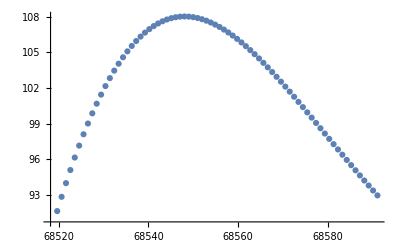

```mathematica
decimals=20;
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.05 de As*)
normalizedAs=-1.07; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];

datax=SetPrecision[Table[{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,0.61,.83,.003}],decimals];
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
Plot[ann1[{normalizedAs,normalizedGO,x}]==0,{x,-1.9,1.9}]
ListPlot[datax]
```

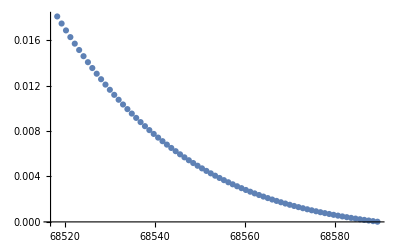

As = 0.05 GO = 0.0168333

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.05 de As*)
normalizedAs=-1.07; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
f1=((annNt[{normalizedAs,normalizedGO,0.64}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]);
f2=((annNt[{normalizedAs,normalizedGO,0.83}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]])(0.05/f1);
partialx=SetPrecision[Table[{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(((annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]))(0.05/f1)-f2
},{x,0.61,.83,.003}],decimals];
ListPlot[partialx]
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
```

```mathematica
decimals=20;
nparx=Length[partialx];
time=1.0;
values={τ->1.0};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(nparx-1),1/100,100],{i,1,nparx}]
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
βchoice=1/850000;
```

{1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100}

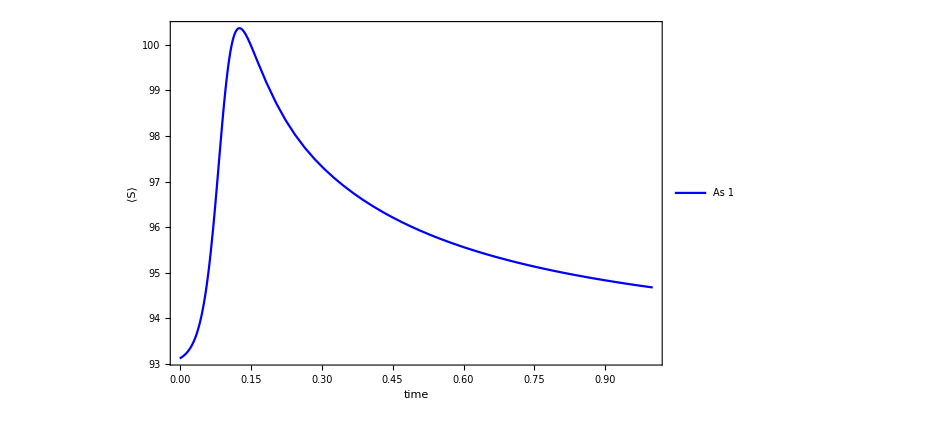

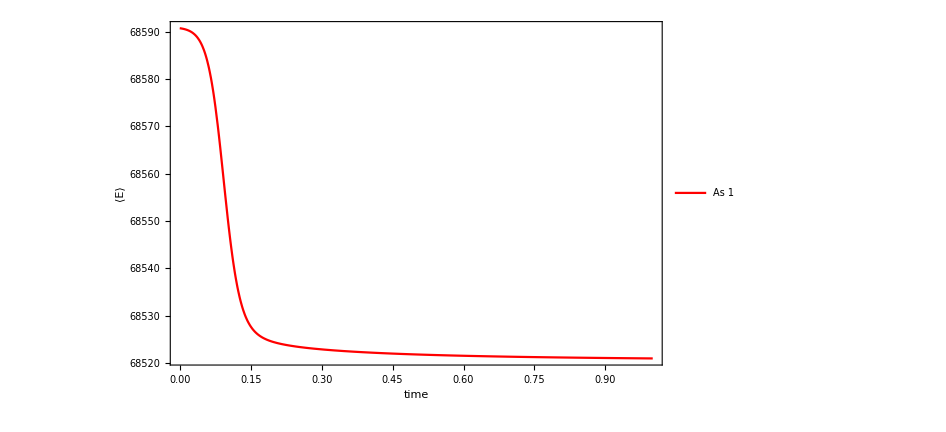

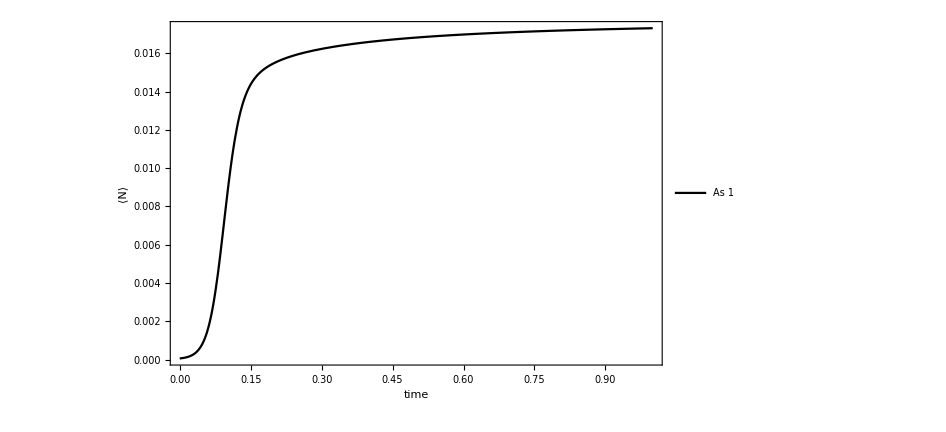

```mathematica
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[datax]][[1;;nparx]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQTx=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQTx[t1],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

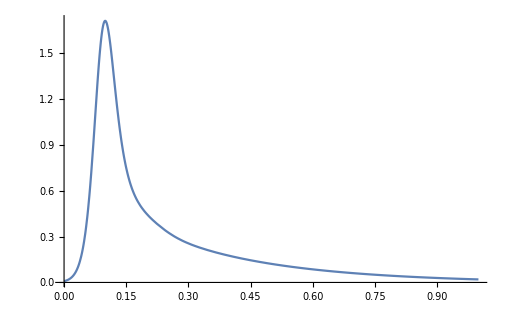

```mathematica
cp4=Plot[disspn[ρttSEAQTx[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]][[2]],{t,0,time},PlotRange->All]
```

```mathematica
point4={qcEAseval[{denormalizedAs,denormalizedGO,denormalizedGO,1,70^2-denormalizedAs-1-2 denormalizedGO},
denormalizedAs,
1/factor SetPrecision[adsortion[ρttSEAQTx[time],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[3]],decimals]]}
```

{{77.1493,3.54658}}

### Validation points (point 5)

As = 0.0183333 GO = 0.0168333

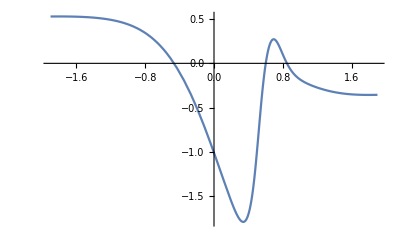

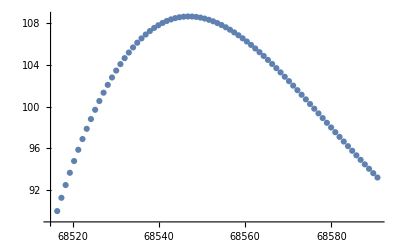

```mathematica
decimals=20;
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.0188 de As*)
normalizedAs=-1.089; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf)/(lsup-linf)(maxs[[1]]-mins[[1]])+mins[[1]];
denormalizedGO=(normalizedGO-linf)/(lsup-linf)(maxs[[2]]-mins[[2]])+mins[[2]];

datax=SetPrecision[Table[{
(x-linf)/(lsup-linf) (maxs[[3]]-mins[[3]])+mins[[3]],
(ann1[{normalizedAs,normalizedGO,x}]-linf)/(lsup-linf)(maxs[[4]]-mins[[4]])+mins[[4]]
},{x,0.60,.83,.003}],decimals];
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
Plot[ann1[{normalizedAs,normalizedGO,x}]==0,{x,-1.9,1.9}]
ListPlot[datax]
```

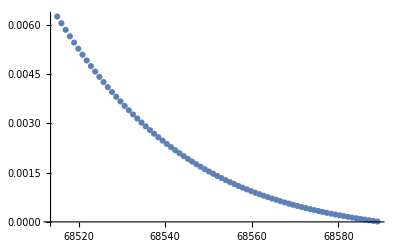

As = 0.0183333 GO = 0.0168333

```mathematica
minsN={Min@Transpose[inputsNt][[1]],Min@Transpose[inputsNt][[2]],Min@Transpose[inputsNt][[3]],Min@outputsNt};
maxsN={Max@Transpose[inputsNt][[1]],Max@Transpose[inputsNt][[2]],Max@Transpose[inputsNt][[3]],Max@outputsNt};
(*Este valor sirve para reproducir el punto final de la isoterma con 0.0168 particulas de cada GO y 0.0188 de As*)
normalizedAs=-1.089; 
normalizedGO=-1.0899;
denormalizedAs=(normalizedAs-linf1)/(lsup1-linf1)(maxsN[[1]]-minsN[[1]])+minsN[[1]];
denormalizedGO=(normalizedGO-linf1)/(lsup1-linf1)(maxsN[[2]]-minsN[[2]])+minsN[[2]];
f1=((annNt[{normalizedAs,normalizedGO,0.60}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]);
f2=((annNt[{normalizedAs,normalizedGO,0.83}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]])(0.0188/f1);
partialx=SetPrecision[Table[{
(x-linf1)/(lsup1-linf1) (maxsN[[3]]-minsN[[3]])+minsN[[3]],
(((annNt[{normalizedAs,normalizedGO,x}]-linf1)/(lsup1-linf1)(maxsN[[4]]-minsN[[4]])+minsN[[4]]))(0.0188/f1)-f2
},{x,0.60,.83,.003}],decimals];

ListPlot[partialx]
Print["As = ",denormalizedAs," GO = ",denormalizedGO]
```

```mathematica
decimals=20;
nparx=Length[partialx];
time=1.0;
values={τ->1.0};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(nparx-1),1/100,100],{i,1,nparx}]
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
βchoice=1/850000;
```

{1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100}

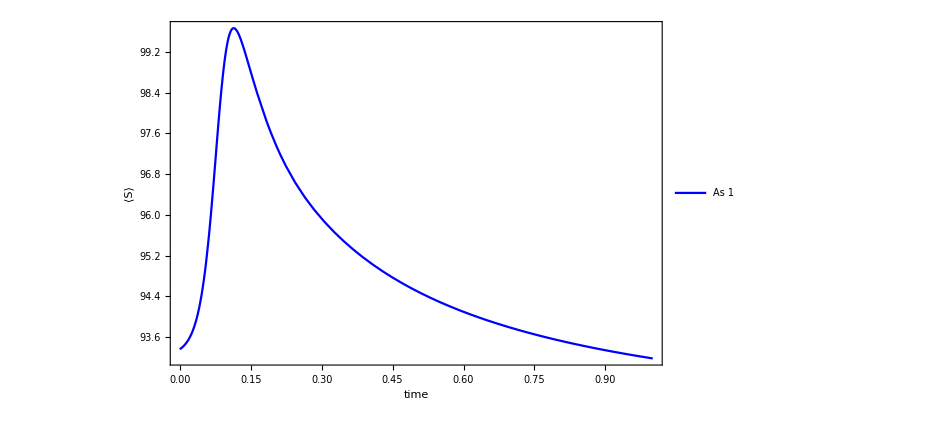

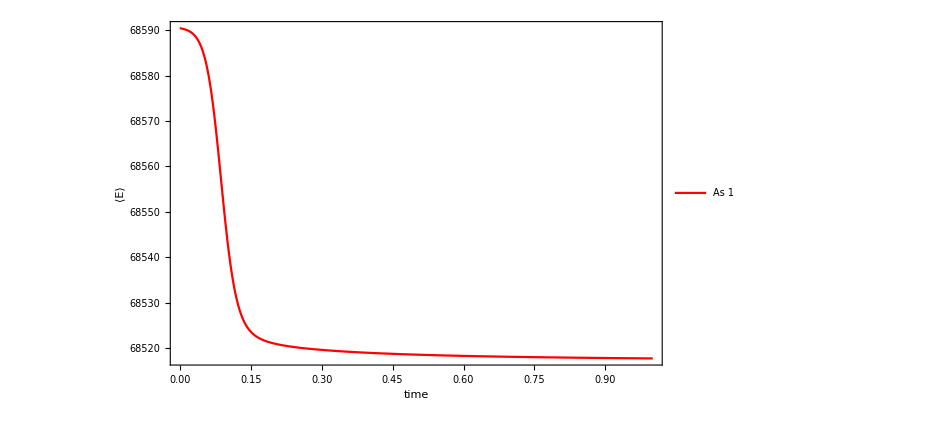

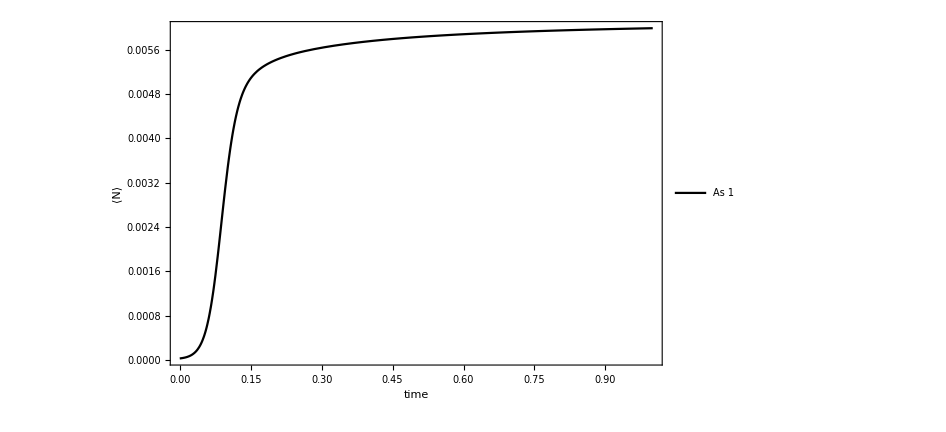

```mathematica
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[datax]][[1;;nparx]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQTx=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQTx[t1],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

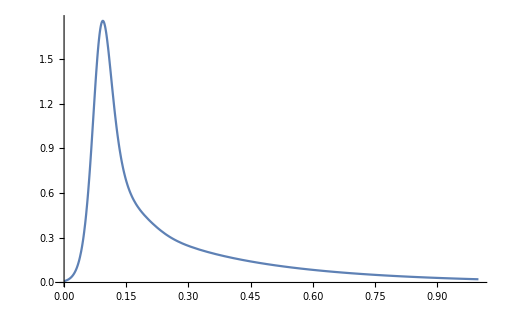

```mathematica
cp5=Plot[disspn[ρttSEAQTx[t],t,First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],Last[Transpose[partialx]]][[2]],{t,0,time},PlotRange->All]
```

```mathematica
point5={qcEAseval[{denormalizedAs,denormalizedGO,denormalizedGO,1,70^2-denormalizedAs-1-2 denormalizedGO},
denormalizedAs,
1/factor SetPrecision[adsortion[ρttSEAQTx[time],First[Transpose[datax]][[1;;nparx]],Last[Transpose[datax]][[1;;nparx]],partialx][[3]],decimals]]}
```

{{28.3452,1.22689}}

### Validation plot

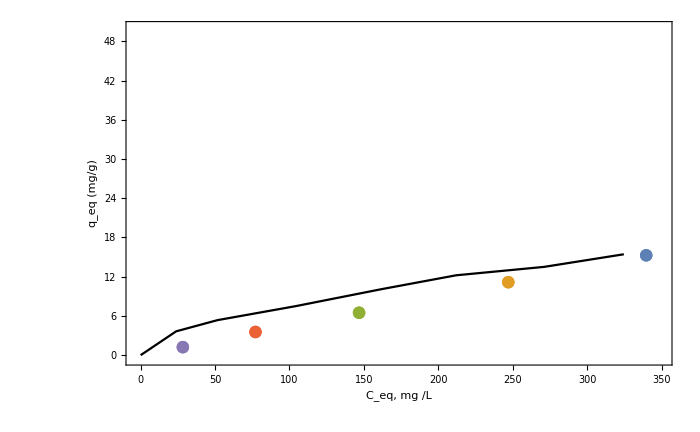

```mathematica
Show[ListPlot[datavalidation,PlotStyle->{Blue,Red,Black},LabelStyle->{FontSize->25,FontFamily->"Times"},PlotRange->{{-2.8,350},{-0.5,50}},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True,LabelStyle->{FontSize->25,FontFamily->"Times"},FrameLabel->{"C_eq, mg /L","q_eq (mg/g)"},Joined->True],ListPlot[{point1,point2,point3,point4,point5}]]
```

## Fig 6a). Kinetics and Isotherms (3 -COOH, 3 -OH)

### 1 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

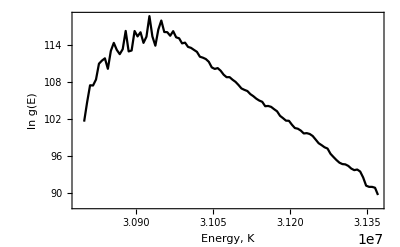

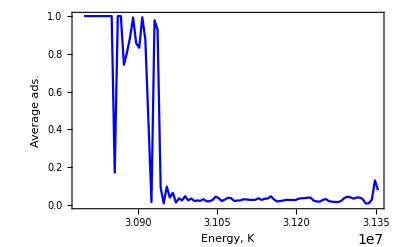

```mathematica
decimals=70;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba1=ToExpression[Import[basePath<>"L20_As1_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba1[[1]]],0];
latticeData=prueba1/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data1=Import[basePath<>"L20_As1_GO3_H1_DOS.txt","Table"];
data1=N[Rationalize[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],10^-decimals],decimals];
ListPlot[data1,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial1=Import[basePath<>"L20_As1_GO3_H1_Nt.txt","Table"];
partial1=N[Rationalize[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],10^-decimals],decimals];
ListPlot[partial1,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

111.613130466260211897455461794453505122561963327865977980775215347613

NDSolve::nderr: Error test failure at t == 0.01083074006736800683634670524472957434280720641669393924112415234706312; unable to continue.

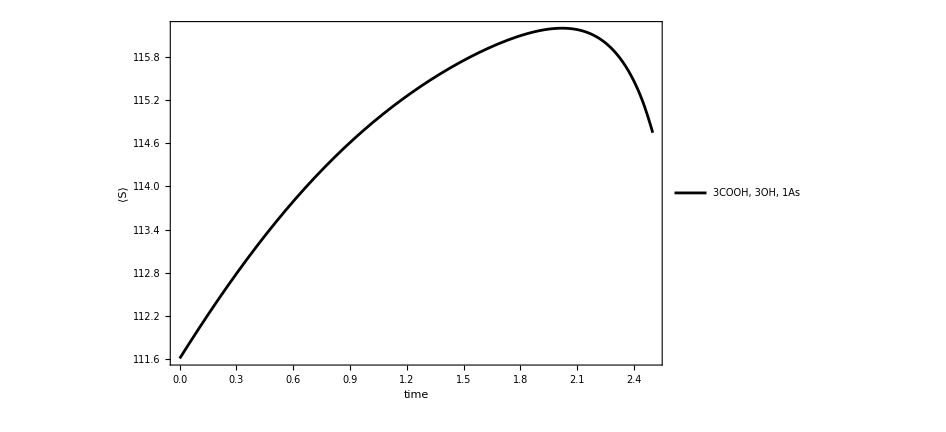

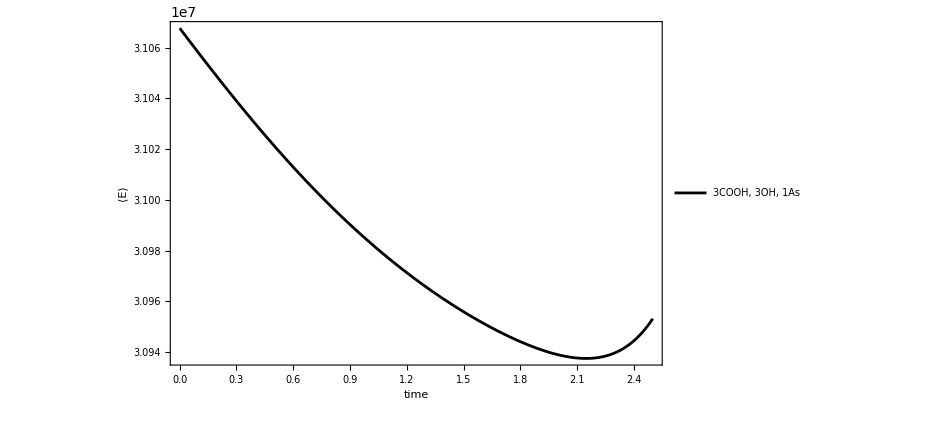

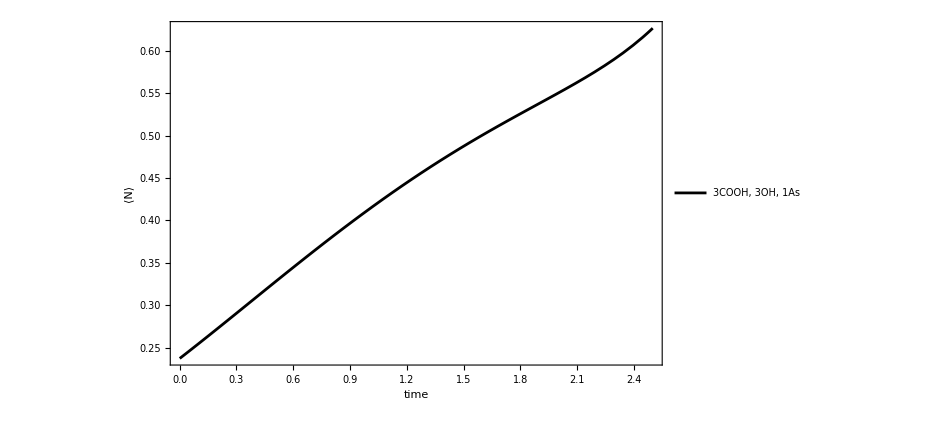

```mathematica
npar1=Length[partial1];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar1-1),200,1/200],{i,1,npar1}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
sCurrent=monitor2[p0,Last[Transpose[data1]][[1;;npar1]]]
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],Last[Transpose[partial1]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data1]][[1;;npar1]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT1=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT1[t1],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"3COOH, 3OH, 1As"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{Black,Black,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S13=plotAdsorption[time,1]
E13=plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 2 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

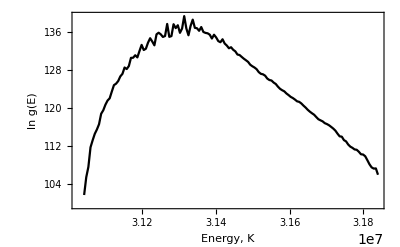

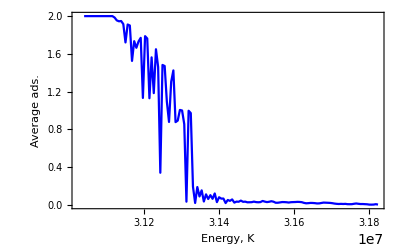

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba2=ToExpression[Import[basePath<>"L20_As2_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba2[[1]]],0];
latticeData=prueba2/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data2=Import[basePath<>"L20_As2_GO3_H1_DOS.txt","Table"];
data2=N[Rationalize[Transpose[{First[Transpose[data2]] correctunits,Last[Transpose[data2]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial2=Import[basePath<>"L20_As2_GO3_H1_Nt.txt","Table"];
partial2=N[Rationalize[Transpose[{First[Transpose[partial2]] correctunits,Last[Transpose[partial2]]}],10^-decimals],decimals];
ListPlot[partial2,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

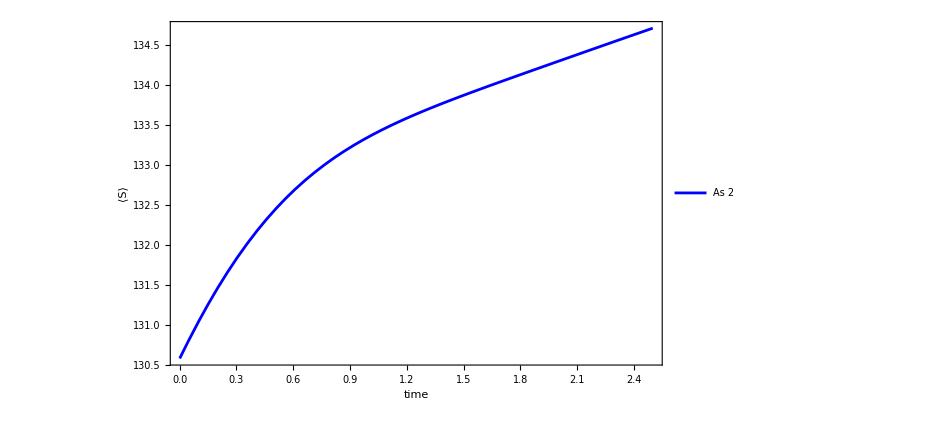

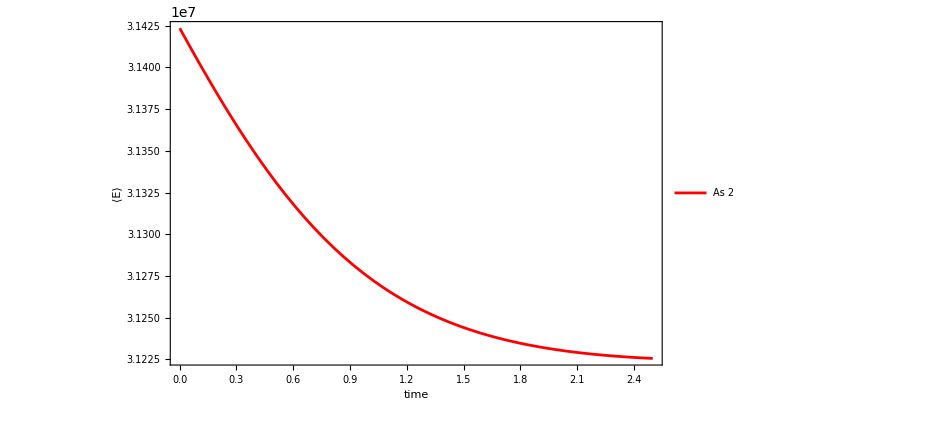

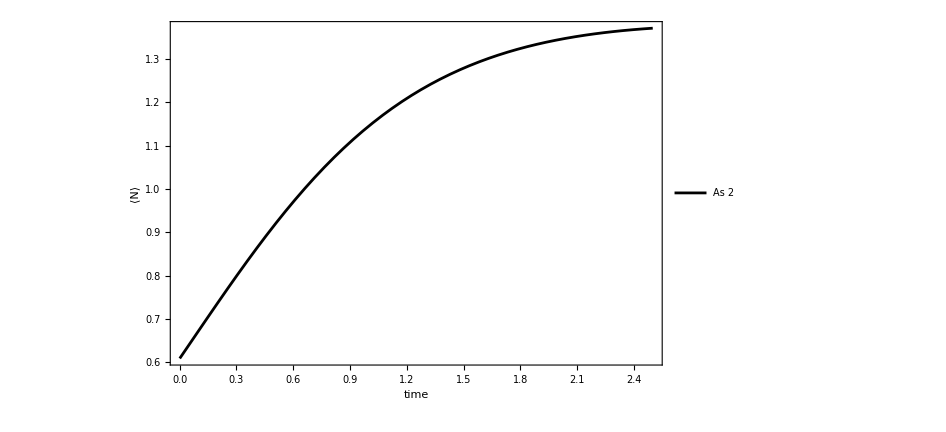

```mathematica
npar2=Length[partial2];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar2-1),200,1/200],{i,1,npar2}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],Last[Transpose[partial2]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data2]][[1;;npar2]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT2=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT2[t1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 3 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

-Graphics-

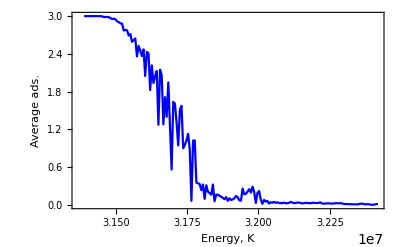

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba3=ToExpression[Import[basePath<>"L20_As3_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba3[[1]]],0];
latticeData=prueba3/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data3=Import[basePath<>"L20_As3_GO3_H1_DOS.txt","Table"];
data3=N[Rationalize[Transpose[{First[Transpose[data3]] correctunits,Last[Transpose[data3]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial3=Import[basePath<>"L20_As3_GO3_H1_Nt.txt","Table"];
partial3=N[Rationalize[Transpose[{First[Transpose[partial3]] correctunits,Last[Transpose[partial3]]}],10^-decimals],decimals];
ListPlot[partial3,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

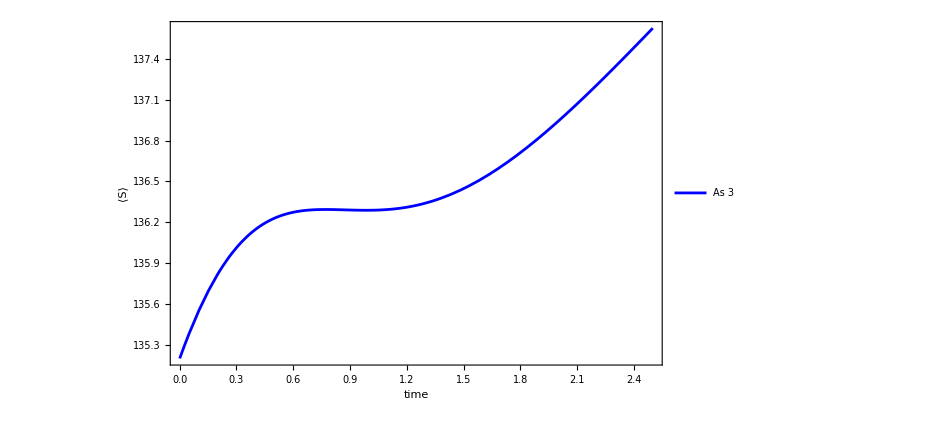

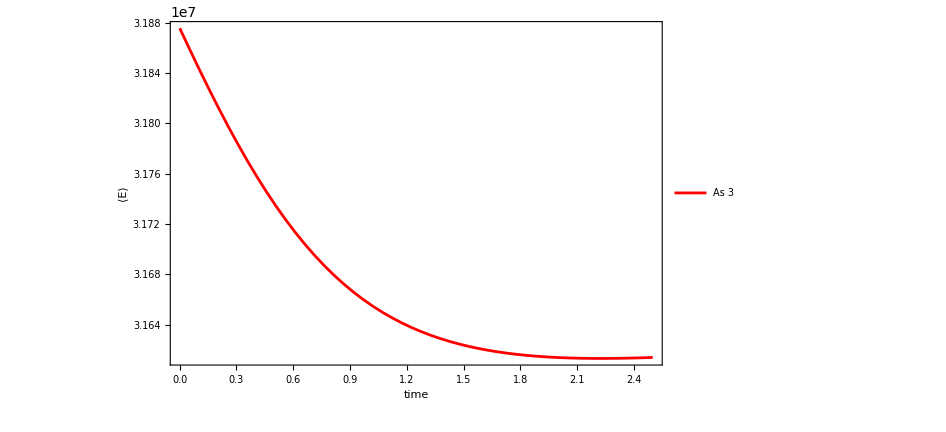

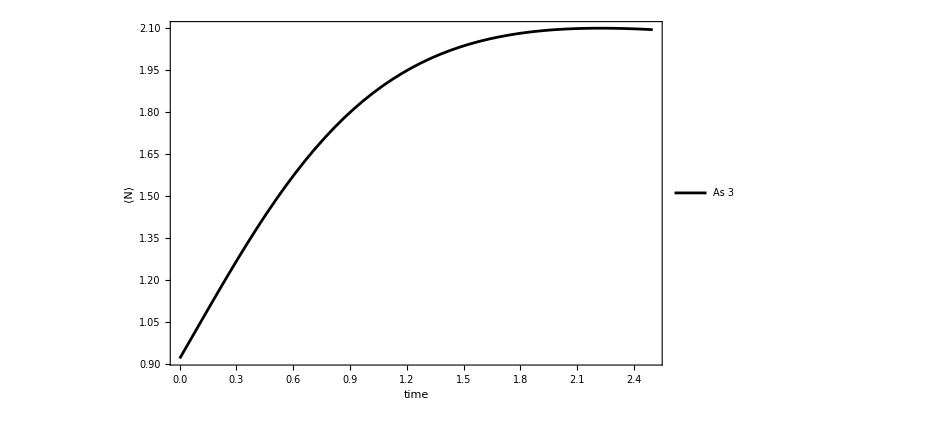

```mathematica
npar3=Length[partial3];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar3-2),1/20,1/200],{i,1,npar3}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],Last[Transpose[partial3]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data3]][[1;;npar3]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT3=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT3[t1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 3"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 4 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

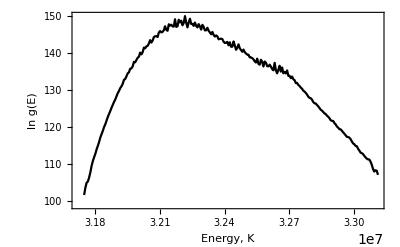

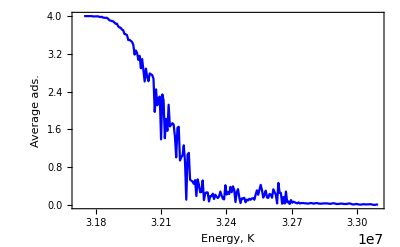

```mathematica
decimals=70;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba4=ToExpression[Import[basePath<>"L20_As4_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba4[[1]]],0];
latticeData=prueba4/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data4=Import[basePath<>"L20_As4_GO3_H1_DOS.txt","Table"];
data4=N[Rationalize[Transpose[{First[Transpose[data4]] correctunits,Last[Transpose[data4]]}],10^-decimals],decimals];
ListPlot[data4,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial4=Import[basePath<>"L20_As4_GO3_H1_Nt.txt","Table"];
partial4=N[Rationalize[Transpose[{First[Transpose[partial4]] correctunits,Last[Transpose[partial4]]}],10^-decimals],decimals];
ListPlot[partial4,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

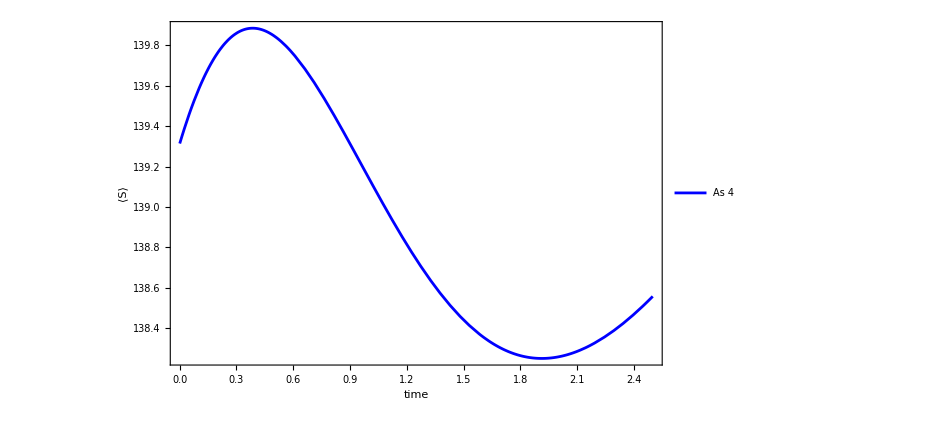

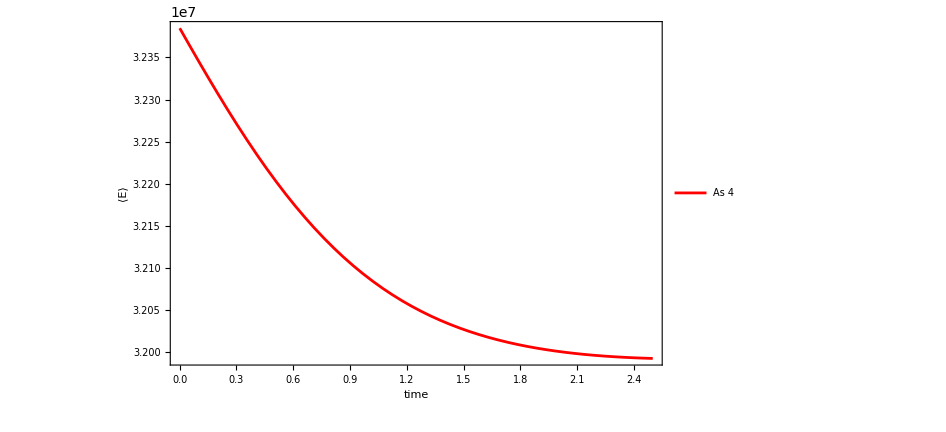

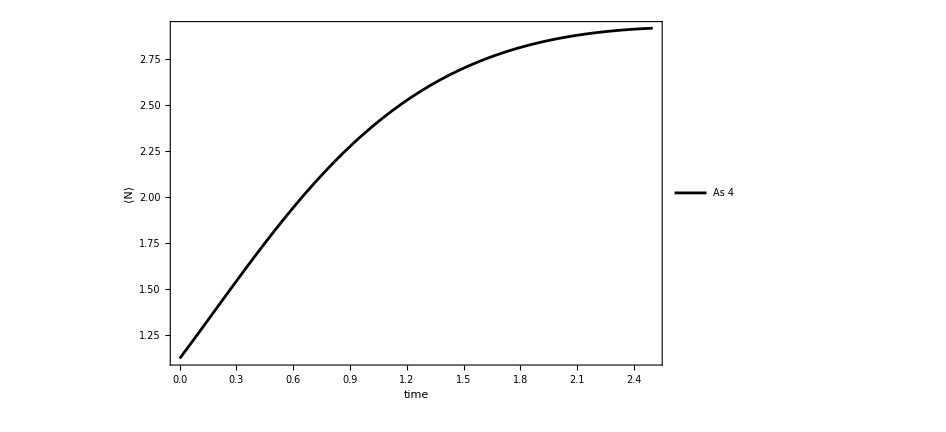

```mathematica
npar4=Length[partial4];
time=2.5;
values={τ->28};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar4-2),1/20,1/200],{i,1,npar4}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],Last[Transpose[partial4]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data4]][[1;;npar4]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT4=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT4[t1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 4"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 5 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

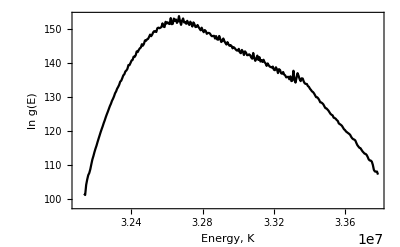

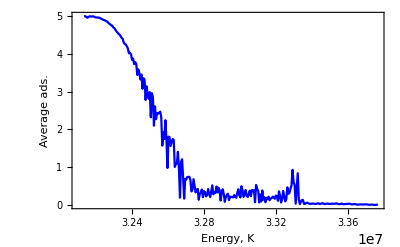

```mathematica
decimals=70;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba5=ToExpression[Import[basePath<>"L20_As5_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba5[[1]]],0];
latticeData=prueba5/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data5=Import[basePath<>"L20_As5_GO3_H1_DOS.txt","Table"];
data5=N[Rationalize[Transpose[{First[Transpose[data5]] correctunits,Last[Transpose[data5]]}],10^-decimals],decimals];
ListPlot[data5,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial5=Import[basePath<>"L20_As5_GO3_H1_Nt.txt","Table"];
partial5=N[Rationalize[Transpose[{First[Transpose[partial5]] correctunits,Last[Transpose[partial5]]}],10^-decimals],decimals];
ListPlot[partial5,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

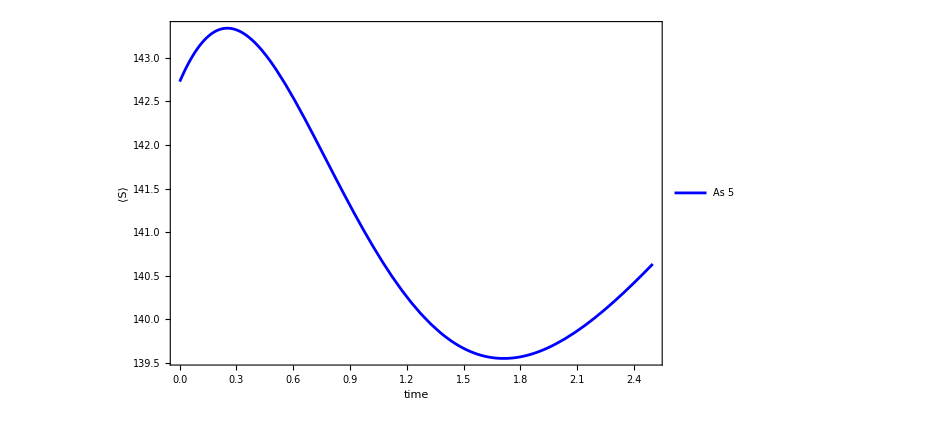

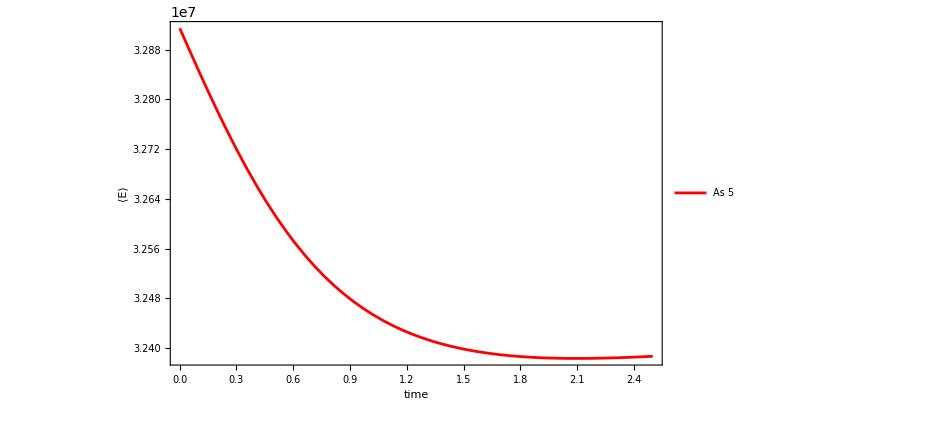

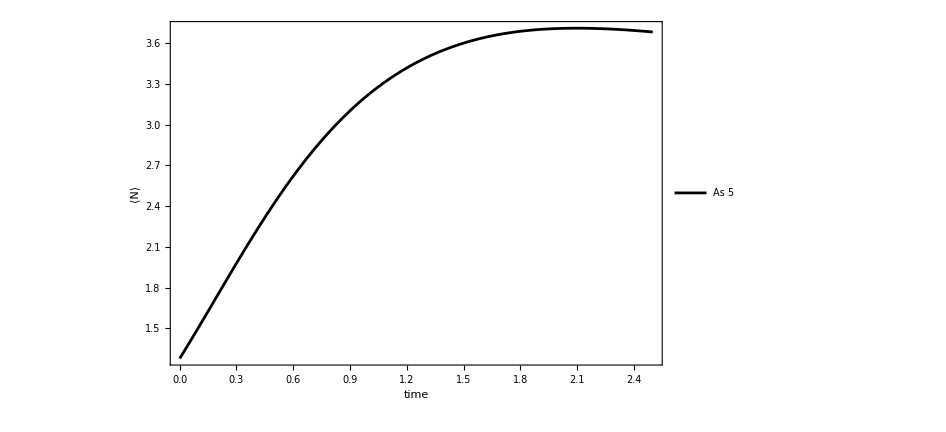

```mathematica
npar5=Length[partial5];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar5-2),1/20,1/200],{i,1,npar5}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],Last[Transpose[partial5]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data5]][[1;;npar5]]];
monitr=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT5=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT5[t1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 5"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 6 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

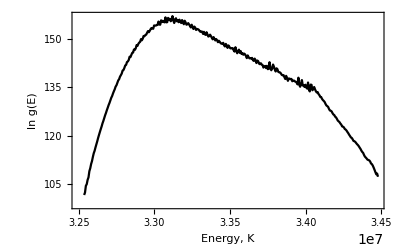

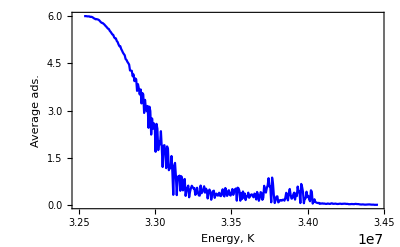

```mathematica
decimals=70;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba6=ToExpression[Import[basePath<>"L20_As6_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba6[[1]]],0];
latticeData=prueba6/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data6=Import[basePath<>"L20_As6_GO3_H1_DOS.txt","Table"];
data6=N[Rationalize[Transpose[{First[Transpose[data6]] correctunits,Last[Transpose[data6]]}],10^-decimals],decimals];
ListPlot[data6,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial6=Import[basePath<>"L20_As6_GO3_H1_Nt.txt","Table"];
partial6=N[Rationalize[Transpose[{First[Transpose[partial6]] correctunits,Last[Transpose[partial6]]}],10^-decimals],decimals];
ListPlot[partial6,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

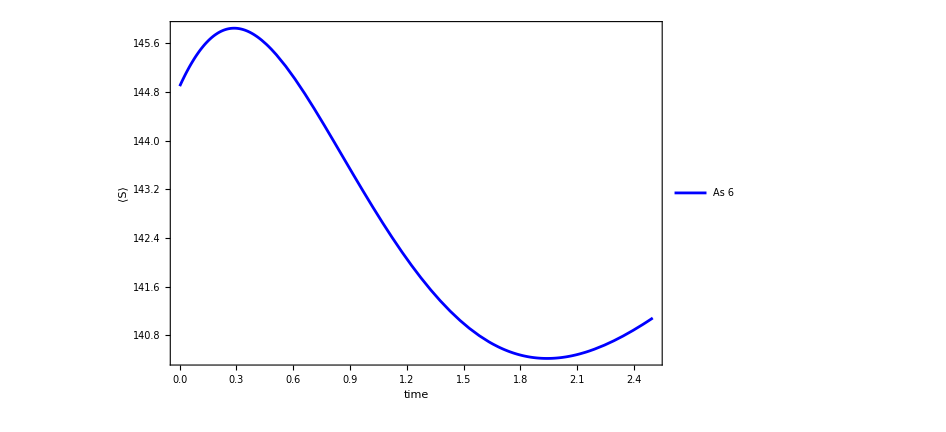

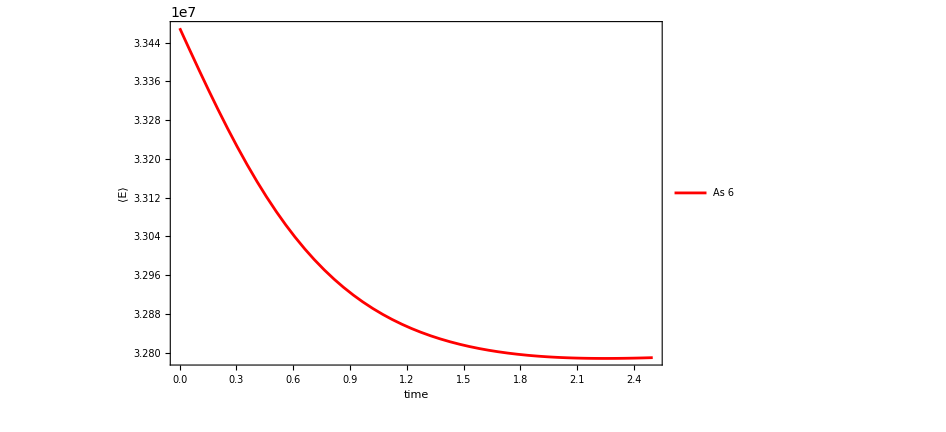

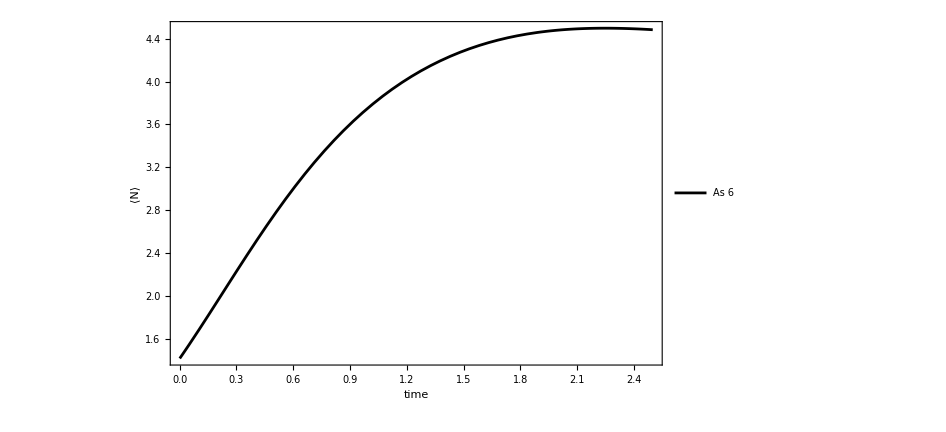

```mathematica
npar6=Length[partial6];
time=2.5;
values={τ->24};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar6-2),1/20,1/200],{i,1,npar6}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],Last[Transpose[partial6]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data6]][[1;;npar6]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT6=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT6[t1],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 6"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 7 As, 1 H^+, 3 -COOH, 3 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO3/

Lattice size = {20,20}

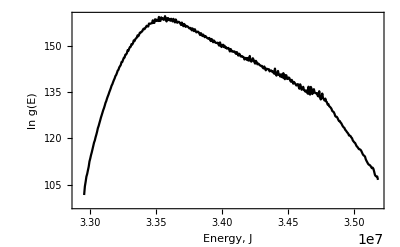

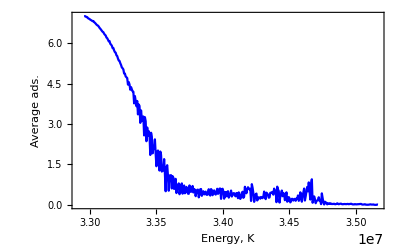

```mathematica
decimals=70;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO3/"]
prueba7=ToExpression[Import[basePath<>"L20_As7_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba7[[1]]],0];
latticeData=prueba7/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data7=Import[basePath<>"L20_As7_GO3_H1_DOS.txt","Table"];
data7=N[Rationalize[Transpose[{First[Transpose[data7]] correctunits,Last[Transpose[data7]]}],10^-decimals],decimals];
ListPlot[data7,Joined->True,FrameLabel->{"Energy, J","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial7=Import[basePath<>"L20_As7_GO3_H1_Nt.txt","Table"];
partial7=N[Rationalize[Transpose[{First[Transpose[partial7]] correctunits,Last[Transpose[partial7]]}],10^-decimals],decimals];
ListPlot[partial7,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

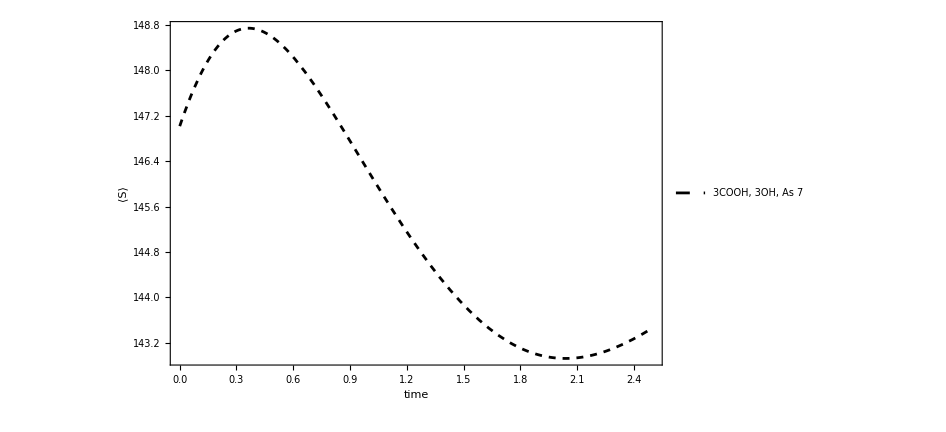

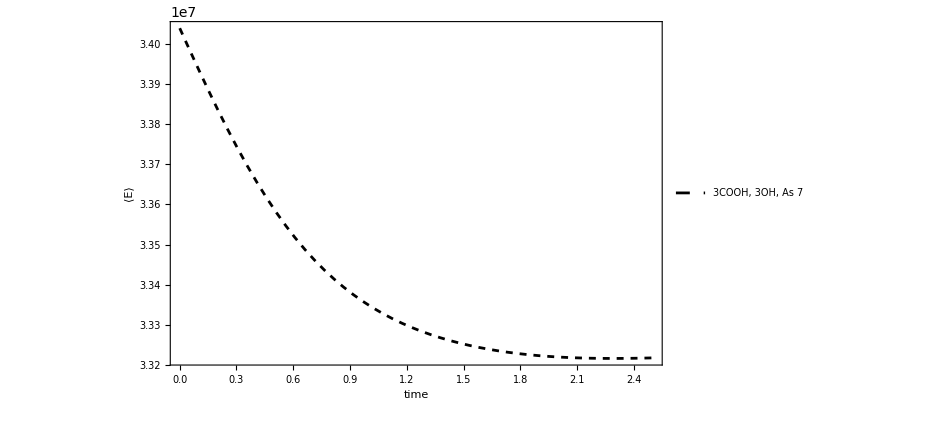

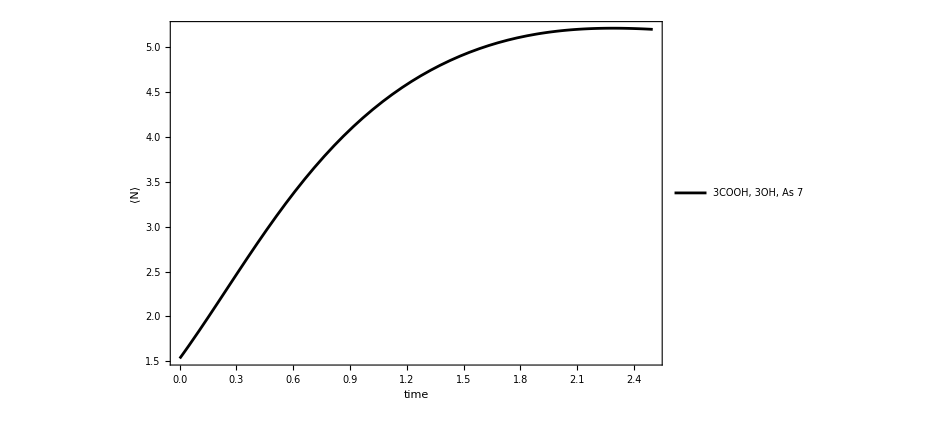

```mathematica
npar7=Length[partial7];
time=2.5;
values={τ->25};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar7-2),1/20,1/200],{i,1,npar7}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],Last[Transpose[partial7]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data7]][[1;;npar7]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT7=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT7[t1],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"3COOH, 3OH, As 7"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{{Black, Dashed},{Black,Dashed},Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S73=plotAdsorption[time,1]
E73=plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### Plots Kinetics

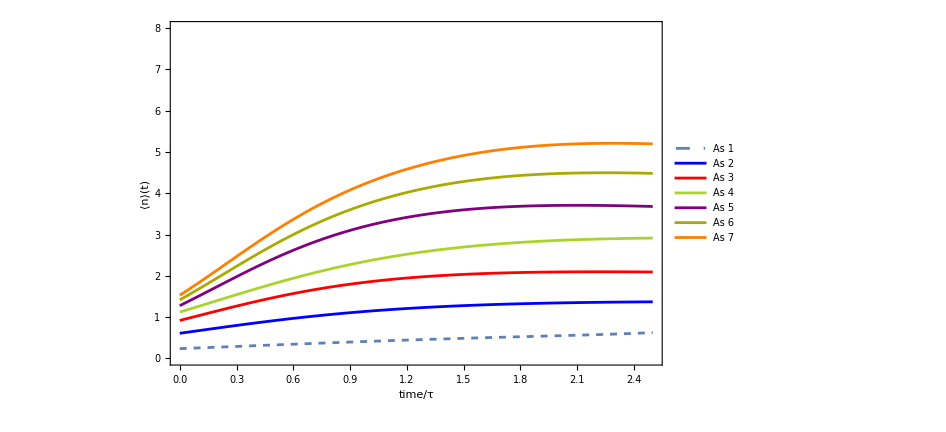

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT3[t],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT4[t],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT5[t],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]
}
,{t,0,time},PlotRange->{0,8},FrameLabel->{"time/τ","⟨n⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 2","As 3","As 4","As 5","As 6","As 7"},LabelStyle->{FontFamily->"Times",FontSize->22},LegendLayout->{"Column",2}],{0.2,0.8}],LabelStyle->{FontSize->30,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

### Plots Isotherms

```mathematica
lista3={
qcEAs[prueba1,
1,adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]]],
qcEAs[prueba2,
2,adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]],
qcEAs[prueba3,
3,adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]]],
qcEAs[prueba4,
4,adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]]],
qcEAs[prueba5,
5,adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]]],
qcEAs[prueba6,
6,adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]]],
qcEAs[prueba7,
7,adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]]
}
ListPlot[lista3,LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,PlotRange->Automatic,Axes->False,Frame->True,FrameLabel->{"C_eq(mg L^-1)","q (μg g^-1)"},Joined->False]
```

ReplaceAll::reps: {p'[t]==disspn[p[t],t,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ReplaceAll::reps: {p'[t]==disspn[p[t],t,5787.0234532576478148570089811245420550416636075132258546174793290595928589871879 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

ReplaceAll::reps: {p'[t]==disspn[p[t],t,5787.0234532576478148570089811245420550416636075132258546174793290595928589871879 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧},{ComplexInfinity,68.9868 $Failed⟦1;;2⟧}}

-Graphics-

### Plots Energy, entropy, entropy generation

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[1]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[1]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨S⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[2]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[2]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨E⟩(t),K"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

ReplaceAll::reps: {p'[0.0000510714]==disspn[p[0.0000510714],0.0000510714,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

ReplaceAll::reps: {p'[0.0000510714]==disspn[p[0.0000510714],0.0000510714,5787.02 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {p'[0.0510715]==disspn[p[0.0510715],0.0510715,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {p'[0.0000510714]==disspn[p[0.0000510714],0.0000510714,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

ReplaceAll::reps: {p'[0.0510715]==disspn[p[0.0510715],0.0510715,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

ReplaceAll::reps: {p'[0.102092]==disspn[p[0.102092],0.102092,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

### Plots Entropy generation

```mathematica
entgen={{adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]-
adsortion[ρttSEAQT1[0],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]},
{adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]-
adsortion[ρttSEAQT2[0],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]},
{adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]-
adsortion[ρttSEAQT3[0],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]},
{adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]-
adsortion[ρttSEAQT4[0],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]},{adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]-
adsortion[ρttSEAQT5[0],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]},
{adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]-
adsortion[ρttSEAQT6[0],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]},
{adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]],
adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]-
adsortion[ρttSEAQT7[0],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]}}
DS3=ListPlot[entgen,Frame->True,PlotRange->{{0,5},{0,35}},FrameLabel->{"⟨N⟩_eq","σ"},PlotMarkers->{Black,10},LabelStyle->{FontSize->19,FontFamily->"Times"},PlotLegends->Placed[LineLegend[{"3COOH, 3OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.2,0.6}]]
```

ReplaceAll::reps: {p'[t]==disspn[p[t],t,5787.023453257647814857008981124542055041663607513225854617479329059593 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 2 in $Failed.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

ReplaceAll::reps: {p'[t]==disspn[p[t],t,5787.0234532576478148570089811245420550416636075132258546174793290595928589871879 $Failed,$Failed⟦1;;2⟧,$Failed]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}},{$Failed⟦1;;2⟧,{0. $Failed,0}}}

-Graphics-

## Fig 6b). Kinetics and Isotherms (6 -COOH, 6 -OH)

### 1 As, 1 H^+, 6 -COOH, 6 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO6/

Lattice size = {20,20}

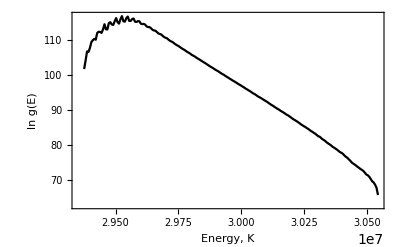

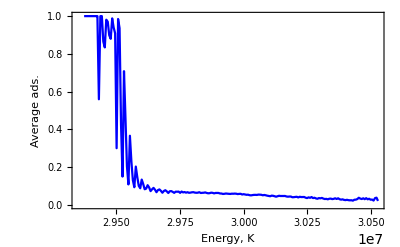

```mathematica
decimals=69;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba1=ToExpression[Import[basePath<>"L20_As1_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba1[[1]]],0];
latticeData=prueba1/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data1=Import[basePath<>"L20_As1_GO6_H1_DOS.txt","Table"];
data1=N[Rationalize[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],10^-decimals],decimals];
ListPlot[data1,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial1=Import[basePath<>"L20_As1_GO6_H1_Nt.txt","Table"];
partial1=N[Rationalize[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],10^-decimals],decimals];
ListPlot[partial1,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

103.1637693753941754826067250720066805342296837842227887176511768187

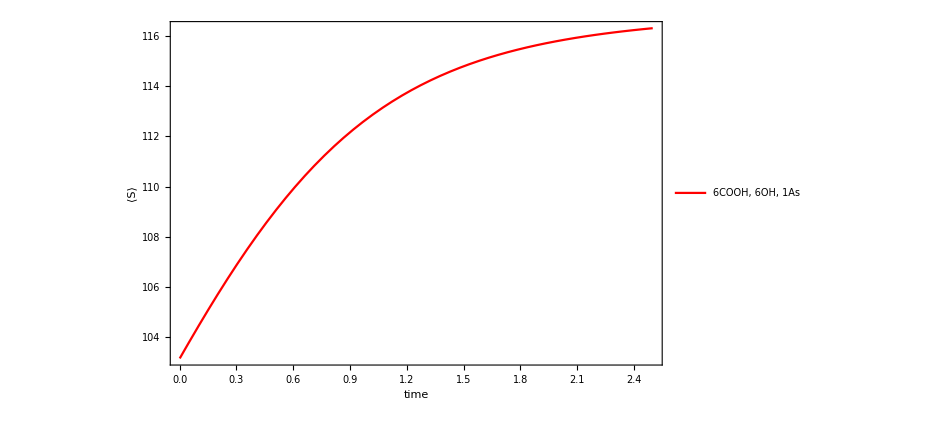

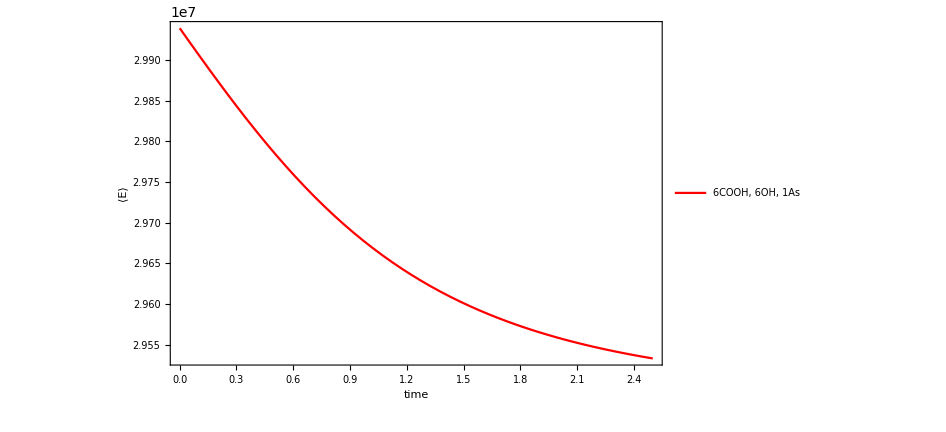

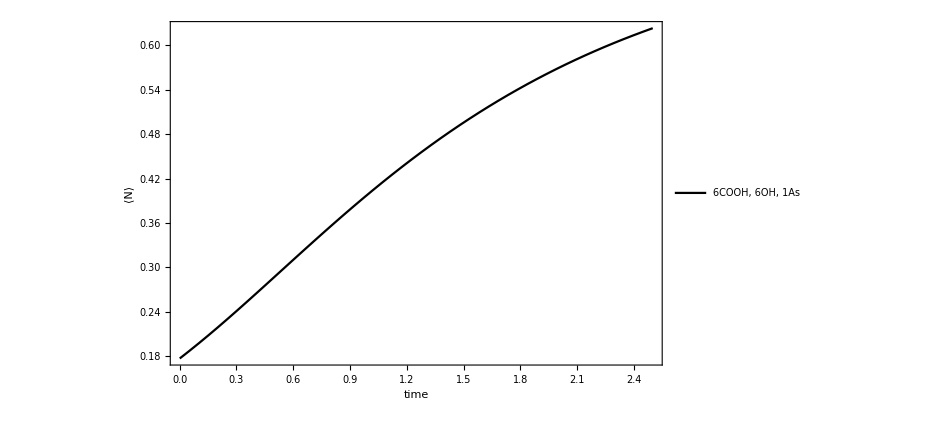

```mathematica
npar1=Length[partial1];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar1-1),200,1/200],{i,1,npar1}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
sCurrent=monitor2[p0,Last[Transpose[data1]][[1;;npar1]]]
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],Last[Transpose[partial1]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data1]][[1;;npar1]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT1=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT1[t1],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"6COOH, 6OH, 1As"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{Red,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S16=plotAdsorption[time,1]
E16=plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 2 As, 1 H^+, 6 -COOH, 6 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO6/

Lattice size = {20,20}

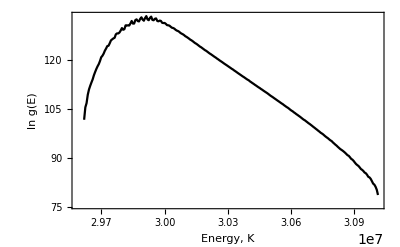

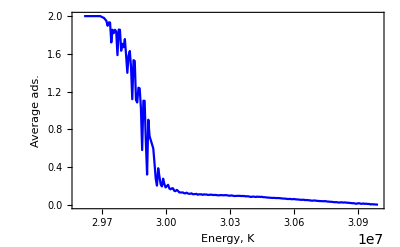

```mathematica
decimals=69;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba2=ToExpression[Import[basePath<>"L20_As2_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba2[[1]]],0];
latticeData=prueba2/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data2=Import[basePath<>"L20_As2_GO6_H1_DOS.txt","Table"];
data2=N[Rationalize[Transpose[{First[Transpose[data2]] correctunits,Last[Transpose[data2]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial2=Import[basePath<>"L20_As2_GO6_H1_Nt.txt","Table"];
partial2=N[Rationalize[Transpose[{First[Transpose[partial2]] correctunits,Last[Transpose[partial2]]}],10^-decimals],decimals];
ListPlot[partial2,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

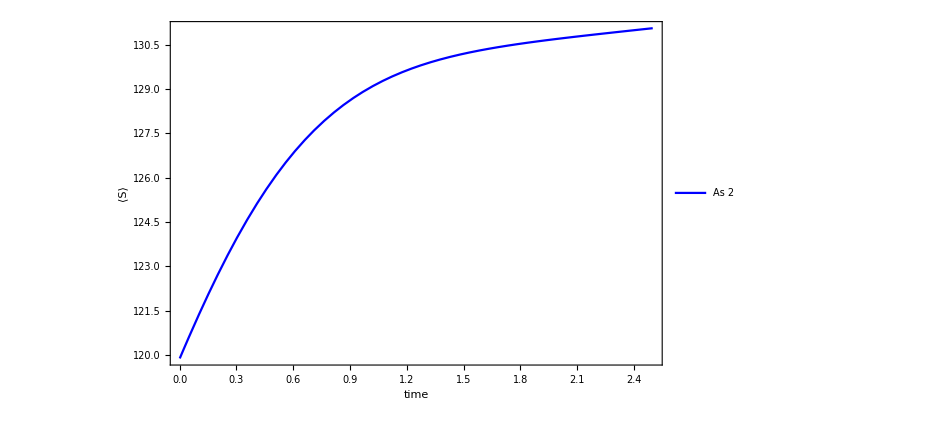

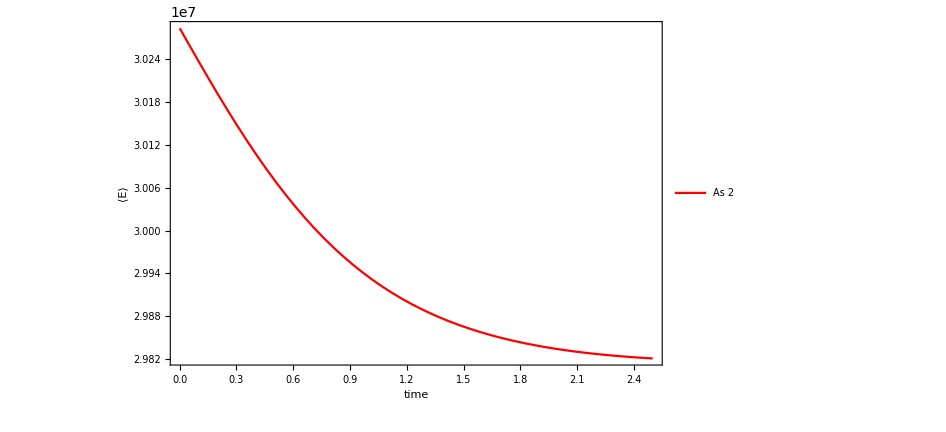

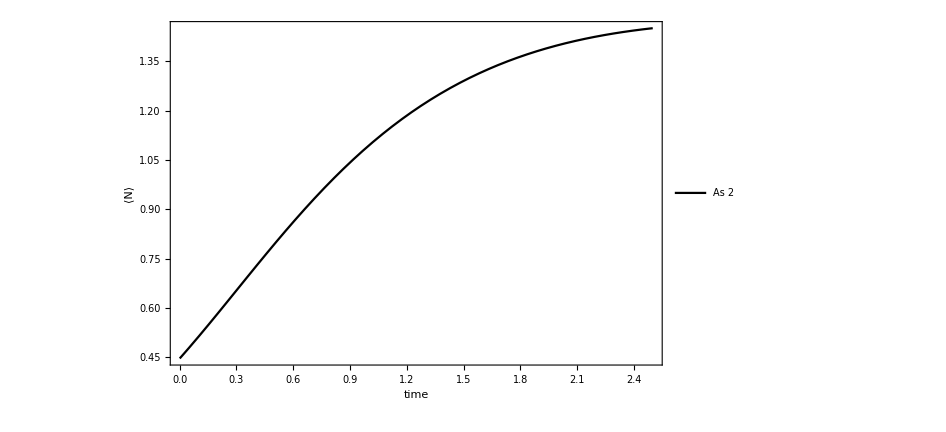

```mathematica
npar2=Length[partial2];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar2-1),200,1/200],{i,1,npar2}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],Last[Transpose[partial2]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data2]][[1;;npar2]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT2=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT2[t1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 3 As, 1 H^+, 6 -COOH, 6-OH

Lattice size = {20,20}

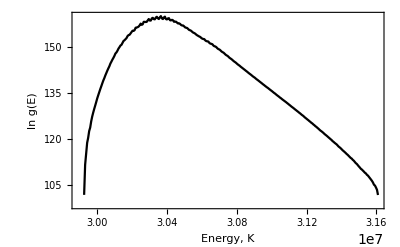

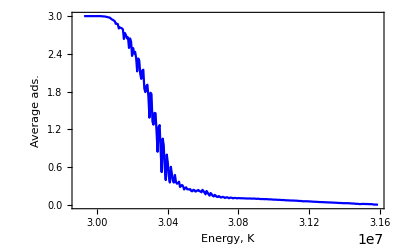

```mathematica
decimals=60;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba3=ToExpression[Import[basePath<>"L20_As3_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba3[[1]]],0];
latticeData=prueba3/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data3=Import[basePath<>"L20_As3_GO6_H1_DOS.txt","Table"];
data3=N[Rationalize[Transpose[{First[Transpose[data3]] correctunits,Last[Transpose[data3]]}],10^-decimals],decimals];
ListPlot[data3,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial3=Import[basePath<>"L20_As3_GO6_H1_Nt.txt","Table"];
partial3=N[Rationalize[Transpose[{First[Transpose[partial3]] correctunits,Last[Transpose[partial3]]}],10^-decimals],decimals];
ListPlot[partial3,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

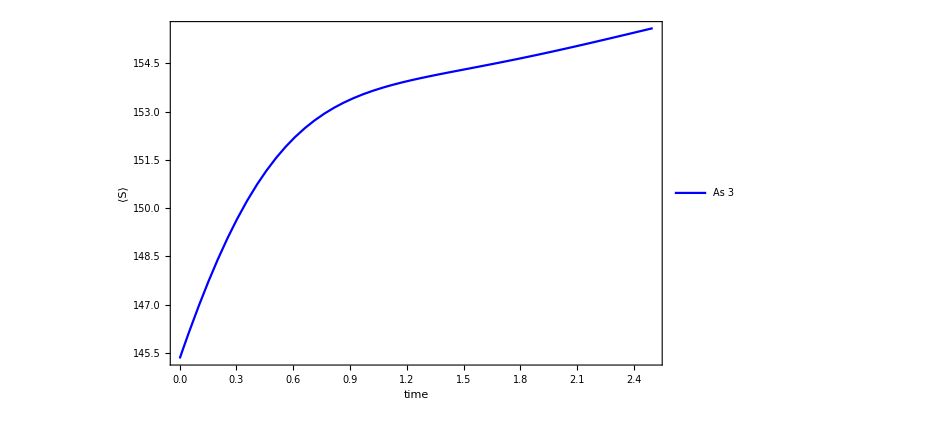

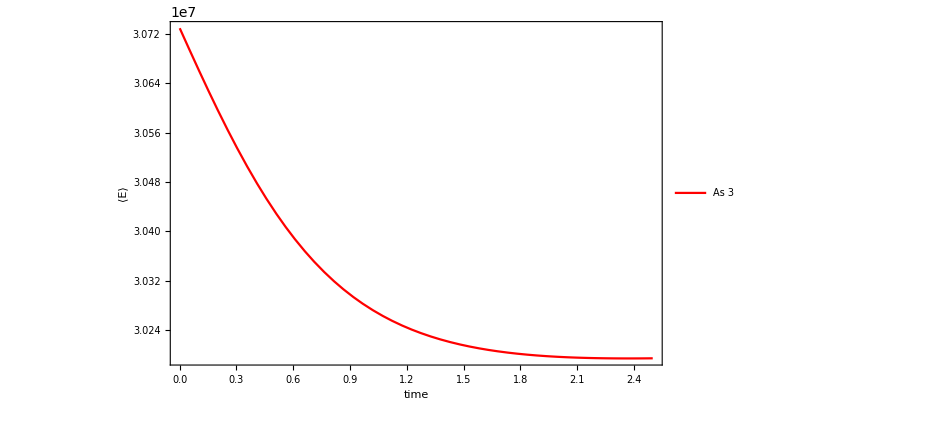

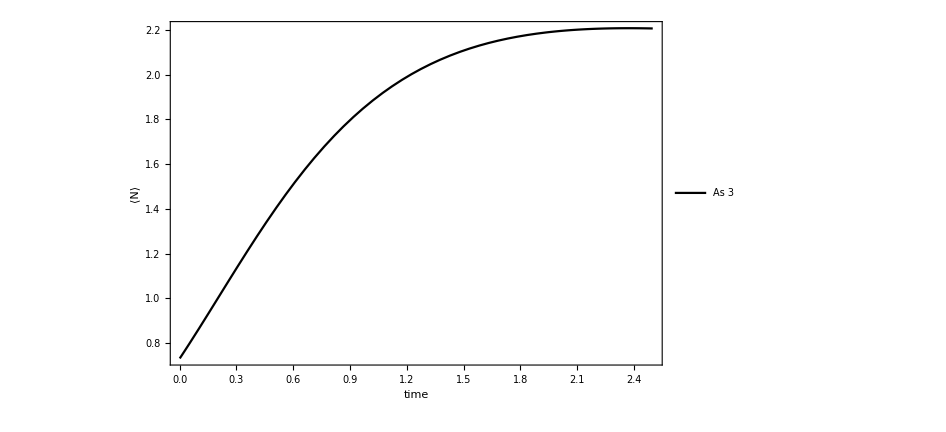

```mathematica
npar3=Length[partial3];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar3-2),1/20,1/200],{i,1,npar3}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],Last[Transpose[partial3]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data3]][[1;;npar3]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT3=p/. First[sol1[[1]]];

plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT3[t1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 3"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 4 As, 1 H^+, 6 -COOH, 6 -OH

Lattice size = {20,20}

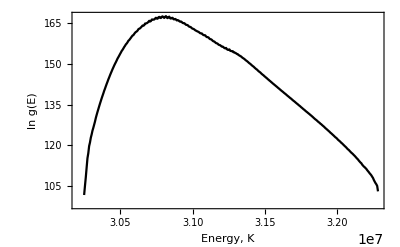

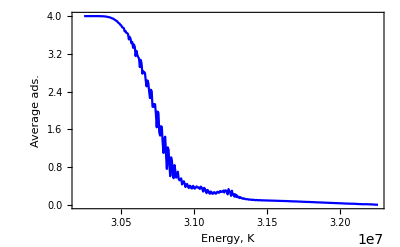

```mathematica
decimals=60;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba4=ToExpression[Import[basePath<>"L20_As4_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba4[[1]]],0];
latticeData=prueba4/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data4=Import[basePath<>"L20_As4_GO6_H1_DOS.txt","Table"];
data4=N[Rationalize[Transpose[{First[Transpose[data4]] correctunits,Last[Transpose[data4]]}],10^-decimals],decimals];
ListPlot[data4,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial4=Import[basePath<>"L20_As4_GO6_H1_Nt.txt","Table"];
partial4=N[Rationalize[Transpose[{First[Transpose[partial4]] correctunits,Last[Transpose[partial4]]}],10^-decimals],decimals];
ListPlot[partial4,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

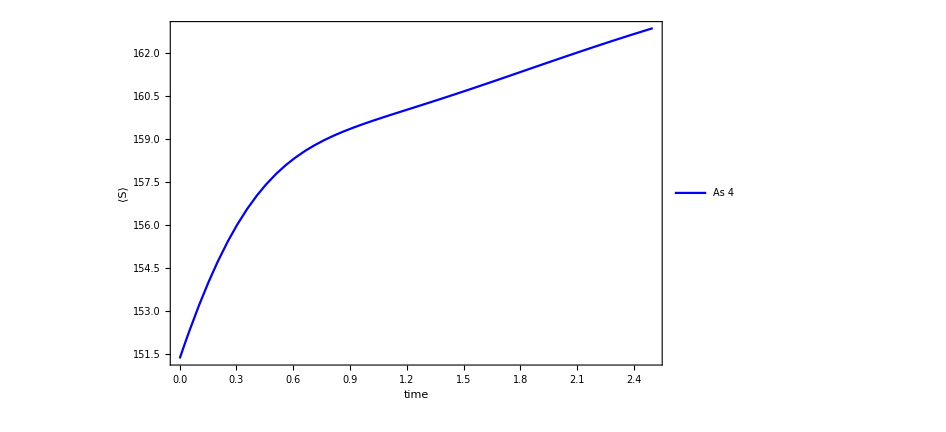

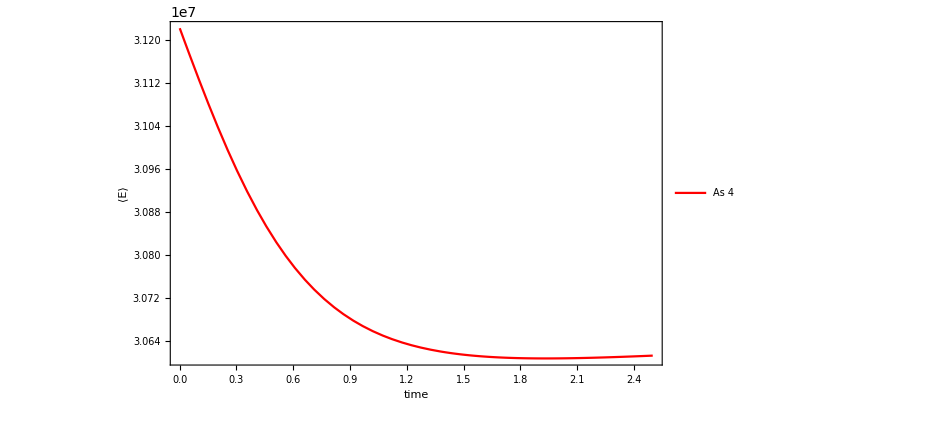

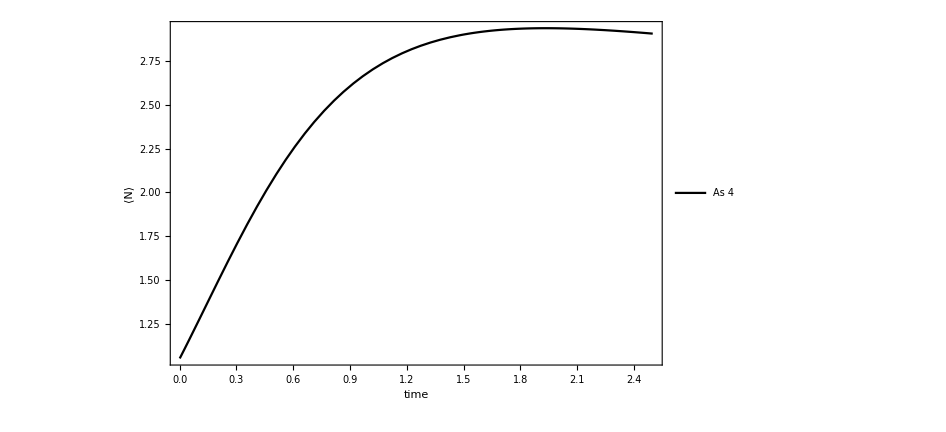

```mathematica
npar4=Length[partial4];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar4-2),1/20,1/200],{i,1,npar4}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],Last[Transpose[partial4]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data4]][[1;;npar4]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT4=p/. First[sol1[[1]]];

plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT4[t1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 4"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 5 As, 1 H^+, 6 -COOH, 6 -OH

Lattice size = {20,20}

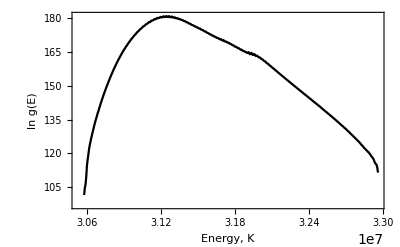

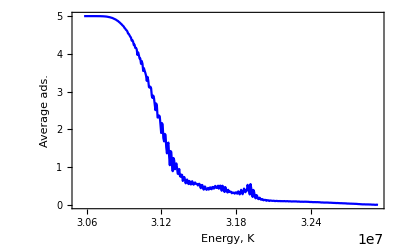

```mathematica
decimals=60;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba5=ToExpression[Import[basePath<>"L20_As5_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba5[[1]]],0];
latticeData=prueba5/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data5=Import[basePath<>"L20_As5_GO6_H1_DOS.txt","Table"];
data5=N[Rationalize[Transpose[{First[Transpose[data5]] correctunits,Last[Transpose[data5]]}],10^-decimals],decimals];
ListPlot[data5,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial5=Import[basePath<>"L20_As5_GO6_H1_Nt.txt","Table"];
partial5=N[Rationalize[Transpose[{First[Transpose[partial5]] correctunits,Last[Transpose[partial5]]}],10^-decimals],decimals];
ListPlot[partial5,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

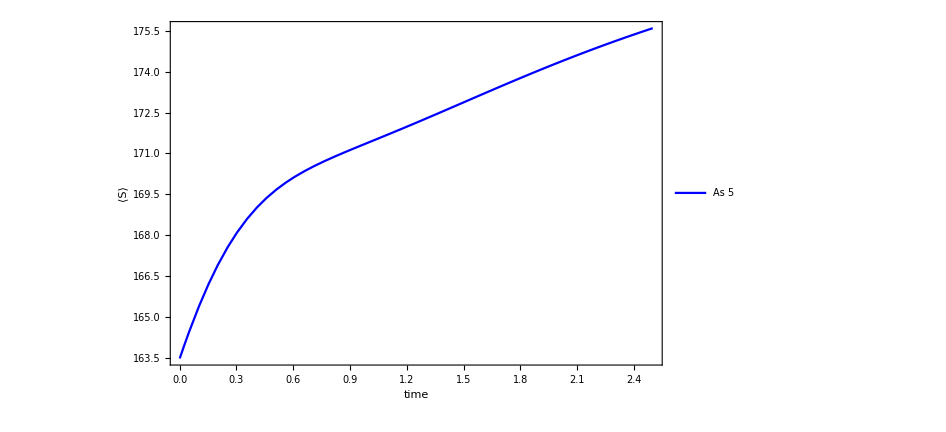

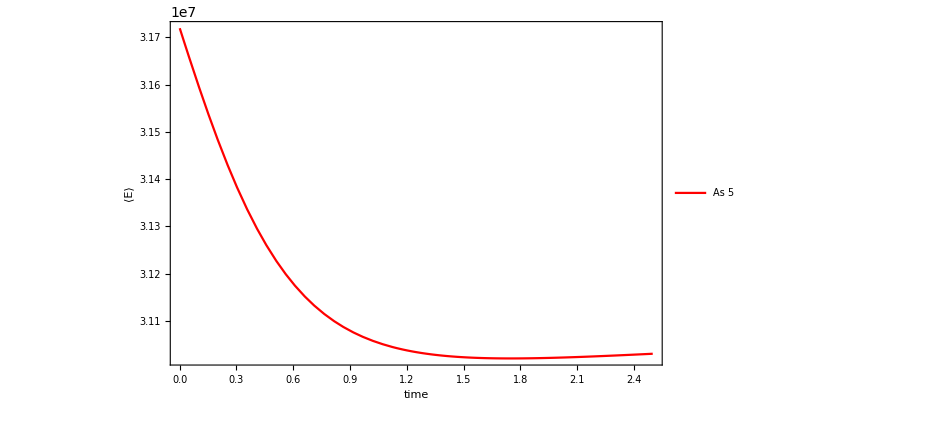

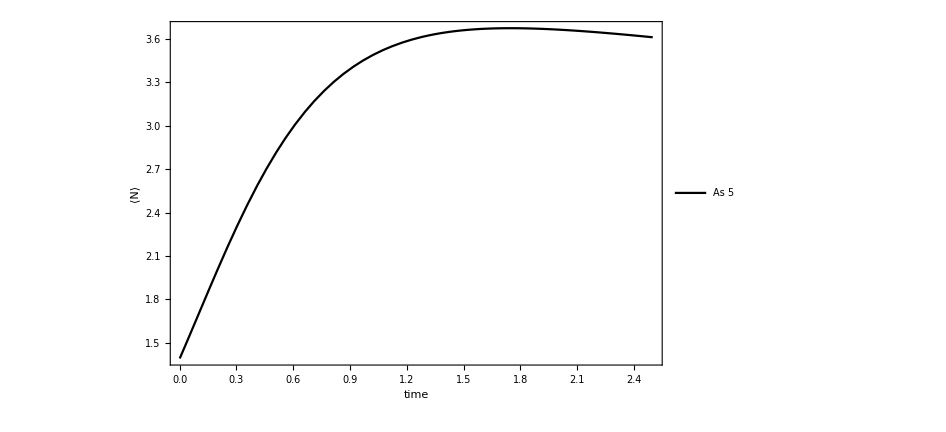

```mathematica
npar5=Length[partial5];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar5-2),1/20,1/200],{i,1,npar5}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],Last[Transpose[partial5]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data5]][[1;;npar5]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT5=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT5[t1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 5"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 6 As, 1 H^+, 6 -COOH,6-OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO6/

Lattice size = {20,20}

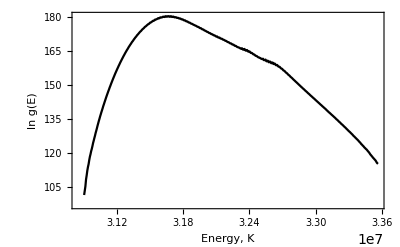

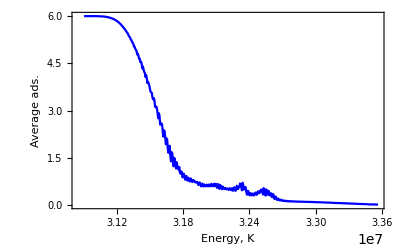

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba6=ToExpression[Import[basePath<>"L20_As6_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba6[[1]]],0];
latticeData=prueba6/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data6=Import[basePath<>"L20_As6_GO6_H1_DOS.txt","Table"];
data6=N[Rationalize[Transpose[{First[Transpose[data6]] correctunits,Last[Transpose[data6]]}],10^-decimals],decimals];
ListPlot[data6,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial6=Import[basePath<>"L20_As6_GO6_H1_Nt.txt","Table"];
partial6=N[Rationalize[Transpose[{First[Transpose[partial6]] correctunits,Last[Transpose[partial6]]}],10^-decimals],decimals];
ListPlot[partial6,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

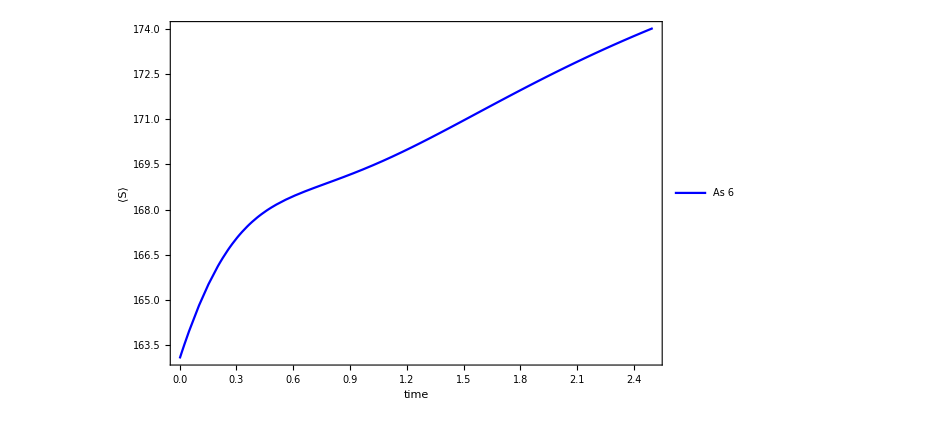

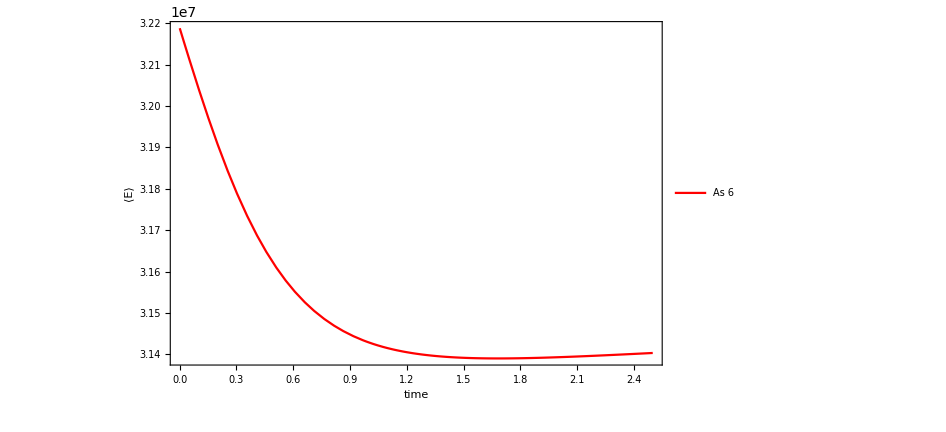

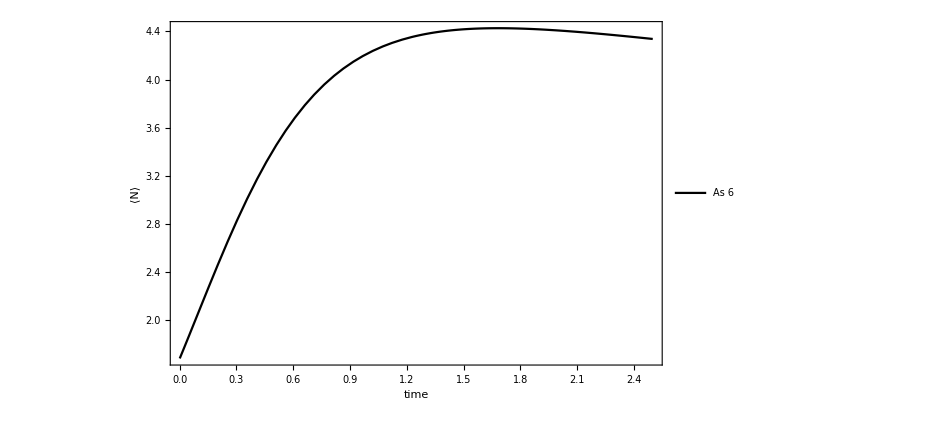

```mathematica
npar6=Length[partial6];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar6-2),1/20,1/200],{i,1,npar6}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],Last[Transpose[partial6]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data6]][[1;;npar6]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT6=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT6[t1],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 6"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 7 As, 1 H^+,6 -COOH, 6 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO6/

Lattice size = {20,20}

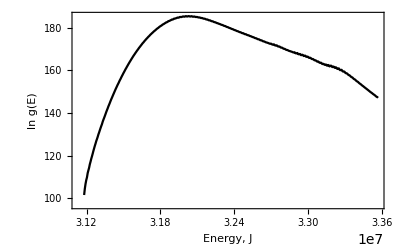

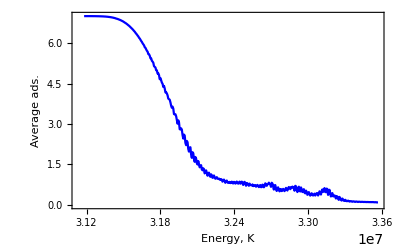

```mathematica
decimals=60;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO6/"]
prueba7=ToExpression[Import[basePath<>"L20_As7_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba7[[1]]],0];
latticeData=prueba7/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data7=Import[basePath<>"L20_As7_GO6_H1_DOS.txt","Table"];
data7=N[Rationalize[Transpose[{First[Transpose[data7]] correctunits,Last[Transpose[data7]]}],10^-decimals],decimals];
ListPlot[data7,Joined->True,FrameLabel->{"Energy, J","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial7=Import[basePath<>"L20_As7_GO6_H1_Nt.txt","Table"];
partial7=N[Rationalize[Transpose[{First[Transpose[partial7]] correctunits,Last[Transpose[partial7]]}],10^-decimals],decimals];
ListPlot[partial7,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

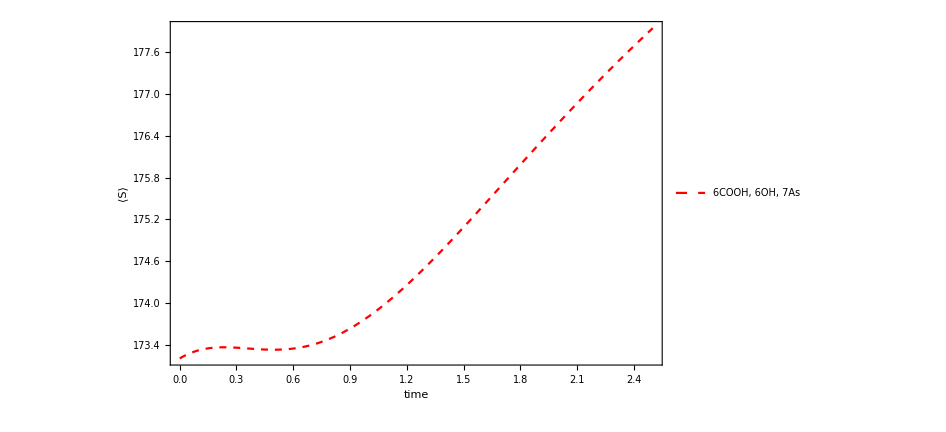

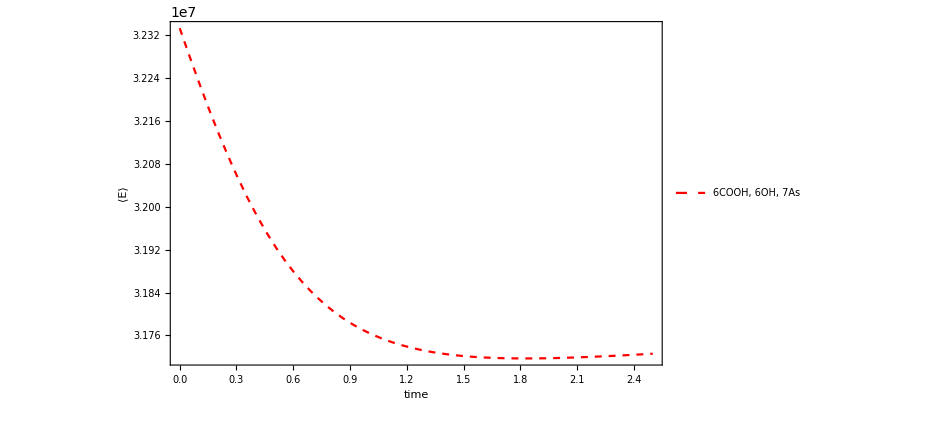

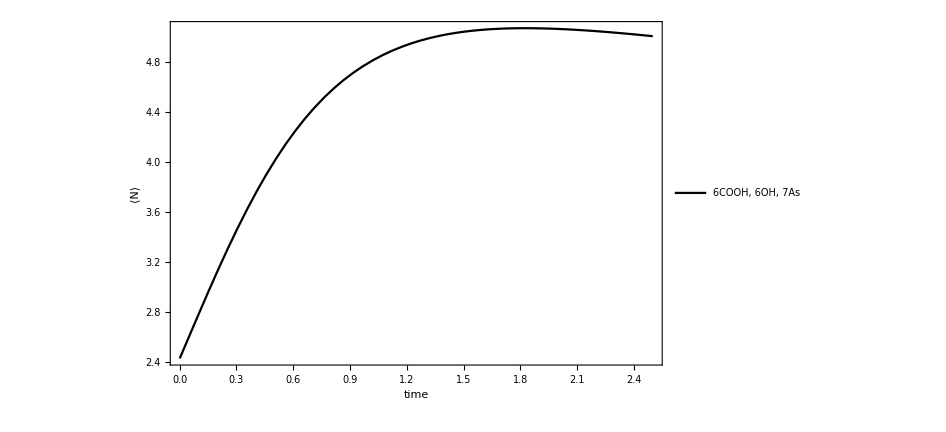

```mathematica
npar7=Length[partial7];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/50000;
data0=Table[If[i<=(npar7-2),1/20,1/200],{i,1,npar7}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],Last[Transpose[partial7]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data7]][[1;;npar7]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor]
ρttSEAQT7=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT7[t1],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"6COOH, 6OH, 7As"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{{Red,Dashed},{Red,Dashed},Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S76=plotAdsorption[time,1]
E76=plotAdsorption[time,2] 
plotAdsorption[time,3]
```

```mathematica
plotAdsorption[time,1];
plotAdsorption[time,2] ;
plotAdsorption[time,3];
```

### Plots Kinetics

```mathematica
(*ρttSEAQT1=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As1.wdx"]
ρttSEAQT2=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As2.wdx"]
ρttSEAQT3=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As3.wdx"]
ρttSEAQT4=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As4.wdx"]
ρttSEAQT5=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As5.wdx"]
ρttSEAQT6=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As6.wdx"]
ρttSEAQT7=Import["/Users/adrianasaldanarobles/Desktop/ent-ene/0_rhos/rho_As7.wdx"]*)
```

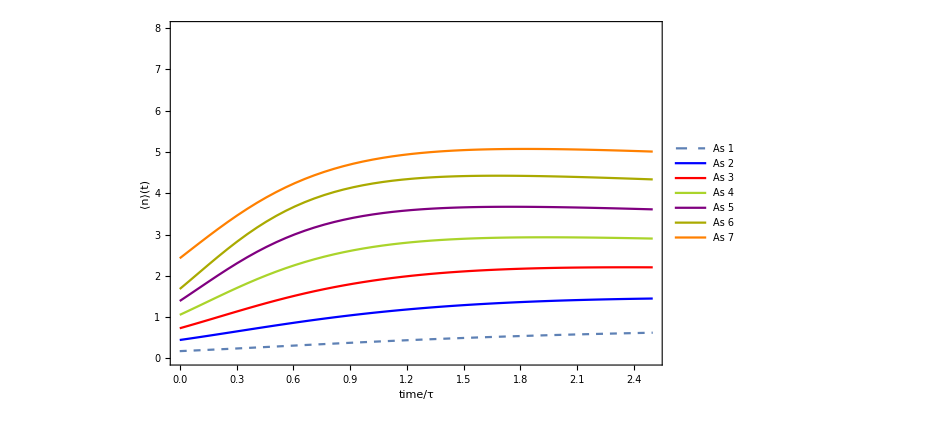

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT3[t],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT4[t],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT5[t],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]
}
,{t,0,time},PlotRange->{0,8},FrameLabel->{"time/τ","⟨n⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 2","As 3","As 4","As 5","As 6","As 7"},LabelStyle->{FontFamily->"Times",FontSize->22},LegendLayout->{"Column",2}],{0.2,0.8}],LabelStyle->{FontSize->30,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

### Plots Isotherms

{{7641.28,3.58331},{11160.8,8.34296},{16171.,12.6875},{22410.4,16.6937},{28465.,20.7609},{34177.4,24.9327},{40982.8,28.808}}

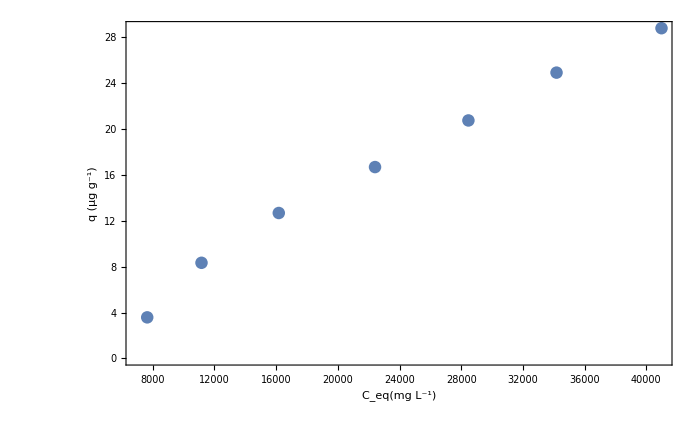

```mathematica
lista2={
qcEAs[prueba1,
1,adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]]],
qcEAs[prueba2,
2,adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]],
qcEAs[prueba3,
3,adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]]],
qcEAs[prueba4,
4,adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]]],
qcEAs[prueba5,
5,adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]]],
qcEAs[prueba6,
6,adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]]],
qcEAs[prueba7,
7,adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]]
}
ListPlot[lista2,LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,PlotRange->Automatic,Axes->False,Frame->True,FrameLabel->{"C_eq(mg L^-1)","q (μg g^-1)"},Joined->False]
```

### Plots Energy, entropy, entropy generation

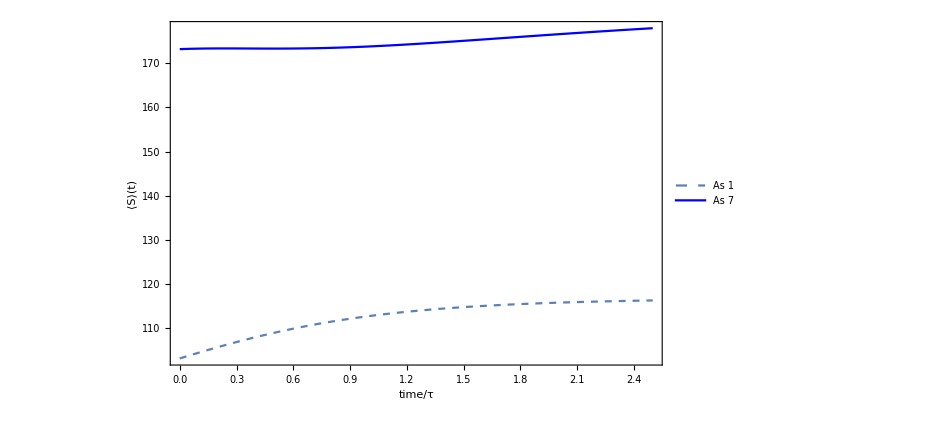

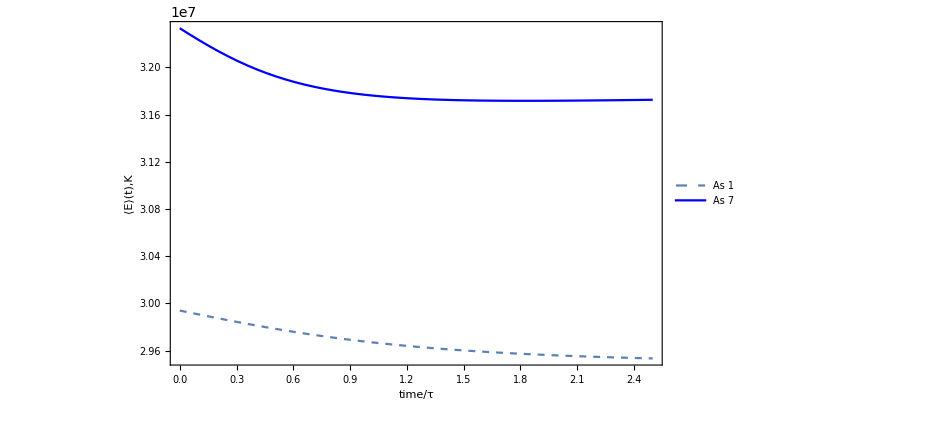

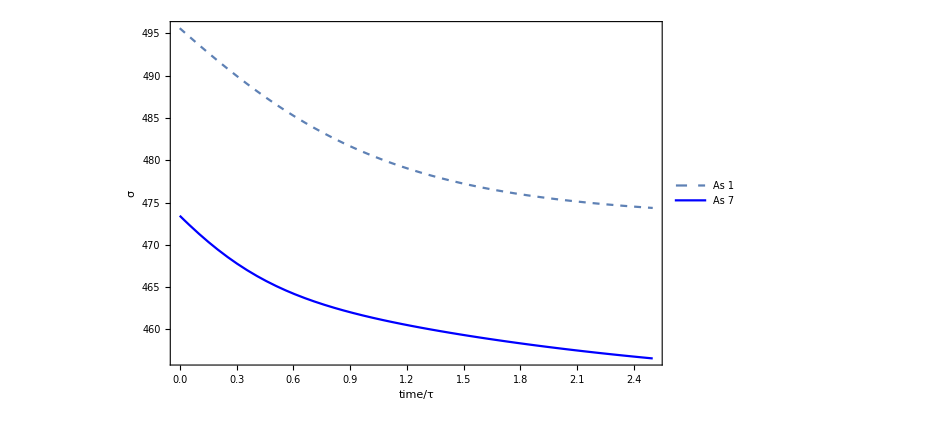

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[1]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[1]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨S⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[2]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[2]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨E⟩(t),K"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
Abs@adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]],
Abs@adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","σ"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

### Plots Entropy generation

{{0.623303,21.252},{1.45123,20.4391},{2.20694,20.9741},{2.90381,23.6687},{3.61129,25.9064},{4.33696,26.6327}}

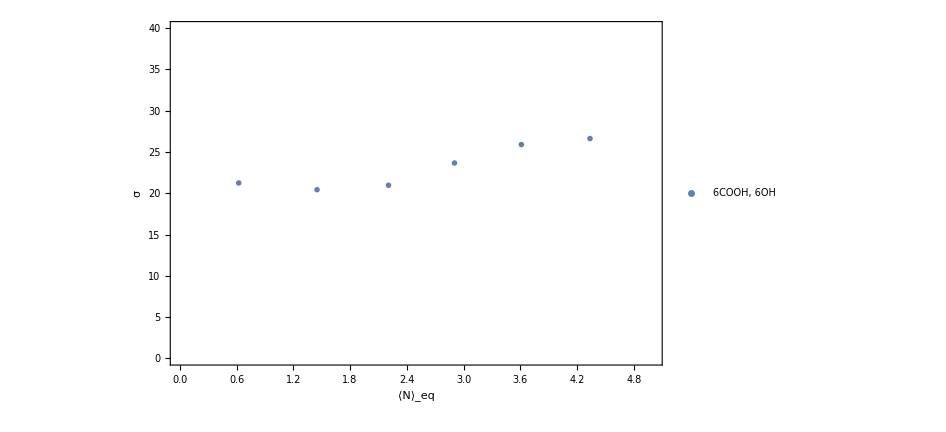

```mathematica
entgen={{adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]-
adsortion[ρttSEAQT1[0],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]},
{adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]-
adsortion[ρttSEAQT2[0],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]},
{adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]-
adsortion[ρttSEAQT3[0],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]},
{adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]-
adsortion[ρttSEAQT4[0],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]},{adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]-
adsortion[ρttSEAQT5[0],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]},
{adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]-
adsortion[ρttSEAQT6[0],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]}}
DS6=ListPlot[entgen,Frame->True,PlotRange->{{0,5},{0,40}},FrameLabel->{"⟨N⟩_eq","σ"},PlotMarkers->{Red,10},LabelStyle->{FontSize->19,FontFamily->"Times"},PlotLegends->Placed[LineLegend[{"6COOH, 6OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.2,0.8}]]
```

## Fig 6c). Kinetics and Isotherms (12 -COOH, 12 -OH)

### 1 As, 1 H^+, 12 -COOH, 12 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

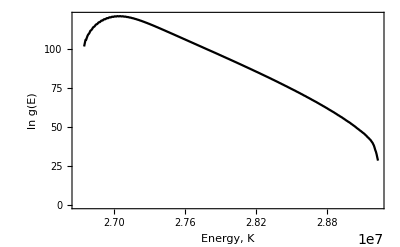

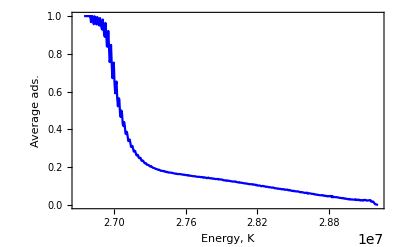

```mathematica
decimals=69;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba1=ToExpression[Import[basePath<>"L20_As1_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba1[[1]]],0];
latticeData=prueba1/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data1=Import[basePath<>"L20_As1_GO12_H1_DOS.txt","Table"];
data1=N[Rationalize[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],10^-decimals],decimals];
(*data1=SetPrecision[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],decimals];*)
ListPlot[data1,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial1=Import[basePath<>"L20_As1_GO12_H1_Nt.txt","Table"];
partial1=N[Rationalize[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],10^-decimals],decimals];
(*partial1=SetPrecision[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],decimals];*)
ListPlot[partial1,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

95.9750245824687557648303381653037964513802502711512554812661722373

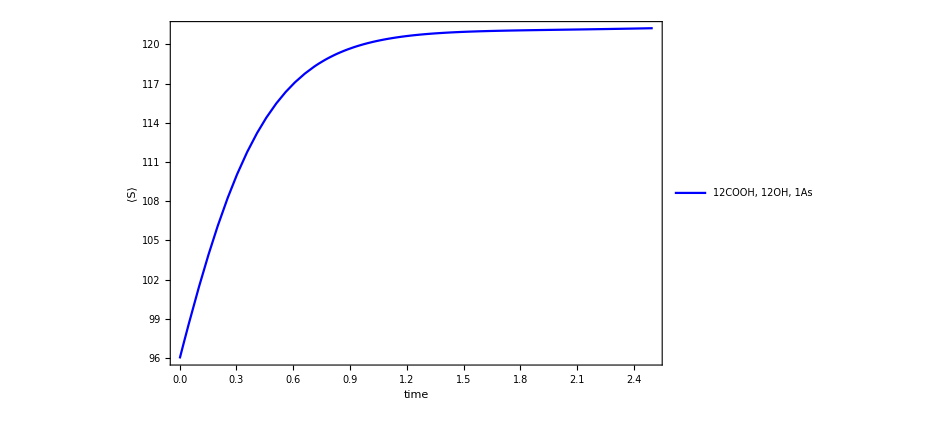

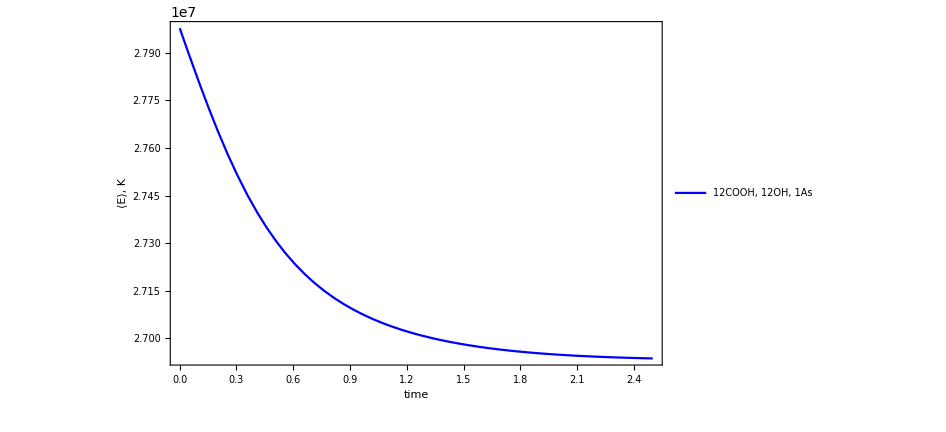

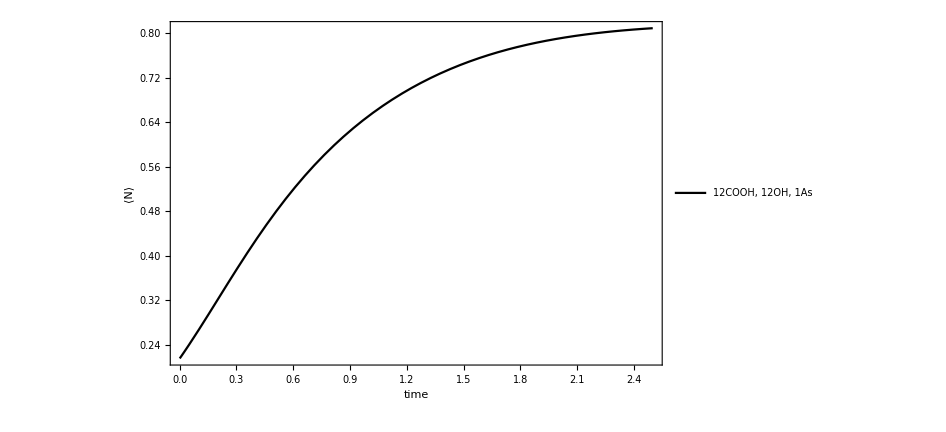

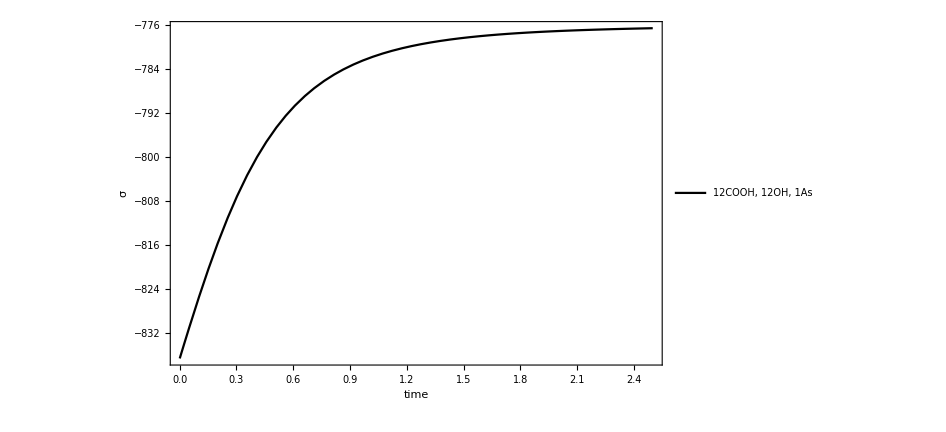

```mathematica
npar1=Length[partial1];
time=2.5;
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar1-1),200,1/200],{i,1,npar1}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
(*p0=SetPrecision[Normalize[data0,Total],decimals];*)
sCurrent=monitor2[p0,Last[Transpose[data1]][[1;;npar1]]]
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],Last[Transpose[partial1]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,
EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data1]][[1;;npar1]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT1=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT1[t1],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩, K",quantity==3,"⟨N⟩",quantity==4,"σ"]},PlotLegends->Placed[LineLegend[{"12COOH, 12OH, 1As"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{Blue,Blue,Black,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S112=plotAdsorption[time,1]
E112=plotAdsorption[time,2] 
plotAdsorption[time,3]
plotAdsorption[time,4]
```

### 2 As, 1 H^+, 12 -COOH, 12 -OH

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

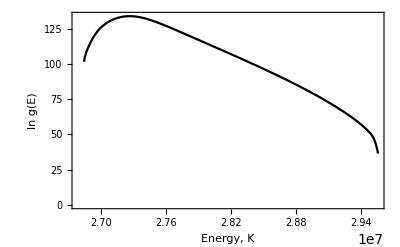

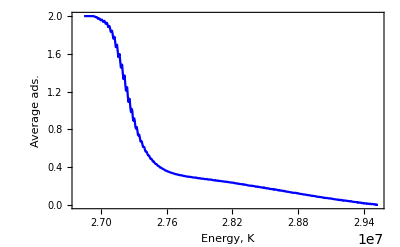

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba2=ToExpression[Import[basePath<>"L20_As2_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba2[[1]]],0];
latticeData=prueba2/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data2=Import[basePath<>"L20_As2_GO12_H1_DOS.txt","Table"];
data2=N[Rationalize[Transpose[{First[Transpose[data2]] correctunits,Last[Transpose[data2]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial2=Import[basePath<>"L20_As2_GO12_H1_Nt.txt","Table"];
partial2=N[Rationalize[Transpose[{First[Transpose[partial2]] correctunits,Last[Transpose[partial2]]}],10^-decimals],decimals];
ListPlot[partial2,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

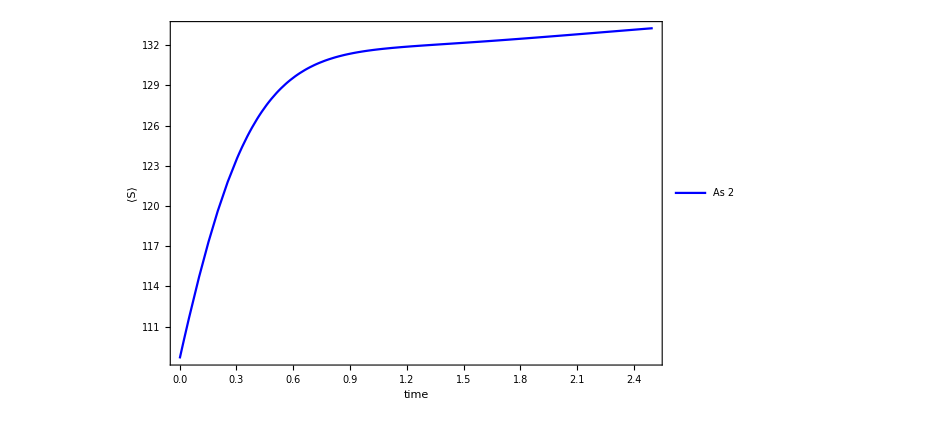

-Graphics-

-Graphics-

```mathematica
npar2=Length[partial2];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar2-1),200,1/200],{i,1,npar2}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],Last[Transpose[partial2]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data2]][[1;;npar2]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT2=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT2[t1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

### 3 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba3=ToExpression[Import[basePath<>"L20_As3_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba3[[1]]],0];
latticeData=prueba3/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data3=Import[basePath<>"L20_As3_GO12_H1_DOS.txt","Table"];
data3=N[Rationalize[Transpose[{First[Transpose[data3]] correctunits,Last[Transpose[data3]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial3=Import[basePath<>"L20_As3_GO12_H1_Nt.txt","Table"];
partial3=N[Rationalize[Transpose[{First[Transpose[partial3]] correctunits,Last[Transpose[partial3]]}],10^-decimals],decimals];
ListPlot[partial3,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar3=Length[partial3];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar3-2),1/20,1/200],{i,1,npar3}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],Last[Transpose[partial3]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data3]][[1;;npar3]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT3=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT3[t1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 3"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 4 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba4=ToExpression[Import[basePath<>"L20_As4_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba4[[1]]],0];
latticeData=prueba4/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data4=Import[basePath<>"L20_As4_GO12_H1_DOS.txt","Table"];
data4=N[Rationalize[Transpose[{First[Transpose[data4]] correctunits,Last[Transpose[data4]]}],10^-decimals],decimals];
ListPlot[data4,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial4=Import[basePath<>"L20_As4_GO12_H1_Nt.txt","Table"];
partial4=N[Rationalize[Transpose[{First[Transpose[partial4]] correctunits,Last[Transpose[partial4]]}],10^-decimals],decimals];
ListPlot[partial4,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar4=Length[partial4];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar4-2),1/20,1/200],{i,1,npar4}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],Last[Transpose[partial4]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data4]][[1;;npar4]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT4=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT4[t1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 4"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

NDSolve::nderr: Error test failure at t == 0.003277271027306792698340908995514919513387434114748573001046089421797; unable to continue.

-Graphics-

-Graphics-

-Graphics-

### 5 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba5=ToExpression[Import[basePath<>"L20_As5_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba5[[1]]],0];
latticeData=prueba5/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data5=Import[basePath<>"L20_As5_GO12_H1_DOS.txt","Table"];
data5=N[Rationalize[Transpose[{First[Transpose[data5]] correctunits,Last[Transpose[data5]]}],10^-decimals],decimals];
ListPlot[data5,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial5=Import[basePath<>"L20_As5_GO12_H1_Nt.txt","Table"];
partial5=N[Rationalize[Transpose[{First[Transpose[partial5]] correctunits,Last[Transpose[partial5]]}],10^-decimals],decimals];
ListPlot[partial5,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar5=Length[partial5];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
data0=Table[If[i<=(npar5-2),1/20,1/200],{i,1,npar5}];
βchoice=1/30000;
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],Last[Transpose[partial5]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data5]][[1;;npar5]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT5=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT5[t1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 5"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 6 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba6=ToExpression[Import[basePath<>"L20_As6_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba6[[1]]],0];
latticeData=prueba6/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data6=Import[basePath<>"L20_As6_GO12_H1_DOS.txt","Table"];
data6=N[Rationalize[Transpose[{First[Transpose[data6]] correctunits,Last[Transpose[data6]]}],10^-decimals],decimals];
ListPlot[data6,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial6=Import[basePath<>"L20_As6_GO12_H1_Nt.txt","Table"];
partial6=N[Rationalize[Transpose[{First[Transpose[partial6]] correctunits,Last[Transpose[partial6]]}],10^-decimals],decimals];
ListPlot[partial6,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar6=Length[partial6];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar6-2),1/20,1/200],{i,1,npar6}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],Last[Transpose[partial6]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data6]][[1;;npar6]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT6=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT6[t1],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 6"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2];
plotAdsorption[time,3];
```

-Graphics-

### 7 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_H1_GO12/"]
prueba7=ToExpression[Import[basePath<>"L20_As7_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba7[[1]]],0];
latticeData=prueba7/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data7=Import[basePath<>"L20_As7_GO12_H1_DOS.txt","Table"];
data7=N[Rationalize[Transpose[{First[Transpose[data7]] correctunits,Last[Transpose[data7]]}],10^-decimals],decimals];
ListPlot[data7,Joined->True,FrameLabel->{"Energy, J","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial7=Import[basePath<>"L20_As7_GO12_H1_Nt.txt","Table"];
partial7=N[Rationalize[Transpose[{First[Transpose[partial7]] correctunits,Last[Transpose[partial7]]}],10^-decimals],decimals];
ListPlot[partial7,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_H1_GO12/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar7=Length[partial7];
values={τ->22};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar7-2),1/20,1/200],{i,1,npar7}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],Last[Transpose[partial7]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data7]][[1;;npar7]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT7=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT7[t1],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩, K",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"12COOH, 12OH, 7As"},LabelStyle->{FontFamily->"Times",FontSize->16}],{0.8,0.7}],PlotStyle->{{Blue,Dashed},{Blue,Dashed},Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
S712=plotAdsorption[time,1]
E712=plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### Plots Kinetics

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT3[t],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT4[t],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT5[t],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]
}
,{t,0,time},PlotRange->{0,8},FrameLabel->{"time/τ","⟨n⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 2","As 3","As 4","As 5","As 6","As 7"},LabelStyle->{FontFamily->"Times",FontSize->22},LegendLayout->{"Column",2}],{0.2,0.8}],LabelStyle->{FontSize->30,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

-Graphics-

### Plots Isotherms

```mathematica
lista1={
qcEAs[prueba1,
1,adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]]],
qcEAs[prueba2,
2,adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]],
qcEAs[prueba3,
3,adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]]],
qcEAs[prueba4,
4,adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]]],
qcEAs[prueba5,
5,adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]]],
qcEAs[prueba6,
6,adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]]],
qcEAs[prueba7,
7,adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]]]
}
ListPlot[lista1,LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,PlotRange->Automatic,Axes->False,Frame->True,FrameLabel->{"C_eq(mg L^-1)","q (μg g^-1)"},Joined->False]
```

InterpolatingFunction::dmval: Input value {2.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{4.12411×10^7,-5659.46},{2.48518×10^8,-34024.1},{2.49591×10^10,-3.40851×10^6},{1.24087×10^11,-1.69003×10^7},{3.65564×10^11,-4.96545×10^7},{8.4992×10^11,-1.15132×10^8},{1.8875×10^12,-2.54992×10^8}}

-Graphics-

### Plots Entropy, energy, entropy generation

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[1]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[1]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨S⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[2]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[2]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨E⟩(t),K"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]],
adsortion[ρttSEAQT7[t],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","σ"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"As 1","As 7"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.8,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

-Graphics-

-Graphics-

-Graphics-

### Plots entropy generation

```mathematica
entgen={{adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]-
adsortion[ρttSEAQT1[0],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]},
{adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]-
adsortion[ρttSEAQT2[0],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]},
{adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]-
adsortion[ρttSEAQT3[0],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]},
{adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]-
adsortion[ρttSEAQT4[0],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]},{adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]-
adsortion[ρttSEAQT5[0],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]},
{adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]-
adsortion[ρttSEAQT6[0],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]},
{adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[3]],
adsortion[ρttSEAQT7[time],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]-
adsortion[ρttSEAQT7[0],First[Transpose[data7]][[1;;npar7]],Last[Transpose[data7]][[1;;npar7]],partial7][[4]]}}
DS12=ListPlot[entgen,Frame->True,PlotRange->{{0,5},{0,40}},FrameLabel->{"⟨N⟩_eq","σ"},PlotMarkers->{Blue,10},LabelStyle->{FontSize->19,FontFamily->"Times"},PlotLegends->Placed[LineLegend[{"12COOH, 12OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.2,0.6}]]
```

InterpolatingFunction::dmval: Input value {2.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{-1968.88,138147.},{-11836.7,342480.},{-1.18579×10^6,1.11056×10^8},{-5.87948×10^6,3.26567×10^8},{-1.72744×10^7,8.50614×10^8},{-4.00537×10^7,2.55835×10^9},{-8.87099×10^7,6.64536×10^9}}

-Graphics-

## Fig 7. Two axis plots

```mathematica
(*Interpolate the datasets*)
R1={{7283,77.10},{3528,67.18},{1737,62.65}};
q11={{7283,2.24},{3528,3.86+0.1},{1737,7.20}};
f1=Interpolation[R1,InterpolationOrder->1];
f2=Interpolation[q11,InterpolationOrder->1];
(*Define the TwoAxisPlot function*)
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#1[x],{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];
{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];
```

```mathematica
rangeR1=Through[{Min,Max}[R1[[All,2]]]];
rangeQ11=Through[{Min,Max}[q11[[All,2]]]];
rescaledQ11=q11;
rescaledQ11[[All,2]]=Rescale[q11[[All,2]],rangeQ11,rangeR1];
pointsPlotR1=ListPlot[R1,PlotStyle->Red,PlotMarkers->{"●",20}];
adjustedPointsPlotQ11=ListPlot[rescaledQ11,PlotStyle->Blue,PlotMarkers->{"▲",20}];

finalPlot=Show[TwoAxisPlot[{f1,f2},{x,Min[R1[[All,1]]],Max[R1[[All,1]]]}],pointsPlotR1,adjustedPointsPlotQ11,PlotRange->All,ImageSize->{700},FrameLabel->{"Adsorbent Concentration, mg L^-1","% Removal"," ","q, mg g^-1"},BaseStyle->{FontSize->20,FontFamily->"Times"}];
finalPlot
```

-Graphics-

## Fig 8 and 9 Total Entropy generation and local entropies

### Total entropy generation

```mathematica
DS12={{0.7792701787357657,28.578000536327238},{1.4914485879574797,28.901576385255396},{2.1478576400276,30.019320953987517},{2.792626228619671,32.202381131252466},{3.4388556086175757,33.29861504427302},{4.09143657184201,34.51533769422991},{4.790592900768429,35.33597677059976}};
DS6={{0.6233032793475747,21.2519951757954},{1.451226796861247,20.439130654059966},{2.2069391516760555,20.974104726165706},{2.9038100442659625,23.668677169468253},{3.611285803174398,25.906400766262152},{4.336960160379185,26.632731887009413}};
DS3={{0.6265278841864867,6.9448688659736035},{1.3714034403123587,10.72693417918822},{2.0940377703806647,11.133929918485023},{2.9153215550830116,12.307793225786668},{3.6813212504681814,15.49695129894019},{4.4834164641499665,18.871281776339742},{5.198564360892891,23.876765718443494}};
ListPlot[{DS12,DS6,DS3},ImageSize->700,
Frame->True,
PlotRange->{{0,5},{0,40}},
FrameLabel->{"⟨N⟩_eq","σ"},
PlotMarkers->{{"×",22},{"▲",20},{"●",16}},LabelStyle->{FontSize->19,FontFamily->"Times"},
PlotStyle->{Black,Blue,Red},
PlotLegends->Placed[LineLegend[{"12COOH, 12OH","6COOH, 6OH","3COOH, 3OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",1}],{0.12,0.87}]]
```

-Graphics-

```mathematica
{{0.6718102952225705,27.433861687645845},{1.4946169776648601,26.713818564497842},{2.2135341993856494,28.09408786744234},{2.8694499415184116,31.774213088809006},{3.485847821790726,35.50964680060247},{4.210426385520695,38.14805037943938}};
```

### Local plots

```mathematica
Show[S13,S73,S16,S76,S112,S712]
```

```mathematica
Show[E13,E73,E16,E76,E112,E712]
```

## Fig 10 and 11. Kinetics (As2 Change GO)

### 2 As, 1 H^+, 3 -COOH, 3 -OH

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba1=ToExpression[Import[basePath<>"L20_As2_GO3_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba1[[1]]],0];
latticeData=prueba1/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data1=Import[basePath<>"L20_As2_GO3_H1_DOS.txt","Table"];
data1=N[Rationalize[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],10^-decimals],decimals];
ListPlot[data1,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial1=Import[basePath<>"L20_As2_GO3_H1_Nt.txt","Table"];
partial1=N[Rationalize[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],10^-decimals],decimals];
ListPlot[partial1,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar1=Length[partial1];
time=0.85;
values={τ->8};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar1-1),200,1/200],{i,1,npar1}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
sCurrent=monitor2[p0,Last[Transpose[data1]][[1;;npar1]]]
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],Last[Transpose[partial1]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data1]][[1;;npar1]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT1=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT1[t1],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"3OH, 3COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

132.2479237169838286370984027610251849223381974335

-Graphics-

-Graphics-

-Graphics-

### 2 As, 1 H^+, 6 -COOH, 6 -OH

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba2=ToExpression[Import[basePath<>"L20_As2_GO6_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba2[[1]]],0];
latticeData=prueba2/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data2=Import[basePath<>"L20_As2_GO6_H1_DOS.txt","Table"];
data2=N[Rationalize[Transpose[{First[Transpose[data2]] correctunits,Last[Transpose[data2]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial2=Import[basePath<>"L20_As2_GO6_H1_Nt.txt","Table"];
partial2=N[Rationalize[Transpose[{First[Transpose[partial2]] correctunits,Last[Transpose[partial2]]}],10^-decimals],decimals];
ListPlot[partial2,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar2=Length[partial2];
time=0.85;
values={τ->8};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar2-1),200,1/200],{i,1,npar2}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],Last[Transpose[partial2]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data2]][[1;;npar2]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT2=p/. First[sol1[[1]]]; 
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT2[t1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"6OH,6COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Blue,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 2 As, 1 H^+, 9 -COOH, 9 -OH

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba3=ToExpression[Import[basePath<>"L20_As2_GO9_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba3[[1]]],0];
latticeData=prueba3/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data3=Import[basePath<>"L20_As2_GO9_H1_DOS.txt","Table"];
data3=N[Rationalize[Transpose[{First[Transpose[data3]] correctunits,Last[Transpose[data3]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial3=Import[basePath<>"L20_As2_GO9_H1_Nt.txt","Table"];
partial3=N[Rationalize[Transpose[{First[Transpose[partial3]] correctunits,Last[Transpose[partial3]]}],10^-decimals],decimals];
ListPlot[partial3,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar3=Length[partial3];
time=0.85;
values={τ->8};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar3-2),1/20,1/200],{i,1,npar3}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],Last[Transpose[partial3]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data3]][[1;;npar3]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT3=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT3[t1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"9OH,9COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 2 As, 1 H^+, 12 -COOH, 12 -OH

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba4=ToExpression[Import[basePath<>"L20_As2_GO12_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba4[[1]]],0];
latticeData=prueba4/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data4=Import[basePath<>"L20_As2_GO12_H1_DOS.txt","Table"];
data4=N[Rationalize[Transpose[{First[Transpose[data4]] correctunits,Last[Transpose[data4]]}],10^-decimals],decimals];
ListPlot[data4,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial4=Import[basePath<>"L20_As2_GO12_H1_Nt.txt","Table"];
partial4=N[Rationalize[Transpose[{First[Transpose[partial4]] correctunits,Last[Transpose[partial4]]}],10^-decimals],decimals];
ListPlot[partial4,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar4=Length[partial4];
time=0.85;
values={τ->8};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar4-2),1/20,1/200],{i,1,npar4}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],Last[Transpose[partial4]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data4]][[1;;npar4]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT4=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT4[t1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"12OH,12COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 2 As, 1 H^+, 15 -COOH, 15 -OH

```mathematica
decimals=50;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba5=ToExpression[Import[basePath<>"L20_As2_GO15_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba5[[1]]],0];
latticeData=prueba5/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data5=Import[basePath<>"L20_As2_GO15_H1_DOS.txt","Table"];
data5=N[Rationalize[Transpose[{First[Transpose[data5]] correctunits,Last[Transpose[data5]]}],10^-decimals],decimals];
ListPlot[data5,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial5=Import[basePath<>"L20_As2_GO15_H1_Nt.txt","Table"];
partial5=N[Rationalize[Transpose[{First[Transpose[partial5]] correctunits,Last[Transpose[partial5]]}],10^-decimals],decimals];
ListPlot[partial5,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar5=Length[partial5];
time=0.85;
values={τ->8};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar5-2),1/20,1/200],{i,1,npar5}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],Last[Transpose[partial5]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data5]][[1;;npar5]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT5=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT5[t1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"15OH,15COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 2 As, 1 H^+, 18 -COOH, 18 -OH

```mathematica
decimals=60;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/L20_As2_H1_GO/"]
prueba6=ToExpression[Import[basePath<>"L20_As2_GO18_H1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba6[[1]]],0];
latticeData=prueba6/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data6=Import[basePath<>"L20_As2_GO18_H1_DOS.txt","Table"];
data6=N[Rationalize[Transpose[{First[Transpose[data6]] correctunits,Last[Transpose[data6]]}],10^-decimals],decimals];
ListPlot[data6,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial6=Import[basePath<>"L20_As2_GO18_H1_Nt.txt","Table"];
partial6=N[Rationalize[Transpose[{First[Transpose[partial6]] correctunits,Last[Transpose[partial6]]}],10^-decimals],decimals];
ListPlot[partial6,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/L20_As2_H1_GO/

Lattice size = {20,20}

-Graphics-

-Graphics-

```mathematica
npar6=Length[partial6];
time=0.85;
values={τ->92/10};  (*Assuming τ is a parameter in disspn*)
βchoice=1/30000;
data0=Table[If[i<=(npar6-2),1/20,1/200],{i,1,npar6}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],Last[Transpose[partial6]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data6]][[1;;npar6]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT6=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT6[t1],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"18OH,18COOH"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### Plots

```mathematica
Plot[
{
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT3[t],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT4[t],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT5[t],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]]
}
,{t,0,time},PlotRange->All,FrameLabel->{"time","⟨N⟩"},
PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},
PlotLegends->Placed[LineLegend[{"6OH, 6COOH","9OH, 9COOH","12OH, 12COOH","15OH, 15COOH","18OH, 18COOH","21OH, 21COOH"},LabelStyle->{FontFamily->"Times",FontSize->16}],{.6,0.3}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True,PlotRange->{0,7}]
```

-Graphics-

```mathematica
lista={
qcEAs[prueba1,
2,adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]]],
qcEAs[prueba2,
2,adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]],
qcEAs[prueba3,
2,adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]]],
qcEAs[prueba4,
2,adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]]],
qcEAs[prueba5,
2,adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]]],
qcEAs[prueba6,
2,adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]]]
}
ListPlot[lista,LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,PlotRange->Automatic,Axes->False,Frame->True,FrameLabel->{"C_eq(mg L^-1)","q (μg g^-1)"},Joined->False]
```

{{12729.8,15.6867},{10386.5,8.56182},{9128.88,5.97169},{8479.17,4.58784},{8331.54,3.70112},{8321.21,3.09742}}

-Graphics-

```mathematica
Plot[
{
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[1]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[1]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨S⟩(t)"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"6OH, 6COOH, 2As","18OH, 18COOH, 2As"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.6,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]

Plot[
{
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[2]],
adsortion[ρttSEAQT6[t],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[1]]
}
,{t,0,time},PlotRange->Automatic,FrameLabel->{"time/τ","⟨E⟩(t),K"},PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},PlotLegends->Placed[LineLegend[{"6OH, 6COOH, 2As","18OH, 18COOH, 2As"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.6,0.8}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

-Graphics-

-Graphics-

```mathematica
entgen={{adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT1[time],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]-
adsortion[ρttSEAQT1[0],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[4]]},
{adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]],
adsortion[ρttSEAQT2[time],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]-
adsortion[ρttSEAQT2[0],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[4]]},
{adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT3[time],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]-
adsortion[ρttSEAQT3[0],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[4]]},
{adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT4[time],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]-
adsortion[ρttSEAQT4[0],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[4]]},{adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT5[time],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]-
adsortion[ρttSEAQT5[0],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[4]]},
{adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[3]],
adsortion[ρttSEAQT6[time],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]-
adsortion[ρttSEAQT6[0],First[Transpose[data6]][[1;;npar6]],Last[Transpose[data6]][[1;;npar6]],partial6][[4]]}}
ListPlot[entgen,Frame->True,PlotRange->Automatic,FrameLabel->{"⟨N⟩_eq","σ"},PlotMarkers->{Orange,13},LabelStyle->{FontSize->19,FontFamily->"Times"},PlotLegends->Placed[LineLegend[{"2As"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.2,0.6}]]
```

{{1.36432,10.5593},{1.4893,26.553},{1.55813,43.2123},{1.59608,56.9382},{1.60949,69.099},{1.61635,79.821}}

-Graphics-

## Fig 12. Regression Isotherms

```mathematica
Iso1={{4621.161766039986,2.2399726503307806},{10675.489427058803,4.287093408115664},{17936.222254257773,6.173907974088146},{25481.76989193524,8.027262617508086},{33037.19076898481,9.884816231819245},{40498.78493896222,11.760627150338818},{48322.029080651744,13.593059213773921}};
Iso2={{6657.319659086198,3.8621693183500208},{10278.309259439338,8.592401567632788},{16036.529215651988,12.725383833472568},{23112.811900550485,16.496176976570606},{31036.155904132505,20.039785935845366},{36777.8514471731,24.20531468327977},{48740.90548462462,26.643506546139978}};
Iso3={{7459.914966377061,7.203690650778549},{12588.007832108005,15.768118851168532},{18188.933994665113,24.07682194138122},{23195.149243649485,32.74168420590361},{29516.71470757569,40.67182774370137},{36784.06887489225,48.08306218122864},{47001.77599993083,53.84333988843862}};
modelF=C0 x^(1/n);
modelL=qL b x/(1+b x);
modelH=KH*x;

(*Ajuste para Iso1*)
fitF1=NonlinearModelFit[Iso1,modelF,{C0,n},x];
fitL1=NonlinearModelFit[Iso1,modelL,{qL,b},x,Method->{NMinimize,Method->{"NelderMead"}}];
fitH1=FindFit[Iso1,modelH,KH,x];

(*Ajuste para Iso2*)
fitF2=NonlinearModelFit[Iso2,modelF,{C0,n},x];
fitL2=NonlinearModelFit[Iso2,modelL,{qL,b},x,Method->{NMinimize,Method->{"NelderMead"}}];
fitH2=FindFit[Iso2,modelH,KH,x];

(*Ajuste para Iso3*)
fitF3=NonlinearModelFit[Iso3,modelF,{C0,n},x];
fitL3=NonlinearModelFit[Iso3,modelL,{qL,b},x,Method->{NMinimize,Method->{"NelderMead"}}];
fitH3=FindFit[Iso3,modelH,KH,x];

Show[Plot[{modelF/. fitF1["BestFitParameters"],modelL/. fitL1["BestFitParameters"],modelH/. fitH1},{x,0,60000},PlotStyle->{Blue,Red,Orange},PlotLegends->{"Freundlich","Langmuir","Henry"}],ListPlot[Iso1,PlotStyle->Directive[PointSize[Medium],Black]]];

Show[Plot[{modelF/. fitF2["BestFitParameters"],modelL/. fitL2["BestFitParameters"],modelH/. fitH1},{x,0,60000},PlotStyle->{Blue,Red,Orange},PlotLegends->{"Freundlich","Langmuir","Henry"}],ListPlot[Iso2,PlotStyle->Directive[PointSize[Medium],Black]]];

Show[Plot[{modelF/. fitF3["BestFitParameters"],modelL/. fitL3["BestFitParameters"],modelH/. fitH1},{x,0,60000},PlotStyle->{Blue,Red,Orange},PlotLegends->{"Freundlich","Langmuir","Henry"}],ListPlot[Iso3,PlotStyle->Directive[PointSize[Medium],Black]]];

Show[
Plot[{
modelF/. fitF1["BestFitParameters"],modelL/. fitL1["BestFitParameters"],
modelF/. fitF2["BestFitParameters"],modelL/. fitL2["BestFitParameters"],
modelF/. fitF3["BestFitParameters"],modelL/. fitL3["BestFitParameters"]},{x,0,60000},PlotStyle->{Directive[Blue],Directive[Dashed,Red],Directive[Blue],Directive[Dashed,Red],Directive[Blue],Directive[Dashed,Red]},PlotRange->Automatic,FrameLabel->{"C_eq","q"},
PlotLegends->Placed[LineLegend[{"Langmuir","Freundlich"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.245,0.78}],
PlotStyle->{Dashed,Blue,Red,Blend[{Yellow,Pink,Green}],Purple,Blend[{Yellow,Red,Green}],Orange,Brown,Black,Orange},LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True
],
ListPlot[{Iso1,Iso2,Iso3},PlotMarkers->{{"×",20},{"▲",20},{"●",17}},PlotStyle->{Blue,Red,Black},
PlotLegends->Placed[LineLegend[{"12COOH, 12OH","6COOH, 6OH","3COOH, 3OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",2}],{0.25,0.65}]]
]
Print["__________________________________________________________________________________________________"];
Print["12 COOH, for Freundlich R^2 = ",fitF1["RSquared"]," with coefficients ",fitF1["BestFitParameters"]]
Print["12 COOH, for Langmuir R^2 = ",fitL1["RSquared"]," with coefficients ",fitL1["BestFitParameters"]]
Print["__________________________________________________________________________________________________"];
Print["6 COOH, for Freubdlich R^2 = ",fitF2["RSquared"]," with coefficients ",fitF2["BestFitParameters"]]
Print["12 COOH, for Langmuir R^2 = ",fitL2["RSquared"]," with coefficients ",fitL2["BestFitParameters"]]
Print["__________________________________________________________________________________________________"];
Print["3 COOH, for Freundlich R^2 = ",fitF3["RSquared"]," with coefficients ",fitF3["BestFitParameters"]]
Print["12 COOH, for Langmuir R^2 = ",fitL3["RSquared"]," with coefficients ",fitL3["BestFitParameters"]]
Print["__________________________________________________________________________________________________"];
```

-Graphics-

__________________________________________________________________________________________________

12 COOH, for Freundlich R^2 = 0.99985 with coefficients {C0→0.00292542,n→1.27863}

12 COOH, for Langmuir R^2 = 0.951277 with coefficients {qL→12.0274,b→0.0000921595}

__________________________________________________________________________________________________

6 COOH, for Freubdlich R^2 = 0.995234 with coefficients {C0→0.00734699,n→1.30841}

12 COOH, for Langmuir R^2 = 0.997316 with coefficients {qL→69.8389,b→0.0000132689}

__________________________________________________________________________________________________

3 COOH, for Freundlich R^2 = 0.994549 with coefficients {C0→0.00366037,n→1.11384}

12 COOH, for Langmuir R^2 = 0.995865 with coefficients {qL→245.353,b→6.27608×10^-6}

__________________________________________________________________________________________________

```mathematica
Iso1={{4621.161766039986,2.2399726503307806},{10675.489427058803,4.287093408115664},{17936.222254257773,6.173907974088146},{25481.76989193524,8.027262617508086},{33037.19076898481,9.884816231819245},{40498.78493896222,11.760627150338818},{48322.029080651744,13.593059213773921}};
Iso2={{6657.319659086198,3.8621693183500208},{10278.309259439338,8.592401567632788},{16036.529215651988,12.725383833472568},{23112.811900550485,16.496176976570606},{31036.155904132505,20.039785935845366},{36777.8514471731,24.20531468327977},{48740.90548462462,26.643506546139978}};
Iso3={{7459.914966377061,7.203690650778549},{12588.007832108005,15.768118851168532},{18188.933994665113,24.07682194138122},{23195.149243649485,32.74168420590361},{29516.71470757569,40.67182774370137},{36784.06887489225,48.08306218122864},{47001.77599993083,53.84333988843862}};
Rem1={{20180.4,77.10},{40465.1,73.61},{60854.9 ,70.52},{81350.6 ,68.67},{105811, 68.77},{127317 ,68.19},{150940 ,67.98}};
Rem2={{20285, 67.18},{40675.3, 74.73},{61171.9, 73.78},{81775.5,71.73},{102487.0,70.69},{123307 ,70.17},{144237,69.499}};
Rem3={{19974.5 ,62.65},{40051.2 ,68.57},{60230.8 ,69.80},{80514.1,71.19},{100901 ,70.74},{121395, 69.69},{141995, 66.89}};
ListPlot[{Rem1,Rem2,Rem3},ImageSize->700,
Frame->True,
PlotRange->Automatic,
FrameLabel->{"C_eq(mg L^-1)","Removal (%)"},
PlotMarkers->{{"×",22},{"▲",20},{"●",16}},LabelStyle->{FontSize->19,FontFamily->"Times"},
PlotStyle->{Black,Blue,Red},
PlotLegends->Placed[LineLegend[{"12COOH, 12OH","6COOH, 6OH","3COOH, 3OH"},LabelStyle->{FontFamily->"Times",FontSize->16},LegendLayout->{"Column",1}],{0.12,0.87}]]
```

-Graphics-

## Fig 13. Kinetics (pH variation)

### 1 As (1.22g/L), 1 H^+(pH 2.06 ), 1 -COOH, 1 - (35.49)

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/pH_changing/"]
prueba1=ToExpression[Import[basePath<>"L80_As1_H1_GO1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba1[[1]]],0];
latticeData=prueba1/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data1=Import[basePath<>"L80_As1_H1_GO1_DOS.txt","Table"];
data1=N[Rationalize[Transpose[{First[Transpose[data1]] correctunits,Last[Transpose[data1]]}],10^-decimals],decimals];
ListPlot[data1,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial1=Import[basePath<>"L80_As1_H1_GO1_Nt.txt","Table"];
partial1=N[Rationalize[Transpose[{First[Transpose[partial1]] correctunits,Last[Transpose[partial1]]}],10^-decimals],decimals];
ListPlot[partial1,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/pH_changing/

Lattice size = {80,80}

-Graphics-

-Graphics-

```mathematica
npar1=Length[partial1];
time=1.5;
values={τ->17};  (*Assuming τ is a parameter in disspn*)
βchoice=1/400000;
data0=Table[If[i<=(npar1-1),200,1/200],{i,1,npar1}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
sCurrent=monitor2[p0,Last[Transpose[data1]][[1;;npar1]]]
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],Last[Transpose[partial1]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data1]][[1;;npar1]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT1=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT1[t1],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 1"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

114.5041914858158647312693051062434178393985774791888546727743937500063890519021

-Graphics-

-Graphics-

-Graphics-

### 1 As (1.26 g/L), 30 H^+(pH 0.6), 1 -COOH, 1 -OH (35.65g/L)

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/pH_changing/"]
prueba2=ToExpression[Import[basePath<>"L80_As1_H30_GO1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba2[[1]]],0];
latticeData=prueba2/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data2=Import[basePath<>"L80_As1_H30_GO1_DOS.txt","Table"];
data2=N[Rationalize[Transpose[{First[Transpose[data2]] correctunits,Last[Transpose[data2]]}],10^-decimals],decimals];
ListPlot[data2,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial2=Import[basePath<>"L80_As1_H30_GO1_Nt.txt","Table"];
partial2=N[Rationalize[Transpose[{First[Transpose[partial2]][[1;;Length[data2]]]correctunits,Last[Transpose[partial2]][[1;;Length[data2]]]}],10^-decimals],decimals];
ListPlot[partial2,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/pH_changing/

Lattice size = {80,80}

-Graphics-

-Graphics-

```mathematica
npar2=Length[partial2];
time=1.5;
values={τ->17};  (*Assuming τ is a parameter in disspn*)
βchoice=1/400000;
data0=Table[If[i<=(npar2-1),200,1/200],{i,1,npar2}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],Last[Transpose[partial2]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data2]][[1;;npar2]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT2=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT2[t1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 1 As (1.23 g/L), 5H^+(pH 1.36), 1 -COOH, 1 -OH (35.51g/L)

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/pH_changing/"]
prueba3=ToExpression[Import[basePath<>"L80_As1_H5_GO1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba3[[1]]],0];
latticeData=prueba3/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data3=Import[basePath<>"L80_As1_H5_GO1_DOS.txt","Table"];
data3=N[Rationalize[Transpose[{First[Transpose[data3]] correctunits,Last[Transpose[data3]]}],10^-decimals],decimals];
ListPlot[data3,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial3=Import[basePath<>"L80_As1_H5_GO1_Nt.txt","Table"];
partial3=N[Rationalize[Transpose[{First[Transpose[partial3]]correctunits,Last[Transpose[partial3]]}],10^-decimals],decimals];
ListPlot[partial3,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/pH_changing/

Lattice size = {80,80}

-Graphics-

-Graphics-

```mathematica
npar3=Length[partial3];
time=1.5;
values={τ->17};  (*Assuming τ is a parameter in disspn*)
βchoice=1/400000;
data0=Table[If[i<=(npar3-1),200,1/200],{i,1,npar3}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],Last[Transpose[partial3]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data3]][[1;;npar3]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT3=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT3[t1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 1 As (1.23 g/L), 17H^+(pH 0.83), 1 -COOH, 1 -OH (35.58g/L)

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/pH_changing/"]
prueba4=ToExpression[Import[basePath<>"L80_As1_H17_GO1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba4[[1]]],0];
latticeData=prueba4/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data4=Import[basePath<>"L80_As1_H17_GO1_DOS.txt","Table"];
data4=N[Rationalize[Transpose[{First[Transpose[data4]] correctunits,Last[Transpose[data4]]}],10^-decimals],decimals];
ListPlot[data4,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial4=Import[basePath<>"L80_As1_H17_GO1_Nt.txt","Table"];
partial4=N[Rationalize[Transpose[{First[Transpose[partial4]]correctunits,Last[Transpose[partial4]]}],10^-decimals],decimals];
ListPlot[partial4,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/pH_changing/

Lattice size = {80,80}

-Graphics-

-Graphics-

```mathematica
npar4=Length[partial4];
time=1.5;
values={τ->17};  (*Assuming τ is a parameter in disspn*)
βchoice=1/400000;
data0=Table[If[i<=(npar4-1),200,1/200],{i,1,npar4}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],Last[Transpose[partial4]]],p[0]==p0},p,{t,0,time},Method->"Automatic",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data4]][[1;;npar4]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT4=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT4[t1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### 1 As (1.23 g/L), 2H^+(pH 1.76), 1 -COOH, 1 -OH (35.49g/L)

```mathematica
decimals=80;
nAvogadro=6.02214199 10^23;
kBolt=1.380649 10^-23;
correctunits=100 0.23 4184 /(2 nAvogadro kBolt);
colorRules={0->Red,1->Gray,2->Black,3->Orange,4->Blue};
inDirectory=SetDirectory[NotebookDirectory[]];
basePath=StringJoin[inDirectory,"/WL/pH_changing/"]
prueba5=ToExpression[Import[basePath<>"L80_As1_H2_GO1_Vid.txt","Text"]];
numberAs=Count[Flatten[prueba5[[1]]],0];
latticeData=prueba5/. colorRules;
Animate[ArrayPlot[latticeData[[i]],Mesh->False,ImageSize->{350}],{i,1,Length[latticeData]-1,1},AnimationRunning->False]
Print["Lattice size = ",Dimensions[latticeData[[1]]]];
data5=Import[basePath<>"L80_As1_H2_GO1_DOS.txt","Table"];
data5=N[Rationalize[Transpose[{First[Transpose[data5]] correctunits,Last[Transpose[data5]]}],10^-decimals],decimals];
ListPlot[data5,Joined->True,FrameLabel->{"Energy, K","ln g(E)"},PlotStyle->{Black},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True]
partial5=Import[basePath<>"L80_As1_H2_GO1_Nt.txt","Table"];
partial5=N[Rationalize[Transpose[{First[Transpose[partial5]]correctunits,Last[Transpose[partial5]]}],10^-decimals],decimals];
ListPlot[partial5,Joined->True,FrameLabel->{"Energy, K","Average ads."},PlotStyle->{Blue},LabelStyle->{FontSize->19,FontFamily->"Times"},ImageSize->{700},Frame->True,PlotRange->All]
```

/Users/cesardamian/Desktop/Data/WL/pH_changing/

Lattice size = {80,80}

-Graphics-

-Graphics-

```mathematica
npar5=Length[partial5];
time=1.5;
values={τ->17};  (*Assuming τ is a parameter in disspn*)
βchoice=1/400000;
data0=Table[If[i<=(npar5-1),200,1/200],{i,1,npar5}];
p0=N[Rationalize[Normalize[data0,Total],10^-decimals],decimals];
Monitor[sol1=NDSolve[{p'[t]==disspn[p[t],t,First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],Last[Transpose[partial5]]],p[0]==p0},p,{t,0,time},Method->"StiffnessSwitching",WorkingPrecision->decimals,AccuracyGoal->Infinity,MaxSteps->5000000,InterpolationOrder->All,EvaluationMonitor:>(
sCurrent=monitor2[p[t],Last[Transpose[data5]][[1;;npar5]]];
monitor=Row[{"t = ",CForm[t],", <s> = ",sCurrent}])];,
monitor];
ρttSEAQT5=p/. First[sol1[[1]]];
plotAdsorption[time1_,quantity_]:=Plot[adsortion[ρttSEAQT5[t1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[quantity]],{t1,0,time1},PlotRange->All,FrameLabel->{"time",Which[quantity==1,"⟨S⟩",quantity==2,"⟨E⟩",quantity==3,"⟨N⟩"]},PlotLegends->Placed[LineLegend[{"As 2"},LabelStyle->{FontFamily->"Times",FontSize->20}],{0.9,0.6}],PlotStyle->{Blue,Red,Black}[[quantity]],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True];
f4=plotAdsorption[time,1]
plotAdsorption[time,2] 
plotAdsorption[time,3]
```

-Graphics-

-Graphics-

-Graphics-

### Plots

```mathematica
Plot[
{
adsortion[ρttSEAQT1[t],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]],
adsortion[ρttSEAQT5[t],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]],
adsortion[ρttSEAQT3[t],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]],
adsortion[ρttSEAQT4[t],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]],
adsortion[ρttSEAQT2[t],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]
}
,{t,0,time},PlotRange->All,FrameLabel->{"time","⟨n⟩_ad"},PlotStyle->{Red,Blue,Orange,Purple,Blend[{Yellow,Red,Green}]},
PlotLegends->Placed[LineLegend[{"pH 2.0","pH 1.7","pH 1.4","pH 0.8","pH 0.6"},
LabelStyle->{FontFamily->"Times",FontSize->18}],
{.1,0.74}],LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,Axes->False,Frame->True]
```

-Graphics-

```mathematica
lista={
{qcEAs[prueba1,
1,adsortion[ρttSEAQT1[1.3],First[Transpose[data1]][[1;;npar1]],Last[Transpose[data1]][[1;;npar1]],partial1][[3]]]},
{qcEAs[prueba5,
1,adsortion[ρttSEAQT5[1],First[Transpose[data5]][[1;;npar5]],Last[Transpose[data5]][[1;;npar5]],partial5][[3]]]},
{qcEAs[prueba3,
1,adsortion[ρttSEAQT3[1],First[Transpose[data3]][[1;;npar3]],Last[Transpose[data3]][[1;;npar3]],partial3][[3]]]},
{qcEAs[prueba4,
1,adsortion[ρttSEAQT4[1],First[Transpose[data4]][[1;;npar4]],Last[Transpose[data4]][[1;;npar4]],partial4][[3]]]},
{qcEAs[prueba2,
1,adsortion[ρttSEAQT2[1],First[Transpose[data2]][[1;;npar2]],Last[Transpose[data2]][[1;;npar2]],partial2][[3]]]}
};
ListPlot[lista,LabelStyle->{FontSize->19,FontFamily->"Times"},FrameTicks->Automatic,ImageSize->700,PlotRange->Automatic,Axes->False,Frame->True,FrameLabel->{"C_eq(mg L^-1)","q (μg g^-1)"},Joined->False, PlotStyle->{Red,Blue,Orange,Purple,Blend[{Yellow,Red,Green}]},PlotMarkers->{Graphics[{Disk[]}],0.03},PlotLegends->Placed[LineLegend[{"pH 2.0","pH 1.7","pH 1.4","pH 0.8","pH 0.6"},
LabelStyle->{FontFamily->"Times",FontSize->18}],
{.1,0.2}]]
```

-Graphics-